## xAct Modulus for Handeling tensors.

### Import packages

```mathematica
<<xAct`xTensor`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external linux executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
<<xAct`xPert`
```

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

```mathematica
<<xAct`TexAct`
```

------------------------------------------------------------

Package xAct`TexAct`  version 0.4.3, {2021,10,28}

CopyRight (C) 2008-2021, Thomas Bäckdahl, Jose M. Martin-Garcia and Barry Wardell, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

### Definitions

```mathematica
DefManifold[Σ,4,{a,b,c,d,e,f,a1,b1,c1,d1,e1,f1,a2,b2,c2,d2,e2,f3}];(*Spatial manifold and indexes*)
```

** DefManifold: Defining manifold Σ.

** DefVBundle: Defining vbundle TangentΣ.

```mathematica
DefConstantSymbol[G];(*Newton constant*)
(*DefConstantSymbol[M](*mass of the scalar field*)*)
DefConstantSymbol[γ];(*Immirzi parameter*)
DefParameter[t,PrintAs->"t"];
DefParameter[x,PrintAs->"x"];
DefParameter[y,PrintAs->"y"];
DefParameter[z,PrintAs->"z"];
```

** DefConstantSymbol: Defining constant symbol G.

** DefConstantSymbol: Defining constant symbol γ.

** DefParameter: Defining parameter t.

** DefParameter: Defining parameter x.

** DefParameter: Defining parameter y.

** DefParameter: Defining parameter z.

```mathematica
DefMetric[-1,g[-a,-b],CD,{";","D"},OtherDependencies->{Σ,t,x,y,z},WeightedWithBasis->AIndex];(*metric*)
```

** DefTensor: Defining symmetric metric tensor g[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilong[-a,-a1,-a2,-b].

** DefTensor: Defining tetrametric Tetrag[-a,-a1,-a2,-b].

** DefTensor: Defining tetrametric Tetrag†[-a,-a1,-a2,-b].

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-a1,-a2].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-a1,-a2].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-a1,-a2,-b].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-a,-a1].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-a,-a1].

** DefTensor: Defining Weyl tensor WeylCD[-a,-a1,-a2,-b].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-a,-a1].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToTFRicci for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining weight +2 density Detg[]. Determinant.

```mathematica
DefTensor[pZ[a],{Σ,t,x,y,z}];
```

** DefTensor: Defining tensor pZ[a].

```mathematica
DefTensor[pW[a],{Σ,t,x,y,z}];
```

** DefTensor: Defining tensor pW[a].

```mathematica
DefTensor[p1[a],{Σ,t,x,y,z}];
```

** DefTensor: Defining tensor p1[a].

```mathematica
DefTensor[p2[a],{Σ,t,x,y,z}];
```

** DefTensor: Defining tensor p2[a].

```mathematica
DefTensor[p1T[a],{Σ,t,x,y,z}];
```

** DefTensor: Defining tensor p1T[a].

```mathematica
DefTensor[p2T[a],{Σ,t,x,y,z}];
```

** DefTensor: Defining tensor p2T[a].

```mathematica
AutomaticRules[pZ,MakeRule[{pZ[-a]pZ[a],mZ^2}]];
AutomaticRules[pW,MakeRule[{pW[-a]pW[a],mW^2}]]
```

Rules {1,2} have been declared as UpValues for pZ.

Rules {1,2} have been declared as UpValues for pW.

```mathematica
AutomaticRules[p1,MakeRule[{p1[a] p2[-a],En^2/2}]];
```

Rules {1,2} have been declared as UpValues for p1.

```mathematica
AutomaticRules[p1,MakeRule[{p1[a] pZ[-a], En/2*Ez+En/2*pZ*cθ}]];
AutomaticRules[p2,MakeRule[{p2[a] pZ[-a], En/2*Ez-En/2*pZ*cθ}]];
```

Rules {1,2} have been declared as UpValues for p1.

Rules {1,2} have been declared as UpValues for p2.

Electron mass is negible at our energy scales

```mathematica
AutomaticRules[p1,MakeRule[{p1[a] p1[-a],0}]];
AutomaticRules[p2,MakeRule[{p2[a] p2[-a],0}]];
```

Rules {1,2} have been declared as UpValues for p1.

Rules {1,2} have been declared as UpValues for p2.

### Rules for H>WW

```mathematica
DefTensor[p1HWW[a],{Σ,t,x,y,z}];
DefTensor[p2HWW[a],{Σ,t,x,y,z}];
DefTensor[p3HWW[a],{Σ,t,x,y,z}];
DefTensor[p4HWW[a],{Σ,t,x,y,z}];
```

** DefTensor: Defining tensor p1HWW[a].

** DefTensor: Defining tensor p2HWW[a].

** DefTensor: Defining tensor p3HWW[a].

** DefTensor: Defining tensor p4HWW[a].

```mathematica
AutomaticRules[p2HWW,MakeRule[{p2HWW[a] p3HWW[-a],p2p3}]];AutomaticRules[p2HWW,MakeRule[{p2HWW[a] p4HWW[-a],p2p4}]];AutomaticRules[p3HWW,MakeRule[{p3HWW[a] p4HWW[-a],p3p4}]];
AutomaticRules[p2HWW,MakeRule[{p2HWW[a] p2HWW[-a],m2^2}]];
AutomaticRules[p3HWW,MakeRule[{p3HWW[a] p3HWW[-a],0}]];
AutomaticRules[p4HWW,MakeRule[{p4HWW[a] p4HWW[-a],0}]];
AutomaticRules[p1HWW,MakeRule[{p1HWW[a] p1HWW[-a],mH^2}]];
```

Rules {1,2} have been declared as UpValues for p2HWW.

Rules {1,2} have been declared as UpValues for p2HWW.

Rules {1,2} have been declared as UpValues for p3HWW.

Rules {1,2} have been declared as UpValues for p2HWW.

Rules {1,2} have been declared as UpValues for p3HWW.

Rules {1,2} have been declared as UpValues for p4HWW.

Rules {1,2} have been declared as UpValues for p1HWW.

# SMEFT Mathematica Notebook

## SMEFT initialization.

## Some deffinitions

### Functions

```mathematica
Clear[numberForm]
numberForm[a_List,n_]:=numberForm[#,n]&/@a
numberForm[a_,n_]:=NumberForm[a,n]
```

```mathematica
moveElementUp[data_List,m_Integer/;m>0,n__Integer/;n>0]/;m<n:=Permute[data,Join[Range[m-1],{n},Range[m,n-1]]]
```

```mathematica
ComplexConjugate[z_]:=( Conjugate[z] //ComplexExpand) //Chop
```

```mathematica
FactorByVariable[p_,c_]:=c Expand[p/c]
```

```mathematica
makeSym[size_,fn_]:=Module[{rtmp},rtmp=Table[fn[i,j],{i,1,size},{j,1,i}];
MapThread[Join,{rtmp,Rest/@Flatten[rtmp,{{2},{1}}]}]]
```

```mathematica
explicitPrecision[x_String]:=Module[{u=StringSplit[x,"."]},If[Length[u]==1,Return[{0,StringLength[u[[1]]]}]];
If[u[[1]]=="0",Return[{0,StringLength[u[[2]]]}]];
StringLength/@u]
```

```mathematica
SMEFTCorr[expr_]:=Coefficient[expr/.ruleWilsonWithX,x] //Simplify
```

```mathematica
SMEFTExpand1[expr_]:=Normal[Series[expr /.ruleWilsonWithX,{x,0,1}]] /.x ->1 //Simplify
```

A function that will be usefull to compute the precision not on Wilson Coefficients but on the couplings deviation.

```mathematica
CouplingPrecision[expr_, CorrMatrix_,CovMatrix_]:=Module[{JacobianMatrix={},i},For[i=1,i<Length[CorrMatrix],i++,AppendTo[JacobianMatrix,D[SMEFTExpand1[expr],CorrMatrix[[1+i,1]] ] ]]; 
Return[√(JacobianMatrix.CovMatrix.JacobianMatrix)] ]
```

Now we make a simple function to parametrice the percent that the precision represent over the tree level value. Anyways, a more correct aproach would be to compare with SM1Loop values for the couplings.

```mathematica
OneSigmaReach[expr_,CorrMatrix_,CovMatrix_]:=Abs[CouplingPrecision[expr , CorrMatrix,CovMatrix]*100 /(Normal[Series[expr /.ruleWilsonWithX,{x,0,1}]] /.x-> 0 )]
```

```mathematica
SignalStrenght[expr_]:= expr/(expr /.ruleWilsonWithX /.x-> 0) //Simplify;
```

With this function we substract Higgs vev from the coupling, this way the couplings are adimensional

```mathematica
TildaCouplings[expr_]:= expr /.ruleWilsonWithX /.x->1/(v^2/.ruleCouplings /.ruleWilsonWithX /.x-> 0)
```

```mathematica
SignificativeCifresTildaSignalStrength[expr_]:=SetPrecision[SignalStrenght[TildaCouplings[expr]] ,2];
```

### Algebra

First of all we define the covariant derivate, Higgs and the Generators for SU2

```mathematica
H={SubPlus[ϕ],(v+h+I*Subscript[ϕ, 0])/(√2)};
Hdagger= {SubMinus[ϕ],(v+h-I*Subscript[ϕ, 0])/(√2)};
```

```mathematica
T1Matrix=1/2 {{0,1},{1,0}} ;
T2Matrix= 1/2{{0,-I},{I,0}};
T3Matrix=1/2 {{1,0},{0,-1}};
YMatrix= y*{{1,0},{0,1}};
```

```mathematica
sw=g1/(√(g1^2+g2^2))(1+v^2/2 g2/g1(g2^2-g1^2)/(g2^2+g1^2)cHWB);
cw=g2/(√(g1^2+g2^2))(1-v^2/2*g1/g2*(g2^2-g1^2)/(g2^2+g1^2)cHWB);
```

```mathematica
CovDer=I*g2 (W1*T1+W2*T2+W3*T3)+I*g1*B*Y + δ;
```

Now we obtain the dependence of W and B with A and Z, and vice-versa. And the dependece of the W⁺⁻ with W.b9.b2

```mathematica
{ZfromW,AfromW}={{cw,-sw},{sw, cw}}.Inverse[{{1, -1/2 v^2 cHWB},{-1/2 v^2 cHWB, 1}}].{W3,B}  //Simplify;
```

```mathematica
{W3fromZ, BfromZ}={{1, -1/2 v^2 cHWB},{-1/2 v^2 cHWB, 1}}.{{cw,sw},{-sw, cw}}.{Z,A};
```

```mathematica
ruleWPMAsW12=Thread[{WPlus, WMinus}-> {1/(√2)(W1-I*W2), 1/(√2)(W1+I*W2)}];
```

```mathematica
Aux=Solve[WPlus==1/(√2)(W1-I*W2) && WMinus==1/(√2)(W1+I*W2),{W1,W2}];
ruleW12AsWPM=Thread[{W1, W2}-> {W1 /.Aux[[1]], W2 /.Aux[[1]]}]
```

{W1→WMinus/(√2)+WPlus/(√2),W2→-1/2 ⅈ (√2 WMinus-√2 WPlus)}

```mathematica
ruleTPMasT12=Thread[{TPlus, TMinus}-> {1/(√2)(T1+I*T2), 1/(√2)(T1-I*T2)}];
Aux=Solve[TPlus==1/(√2)(T1+I*T2) && TMinus== 1/(√2)(T1-I*T2),{T1,T2}];
ruleT12AsTPM=Thread[{T1, T2}-> {T1 /.Aux[[1]], T2 /.Aux[[1]]}]
```

{T1→TMinus/(√2)+TPlus/(√2),T2→1/2 ⅈ (√2 TMinus-√2 TPlus)}

```mathematica
TPlusMatrix=1/(√2)(T1Matrix+I*T2Matrix);
TMinusMatrix=1/(√2)(T1Matrix-I*T2Matrix);
```

```mathematica
CovDerOnlyWPM=I*g2 (W1*T1+W2*T2) /.ruleT12AsTPM /.ruleW12AsWPM //Simplify
```

ⅈ g2 (TMinus WMinus+TPlus WPlus)

### Parammeters and inputs

Finally all the parameters that we are using on this analysis of the SMEFT

```mathematica
SMEFTParameters={cHKin,cHBox, cHWB,cHD, cHW, cHB,cHG,cW,cH, Δα, ΔmZ2 , ΔGF, cHe,cHt,cHc, cHb, cHd, cHu,cHs,cHmu,cHtau,cHL311, cHL322,cHL333,  cHL111,cHL122,cHL133, cHq111, cHq122, cHq133, cHq311, cHq322 , cHq333 ,cHq3rd,cLLeuue, cHcs, cHud, cfHre, cfHim,ctHre,cbHre,ccHre,ctauHre,cmuHre,ctauHre,cDownHre,cUpHre,cLepUpHre,cSmallHre,(*Now some universality names*)
cDownHre,cUpHre,cHL1,cHL3,cHq1,cHq3,cLL}
```

{cHKin,cHBox,cHWB,cHD,cHW,cHB,cHG,cW,cH,Δα,ΔmZ2,ΔGF,cHe,cHt,cHc,cHb,cHd,cHu,cHs,cHmu,cHtau,cHL311,cHL322,cHL333,cHL111,cHL122,cHL133,cHq111,cHq122,cHq133,cHq311,cHq322,cHq333,cHq3rd,cLLeuue,cHcs,cHud,cfHre,cfHim,ctHre,cbHre,ccHre,ctauHre,cmuHre,ctauHre,cDownHre,cUpHre,cLepUpHre,cSmallHre,cDownHre,cUpHre,cHL1,cHL3,cHq1,cHq3,cLL}

```mathematica
rulecHKin={cHKin ->(cHBox-1/4 cHD)v^2};
```

Making a rule to expand in Taylor Series

```mathematica
ruleWilsonWithX=SMEFTParameters;
For[i=1,i≤Length[SMEFTParameters],i++,ruleWilsonWithX[[i]]=SMEFTParameters[[i]] -> SMEFTParameters[[i]]*x ]
```

```mathematica
ruleInputs= { mZ -> 91.1876 , α -> 1/128.95 ,Subscript[G, μ] -> 1.1663787*10^-5}; ruleHiggsMass={mH-> 125.09}; ruleAlphaStrong={ αs -> 0.118};
ruleTopMass={mF-> 173.21}; ruleBottomMass={mF-> 4.18}; ruleCharmMass={mF-> 1.28};ruleTauMass={mF-> 1.77686}; ruleMuonMass= {mF-> 0.106}; ruleCMEnergy={EnCM-> 240};
```

## SMEFT Parameter as a function of the input set {G_F, M_Z, α}

First of all, we will express our Lagrangia parameters as a function of some experimental inputs, in this notebook we will be using the  {α, M_Z, G_μ}  scheme. The new couplings g  can be writen as g=ĝ + δg  with  ĝ being the Standart Model coupling.

### Obtaining M_Z and e in SMEFT

First with the Z mass term

```mathematica
LagrangianZmass=v^2/8(g2*W3fromZ-g1*BfromZ)^2+ v^4/16 cHD(g2*W3fromZ-g1*BfromZ)^2  /. A-> 0  /. Z-> 1   (*Z field to one and A to zero to just have the coeff*)  //Simplify
```

(v^2 (2+cHD v^2) (4 cHWB g1^3 g2 v^2+4 cHWB g1 g2^3 v^2-2 g1^2 g2^2 (-4+cHWB^2 v^4)+g1^4 (4+cHWB^2 v^4)+g2^4 (4+cHWB^2 v^4))^2)/(256 (g1^2+g2^2)^3)

```mathematica
Subscript[MZ, sq]=FactorByVariable[SMEFTExpand1[2*LagrangianZmass],(g1^2+g2^2)] //FullSimplify
```

1/8 (2 (g1^2+g2^2) v^2+(4 cHWB g1 g2+cHD (g1^2+g2^2)) v^4)

Now with the photon coupling

```mathematica
eCoup= g2*W3fromZ*T3+g1*BfromZ*Y /. A -> 1 /. Z -> 0  /. T3 -> 1/2 /. Y -> 1/2//Simplify
```

(g1 g2 (g1^2+g2^2-cHWB g1 g2 v^2))/((g1^2+g2^2)^(3/2))

### Solving the equations

```mathematica
sol=Solve[ α== 1/(4Pi)(g1^2 g2^2)/(g1^2+g2^2)&& mZ^2== v^2/4(g1^2+g2^2) && Subscript[G, μ]== 1/(√2 v^2),{g1,g2,v}][[8]];
```

Checking that the solution used gives the right value for the sine

```mathematica
sw^2/. sol /. ruleInputs  /.ruleWilsonWithX /. x -> 0
```

0.230973

We are taking the solution where all couplings are possitives and with the weinberg angle sine being 0.23. We now apply this order by order using the jacobian of the transformation.

```mathematica
Subscript[F, 0]= {1/(4Pi)(g1^2 g2^2)/(g1^2+g2^2),  v^2/4(g1^2+g2^2),  1/(√2 v^2)};
```

```mathematica
couplingshat= {g1, g2, v};
```

```mathematica
Jacob=D[Subscript[F, 0],{couplingshat}] ;
```

```mathematica
Subscript[F, 2]={ α*Δα , mZ^2*ΔmZ2, Subscript[G, μ]*ΔGF} ;
```

```mathematica
δcouplings= -(Inverse[Jacob]).Subscript[F, 2] ;
valueδcouplings=δcouplings /. sol //FullSimplify;
```

```mathematica
valuecouplingshat= couplingshat /. sol   //FullSimplify;
```

```mathematica
ruleDelta= {Δα -> -(2g1 *g2)/(g1^2+g2^2)v^2*cHWB, ΔmZ2 -> v^2(cHD/2+(2g1*g2)/(g1^2+g2^2)cHWB), ΔGF ->(- v^2)/2 cLLeuue+v^2(cHL311+cHL322)} /. g1-> valuecouplingshat[[1]] /. g2 -> valuecouplingshat[[2]] /. v -> valuecouplingshat[[3]];
```

```mathematica
valuecouplings=valuecouplingshat + valueδcouplings   /.ruleDelta   /.ruleInputs //FullSimplify ;
```

```mathematica
ruleCouplings = {g1 -> valuecouplings[[1]] , g2 -> valuecouplings[[2]] , v -> valuecouplings[[3]] }
```

{g1→0.355978+2316.02 cHD+4632.05 cHL311+4632.05 cHL322+16904.2 cHWB-2316.02 cLLeuue,g2→0.649552-14070.7 cHD-28141.3 cHL311-28141.3 cHL322-30845. cHWB+14070.7 cLLeuue,v→246.22+7.46342×10^6 cHL311+7.46342×10^6 cHL322-3.73171×10^6 cLLeuue}

### Couplings for Z with T3 and Y

The coupling of the Z through the T.b3 generator

```mathematica
gZT3Expr=SMEFTExpand1[g2*W3fromZ*T3+g1*BfromZ*Y]   /. Z ->  1 /. Y -> 0 /. A -> 0 /. T3 -> 1  //Simplify
```

(g2 (g1^2 g2+g2^3+cHWB g1^3 v^2))/((g1^2+g2^2)^(3/2))

Checking our result

```mathematica
gZT3Expr-g2/(√(g2^2+g1^2))*(g2+g1^3/(g2^2+g1^2)v^2 cHWB ) //Simplify
```

0

```mathematica
gZT3=SMEFTExpand1[gZT3Expr   /.g1 -> valuecouplings[[1]] /. g2 -> valuecouplings[[2]] /. v -> valuecouplings[[3]] ] //Simplify
```

0.569619-16045.2 cHD-32090.3 cHL311-32090.3 cHL322-35173.3 cHWB+16045.2 cLLeuue

Now the coupling through the Y generator

```mathematica
gZYExpr=SMEFTExpand1[g2*W3fromZ*T3+g1*BfromZ*Y]   /. Z ->  1 /. T3 -> 0 /. A -> 0 /. Y -> 1  //FullSimplify
```

-(g1 (g1^3+g1 g2^2+cHWB g2^3 v^2))/((g1^2+g2^2)^(3/2))

```mathematica
gZYExpr--g1/(√(g2^2+g1^2))*(g1+g2^3/(g2^2+g1^2)v^2 cHWB ) //Simplify
```

0

```mathematica
gZY=SMEFTExpand1[gZYExpr   /.g1 -> valuecouplings[[1]] /. g2 -> valuecouplings[[2]] /. v -> valuecouplings[[3]] ]//Simplify
```

-0.171082-4819.06 cHD-9638.13 cHL311-9638.13 cHL322-35173.3 cHWB+4819.06 cLLeuue

Finally the photon one, we expect it will not receive any corrections as it comes directly from the alpha input.

```mathematica
gA=SMEFTExpand1[g2*W3fromZ*T3+g1*BfromZ*Y   /.g1 -> valuecouplings[[1]] /. g2 -> valuecouplings[[2]] /. v -> valuecouplings[[3]]  ] /. Z ->  0  /. A -> 1     /. T3 -> 1/2 /. Y -> 1/2   //Simplify //Chop
```

0.312172

## Couplings

All this couplings have been studied in the process of chapter 2 and thus are not fully complete, some operators are not included since they do not contribute in those process but can be easily added due to the modular structure of this notebook. All the couplings reffer to the corresponding Feynmann Rule no to the actual Lagrangian coupling.

### Z couplings with fermions

```mathematica
rulegZ1gZ2={gZ1-> gZY, gZ2-> gZT3};
```

#### Coupling Zee

```mathematica
gZeeL=I 1/2(gZ2+gZ1+v^2(gZ2-gZ1)(cHL111+cHL311));
gZeeR= I(gZ1 +v^2/2*(gZ2-gZ1)cHe);
```

#### Coupling Zmumu

```mathematica
gZmumuL= 1/2 I(gZ2+gZ1+v^2(gZ2-gZ1)(cHL122+cHL322));
gZmumuR= I(gZ1 +v^2/2(gZ2-gZ1)*cHmu);
```

#### Coupling Ztautau

```mathematica
gZtautauL= 1/2 I(gZ2+gZ1+v^2(gZ2-gZ1)(cHL133+cHL333));
gZtautauR= I(gZ1 +v^2/2(gZ2-gZ1)cHtau);
```

#### Coupling Zveve

```mathematica
gZveveL=I( -1/2(gZ1-gZ2)+v^2/2(gZ2-gZ1)(cHL111-cHL311));
```

Cross check with A. Dedes result expressed in funtion of g1 and g2

```mathematica
-gZY + gZT3
```

0.740701-11226.1 cHD-22452.2 cHL311-22452.2 cHL322+2.18279×10^-11 cHWB+11226.1 cLLeuue

```mathematica
SMEFTExpand1[√(g1^2+g2^2) /.ruleCouplings  ] //Simplify
```

0.740701-11226.1 cHD-22452.2 cHL311-22452.2 cHL322-18925.2 cHWB+11226.1 cLLeuue

#### Coupling Zvmuvmu

```mathematica
gZvmuvmuL=I( -1/2(gZ1-gZ2)+v^2/2(gZ2-gZ1)(cHL122-cHL322));
```

#### Coupling Zvtauvtau

```mathematica
gZvtauvtauL=I( -1/2(gZ1-gZ2)+v^2/2(gZ2-gZ1)(cHL133-cHL333));
```

#### Coupling Zuu

```mathematica
gZuuL= I(-(gZ1/6+gZ2/2)+v^2/2(gZ2-gZ1)(cHq111-cHq311));
gZuuR= I(-2/3 gZ1+v^2/2(gZ2-gZ1)cHu);
```

Cross check with A. Dedes

```mathematica
-(gZY/6+gZT3/2) -SMEFTExpand1[(g1^2-3 g2^2)/(6*√(g1^2+g2^2)) /.ruleCouplings  ] //Simplify
```

0.-5.45697×10^-12 cHD-1.09139×10^-11 cHL311-1.09139×10^-11 cHL322+240.063 cHWB+5.45697×10^-12 cLLeuue

```mathematica
-2/3 gZY -SMEFTExpand1[(2 g1^2)/(3 √(g1^2+g2^2))/.ruleCouplings  ] //Simplify
```

0.-1.36424×10^-12 cHD-2.72848×10^-12 cHL311-2.72848×10^-12 cHL322+9702.65 cHWB+1.36424×10^-12 cLLeuue

#### Coupling Zdd

```mathematica
gZddL= I(-(gZ1/6-gZ2/2)+v^2/2(gZ2-gZ1)(cHq111+cHq311));
gZddR= I(1/3 gZ1+v^2/2(gZ2-gZ1)cHd);
```

Cross check with A. Dedes

```mathematica
-(gZY/6-gZT3/2) //Simplify
```

0.313323-7219.4 cHD-14438.8 cHL311-14438.8 cHL322-11724.4 cHWB+7219.4 cLLeuue

```mathematica
SMEFTExpand1[(g1^2+3 g2^2)/(6 √(g1^2+g2^2)) /.ruleCouplings  ]  //Simplify
```

0.313323-7219.4 cHD-14438.8 cHL311-14438.8 cHL322-16335.7 cHWB+7219.4 cLLeuue

```mathematica
1/3 gZY //Simplify
```

-0.0570272-1606.35 cHD-3212.71 cHL311-3212.71 cHL322-11724.4 cHWB+1606.35 cLLeuue

```mathematica
SMEFTExpand1[-g1^2/(3 √(g1^2+g2^2))/.ruleCouplings  ] //Simplify
```

-0.0570272-1606.35 cHD-3212.71 cHL311-3212.71 cHL322-6873.12 cHWB+1606.35 cLLeuue

#### Coupling Zcc

```mathematica
gZccL= I(-(gZ1/6+gZ2/2)+v^2/2(gZ2-gZ1)(cHq122-cHq322));
gZccR= I(-2/3 gZ1+v^2/2(gZ2-gZ1)cHc);
```

#### Coupling Zss

```mathematica
gZssL= I(-(gZ1/6-gZ2/2)+v^2/2(gZ2-gZ1)(cHq122+cHq322));
gZssR=I( 1/3 gZ1+v^2/2(gZ2-gZ1)cHs);
```

#### Coupling Zbb

```mathematica
gZbbL= I(-(gZ1/6-gZ2/2)+v^2/2(gZ2-gZ1)(cHq133+cHq333));
gZbbR= I(1/3 gZ1+v^2/2(gZ2-gZ1)cHb);
```

### Coupling Zhntanta

```mathematica
gZhntantaL=+I*v √(g1^2+g2^2)(cHL133-cHL333);
```

### Coupling Zhtata

```mathematica
gZhtataL=I* v √(g1^2+g2^2)*( cHL133+cHL333);
gZhtataR=I*v √(g1^2+g2^2)*cHtau;
```

### Coupling Zhee

```mathematica
gZheeL=I* v(gZ2-gZ1)( cHL111+cHL311);
gZheeR=I*v(gZ2-gZ1)cHe;
```

### Coupling ZZh

This first term goes with a metric g^μν and the second one with the kinetic term p_1^ν p_2^μ - p_1 p_2 g^μν with  μ being the index of the first Z and ν the index of the second.

```mathematica
gZZh1= I((1+cHKin)*v/2*(g1^2+g2^2)+1/2 v^3*cHD*(g1^2+g2^2)+v^3*g1*g2*cHWB /. rulecHKin) //Expand;
gZZh2=  I((4v*g2^2)/(g1^2+g2^2)*cHW+ (4v*g1^2)/(g1^2+g2^2)*cHB+(4g1*g2*v)/(g1^2+g2^2)*cHWB);
```

### Coupling AZh

This term goes with p_1^ν p_2^μ - p_1 p_2 g^μν

```mathematica
gAZh= I* v(4g1*g2(-cHB+cHW)+2(g1^2-g2^2)cHWB)/(g1^2+g2^2) ;
```

### W couplings with fermions

For simplicity I am considering neglible contribution of the flavour changing currents who are proportional to the CKM matrix; assuming this matrix is the identity.

#### Coupling Weve

```mathematica
gWeveL= -I*g2/(√2)(1+v^2*cHL311);
```

#### Coupling Wmuvmu

```mathematica
gWmuvmuL= -I*g2/(√2)(1+v^2*cHL322);
```

#### Coupling Wtauvtau

```mathematica
gWtauvtauL=-I*g2/(√2)(1+v^2 cHL333);
```

#### Coupling Wud

```mathematica
gWudL= -I g2/(√2)(1+v^2 cHq311);
gWudR=-I(g2*v^2)/(2 √2)cHud;
```

#### Coupling Wcs

```mathematica
gWcsL= -I g2/(√2)(1+v^2 cHq322);
gWcsR=-I(g2*v^2)/(2 √2)cHcs;
```

### Coupling Whud

```mathematica
gWhudL= -I √2 g2*v*cHq3ff;
gWhudR=(-I*g2*v)/(√2)cHff;
```

### Coupling WWh

This first term goes with a metric g^μν and the second one with the kinetic term p_1^ν p_2^μ - p_1 p_2 g^μν with  μ being the index of the first W and ν the index of the second.

```mathematica
gWWh1=I g2^2/2 v*(1+cHKin) /. rulecHKin;
gWWh2=4I*v*cHW;
```

### Coupling Aee

In this couplings we are only including SM couplings since the part of AZh does not have an SM term.

```mathematica
gAeeL=I*gA;
gAeeR=I*gA;
```

### Coupling Hff

```mathematica
gHffR=-mF/v(1+cHKin)+v^2/(√2)(cfHre+ I*cfHim) /. rulecHKin;
gHffL=-mF/v(1+cHKin)+v^2/(√2)(cfHre- I*cfHim)/. rulecHKin;
```

## Computing SMEFT Observables.

## W mass, decay widths and BR

### W mass

By hand we obtained the Lagrangian for the W.b9.b2 terms

```mathematica
TermMW=((-I)*I*g2^2*(Hdagger.T2Matrix.T1Matrix.H*W2*W1 +Hdagger.T1Matrix.T2Matrix.H*W1*W2 +Hdagger.T1Matrix.T1Matrix.H*W1*W1+Hdagger.T2Matrix.T2Matrix.H*W2*W2)) //Simplify
```

1/8 g2^2 (W1^2+W2^2) ((h+v)^2+2 ϕ_- ϕ_++ϕ_0^2)

```mathematica
TermMWWithWPWM= Coefficient[TermMW/.ruleW12AsWPM /.v-> v*x,x^2] //Simplify
```

1/4 g2^2 v^2 WMinus WPlus

```mathematica
mWTeo=SMEFTExpand1[√(TermMWWithWPWM/(WMinus WPlus))/.ruleCouplings /.ruleInputs ]  //Simplify
```

79.9662-1.73224×10^6 cHD-1.04053×10^6 cHL311-1.04053×10^6 cHL322-3.79732×10^6 cHWB+520267. cLLeuue

### W decay Widths

#### General decay width treatment

The momentum of the final fermions is given by

```mathematica
p=SMEFTExpand1[1/(2mWTeo)√((mWTeo^2-(mF1+mF2)^2)(mWTeo^2-(mF1-mF2)^2)) ] ;
```

Now the tensor contraction  for left and right handed coupling, coming from W polarization summed and fermion trace.

```mathematica
(-g[-c,-d]+(pW[-c]pW[-d])/(mW)^2)(2p1T[-a]p2T[-b](g[a,c]g[b,d]-g[a,b]g[c,d]+g[a,d]g[c,b])) //ContractMetric //Simplification
```

2 p1T | a
  (p2T |  
a+(2 p2T | b
  pW |  
a pW |  
b)/(mW)^2)

Minus sing to account to the minus of (i).b2 since we have a modulus and I defined the couplingas the feynman rule.

```mathematica
Msqpre= -(gL*PL+gR*PR)^2//Expand
```

-gL^2 PL^2-2 gL gR PL PR-gR^2 PR^2

We now define a rule to substitute the polarization with their respective tensor contraction, computed above.

```mathematica
ruleprojectorsWdecayFermions= { PL^2 ->2(1/2(mWTeo^2-mF1^2-mF2^2)+2 √(p^2+mF1^2)*√(p^2+mF2^2)), PR^2 ->  2(1/2(mWTeo^2-mF1^2-mF2^2)+2 √(p^2+mF1^2)*√(p^2+mF2^2)), PR*PL->6mF1*mF2, PL*PR ->6 mF1*mF2};
```

#### 1st family quarks

```mathematica
Msq=SMEFTExpand1[Msqpre /. gL -> gWudL /. gR -> gWudR  /. ruleprojectorsWdecayFermions /. rulegZ1gZ2  /. ruleCouplings /.ruleInputs ]  ;
```

Now we apply the expresion for the decay width of 1 particle going to two

```mathematica
Γ= p/(32 Pi^2 mWTeo^2)Integrate[2Pi*Msq,{cθ,-1,1}] /.ruleInputs;
```

We have to multiply the decay width by 3 because there are 3 colors for the b fermion  but dividing by 3 because of W polarizations promediate

```mathematica
ΓSMEFTWud=SMEFTExpand1[Γ  /.mF1 -> 0  /.mF2 -> 0  /.ruleCouplings  ]
```

0.67122-43620.1 cHD-66894.2 cHL311-66894.2 cHL322+81384.2 cHq311-95621.6 cHWB+33447.1 cLLeuue

#### 2nd family quarks

```mathematica
Msq=SMEFTExpand1[Msqpre /. gL -> gWcsL /. gR -> gWcsR  /. ruleprojectorsWdecayFermions /. rulegZ1gZ2 /. ruleCouplings /.ruleInputs ] ;
```

Now we apply the expresion for the decay width of 1 particle going to two

```mathematica
Γ=  p/(32 Pi^2 mWTeo^2)Integrate[2Pi*Msq,{cθ,-1,1}] /.ruleInputs;
```

We have to multiply the decay width by 3 because there are 3 colors for the b fermion  but dividing by 3 because of W polarizations promediate

```mathematica
ΓSMEFTWcs=SMEFTExpand1[Γ  /.mF1 ->mF /.ruleCharmMass /.mF2 -> 0  /.ruleCouplings  ] //Simplify
```

0.670962-43614.5 cHD-66875.2 cHL311-66875.2 cHL322+81352.9 cHq322-95609.4 cHWB+33437.6 cLLeuue

#### 1st family leptons

```mathematica
Msq=SMEFTExpand1[Msqpre /. gL -> gWeveL /. gR -> 0  /. ruleprojectorsWdecayFermions /. rulegZ1gZ2  /. ruleCouplings /.ruleInputs ];
```

Now we apply the expresion for the decay width of 1 particle going to two

```mathematica
Γ=  p/(32 Pi^2 mWTeo^2)Integrate[2Pi*Msq,{cθ,-1,1}] /.ruleInputs;
```

Here we only have to divide by 3 because of W polarizations promediate

```mathematica
ΓSMEFTWeve=SMEFTExpand1[1/3 Γ  /.mF1 -> 0  /.mF2 -> 0  /.ruleCouplings  ] //Simplify
```

0.22374-14540. cHD+4830.01 cHL311-22298.1 cHL322-31873.9 cHWB+11149. cLLeuue

#### 2nd family leptons

```mathematica
Msq=SMEFTExpand1[Msqpre /. gL -> gWmuvmuL /. gR -> 0   /. ruleprojectorsWdecayFermions /. rulegZ1gZ2  /. ruleCouplings /.ruleInputs ]//Simplify;
```

Now we apply the expresion for the decay width of 1 particle going to two

```mathematica
Γ=  p/(32 Pi^2 mWTeo^2)Integrate[2Pi*Msq,{cθ,-1,1}] /.ruleInputs;
```

Here we only have to divide by 3 because of W polarizations promediate

```mathematica
ΓSMEFTWmuvmu=SMEFTExpand1[1/3 Γ  /.mF1 -> mF /.ruleMuonMass /.mF2 -> 0  /.ruleCouplings  ]//Simplify
```

0.223739-14540. cHD-22298. cHL311+4829.98 cHL322-31873.9 cHWB+11149. cLLeuue

#### 3rd family leptons

```mathematica
Msq=SMEFTExpand1[Msqpre /. gL -> gWtauvtauL /. gR -> 0  /. ruleprojectorsWdecayFermions /. rulegZ1gZ2  /. ruleCouplings /.ruleInputs ] //Simplify;
```

Now we apply the expresion for the decay width of 1 particle going to two

```mathematica
Γ=  p/(32 Pi^2 mWTeo^2)Integrate[2Pi*Msq,{cθ,-1,1}] /.ruleInputs;
```

Here we only have to divide by 3 because of W polarizations promediate

```mathematica
ΓSMEFTWtauvtau=SMEFTExpand1[1/3 Γ  /.mF1 ->mF /.ruleTauMass/.mF2 -> 0  /.ruleCouplings  ] //Simplify
```

0.223574-14536.4 cHD-22285.9 cHL311-22285.9 cHL322+27108. cHL333-31866. cHWB+11142.9 cLLeuue

### Branching ratios for W decays

```mathematica
ΓWTeo=ΓSMEFTWud+ΓSMEFTWcs+ΓSMEFTWeve+ΓSMEFTWmuvmu+ΓSMEFTWtauvtau //Simplify
```

2.01323-130851. cHD-173523. cHL311-173523. cHL322+27108. cHL333+81384.2 cHq311+81352.9 cHq322-286845. cHWB+100326. cLLeuue

```mathematica
BRWl1Teo=SMEFTExpand1[ΓSMEFTWeve/ΓWTeo ]
```

0.111135+1.01465 cHD+11978. cHL311-1496.91 cHL322-1496.41 cHL333-4492.57 cHq311-4490.84 cHq322+2.22425 cHWB-0.304743 cLLeuue

```mathematica
BRWl2Teo=SMEFTExpand1[ΓSMEFTWmuvmu/ΓWTeo ]
```

0.111134+1.00195 cHD-1496.92 cHL311+11977.9 cHL322-1496.41 cHL333-4492.56 cHq311-4490.83 cHq322+2.19643 cHWB-0.300931 cLLeuue

```mathematica
BRWl3Teo=SMEFTExpand1[ΓSMEFTWtauvtau/ΓWTeo ]
```

0.111052-2.55196 cHD-1497.95 cHL311-1497.94 cHL322+11969.6 cHL333-4489.24 cHq311-4487.52 cHq322-5.59427 cHWB+0.766466 cLLeuue

```mathematica
BRWhadTeo=SMEFTExpand1[(ΓSMEFTWud+ΓSMEFTWcs)/ΓWTeo ]
```

0.666679+0.53536 cHD-8983.09 cHL311-8983.06 cHL322-8976.76 cHL333+13474.4 cHq311+13469.2 cHq322+1.17359 cHWB-0.160792 cLLeuue

## Z decay widths to fermions

### General decay width treatment

The momentum of the final fermions is given by

```mathematica
p=1/(2mZ)√((mZ^2-(mF+mF)^2)(mZ^2-(mF-mF)^2));
```

```mathematica
(-g[-c,-d]+(pZ[-c]pZ[-d])/mZ^2)(2p1T[-a]p2T[-b](g[a,c]g[b,d]-g[a,b]g[c,d]+g[a,d]g[c,b])) //ContractMetric //Simplification
```

2 p1T | a
  (p2T |  
a+(2 p2T | b
  pZ |  
a pZ |  
b)/(mZ)^2)

Minus sing to account to the minus of (i).b2 since we have a modulus.

```mathematica
Msqpre= -(gL*PL+gR*PR)^2//Expand;
```

```mathematica
ruleprojectorsZdecayFermions= { PL^2 ->2(1/2(mZ^2-2 mF^2)+2(p^2+mF^2)), PR^2 ->  2(1/2(mZ^2-2 mF^2)+2(p^2+mF^2)), PR*PL->6 mF^2, PL*PR ->6 mF^2}
```

{PL^2→2 (1/2 (-2 mF^2+mZ^2)+2 (mF^2+1/4 (-4 mF^2+mZ^2))),PR^2→2 (1/2 (-2 mF^2+mZ^2)+2 (mF^2+1/4 (-4 mF^2+mZ^2))),PL PR→6 mF^2,PL PR→6 mF^2}

### Down quarks

```mathematica
Msq=SMEFTExpand1[Msqpre /. gL -> gZdodoL /. gR -> gZdodoR  /. ruleprojectorsZdecayFermions /. gZ1 -> gZY /. gZ2 -> gZT3  /. ruleCouplings /.ruleInputs ];
```

Now we apply the expresion for the decay width of 1 particle going to two

```mathematica
Γ= p/(32 Pi^2 mZ^2)Integrate[2Pi*Msq,{cθ,-1,1}] /.ruleInputs;
```

We have to multiply the decay width by 3 because there are 3 colors for the b fermion  but dividing by 3 because of Z polarizations promediate

```mathematica
ΓSMEFTZdodo=SMEFTExpand1[Γ    /.ruleCouplings  ]
```

4.78507×10^-6 √(8315.18-4 mF^2) (-6. gZdodoL gZdodoR mF^2+gZdodoL^2 (-8315.18+mF^2)+gZdodoR^2 (-8315.18+mF^2))

### Upper quarks

```mathematica
Msq=SMEFTExpand1[Msqpre /. gL -> gZupupL /. gR -> gZupupR  /. ruleprojectorsZdecayFermions /. gZ1 -> gZY /. gZ2 -> gZT3  /. ruleCouplings /.ruleInputs ] ;
```

Now we apply the expresion for the decay width of 1 particle going to two

```mathematica
Γ= p/(32 Pi^2*mZ^2)Integrate[2Pi*Msq,{cθ,-1,1}] /.ruleInputs;
```

We have to multiply the decay width by 3 because there are 3 colors for the b fermion  but dividing by 3 because of Z polarizations promediate

```mathematica
ΓSMEFTZupup=SMEFTExpand1[Γ    /.ruleCouplings  ]
```

4.78507×10^-6 √(8315.18-4 mF^2) (-6. gZupupL gZupupR mF^2+gZupupL^2 (-8315.18+mF^2)+gZupupR^2 (-8315.18+mF^2))

### Down leptons

```mathematica
Msq=SMEFTExpand1[Msqpre /. gL -> gZdldlL /. gR -> gZdldlR  /. ruleprojectorsZdecayFermions /. gZ1 -> gZY /. gZ2 -> gZT3  /. ruleCouplings /.ruleInputs ]  ;
```

Now we apply the expresion for the decay width of 1 particle going to two

```mathematica
Γ= p/(32 Pi^2*mZ^2)Integrate[2Pi*Msq,{cθ,-1,1}] /.ruleInputs;
```

Dividing by 3 because of Z polarizations promediate

```mathematica
ΓSMEFTZdldl=SMEFTExpand1[1/3 Γ    /.ruleCouplings  ]
```

1.59502×10^-6 √(8315.18-4 mF^2) (-6. gZdldlL gZdldlR mF^2+gZdldlL^2 (-8315.18+mF^2)+gZdldlR^2 (-8315.18+mF^2))

### Upper leptons

```mathematica
Msq=SMEFTExpand1[Msqpre /. gL -> gZvvL  /. gR -> 0  /. ruleprojectorsZdecayFermions /. gZ1 -> gZY /. gZ2 -> gZT3  /. ruleCouplings /.ruleInputs ]  ;
```

Now we apply the expresion for the decay width of 1 particle going to two

```mathematica
Γ= p/(32 Pi^2*mZ^2)Integrate[2Pi*Msq,{cθ,-1,1}] /.ruleInputs;
```

Dividing by 3 because of Z polarizations promediate

```mathematica
ΓSMEFTZvv=SMEFTExpand1[1/3 Γ    /.ruleCouplings  ]  /. mF -> 0
```

-1.20941 gZvvL^2

## Z pole precision Observables

### Asymetry factors

#### Left-Right Asymetries

In the Standart model, the asymetry factors arise from the quirality of the theory. The asymetry factors in the coupling of fermions to Z boson can be writen as 
														A_f=((g^2)_fL-(g^2)_fR)/((g^2)_fL+(g^2)_fR)

```mathematica
AeTeo=SMEFTExpand1[(gZeeL^2-gZeeR^2)/(gZeeL^2+gZeeR^2)/. ruleCouplings /.rulegZ1gZ2]
```

0.151342-78675.9 cHD+128231. cHe+110092. cHL111-47259.6 cHL311-157352. cHL322-373354. cHWB+78675.9 cLLeuue

```mathematica
AmuTeo=SMEFTExpand1[(gZmumuL^2-gZmumuR^2)/(gZmumuL^2+gZmumuR^2)/. ruleCouplings /.rulegZ1gZ2]
```

0.151342-78675.9 cHD+110092. cHL122-157352. cHL311-47259.6 cHL322+128231. cHmu-373354. cHWB+78675.9 cLLeuue

```mathematica
AtauTeo=SMEFTExpand1[(gZtautauL^2-gZtautauR^2)/(gZtautauL^2+gZtautauR^2)/. ruleCouplings /.rulegZ1gZ2]
```

0.151342-78675.9 cHD+110092. cHL133-157352. cHL311-157352. cHL322+110092. cHL333+128231. cHtau-373354. cHWB+78675.9 cLLeuue

```mathematica
AbTeo=SMEFTExpand1[(gZbbL^2-gZbbR^2)/(gZbbL^2+gZbbR^2)/. ruleCouplings /.rulegZ1gZ2 ]
```

0.935871+48877.4 cHb-6357.45 cHD-12714.9 cHL311-12714.9 cHL322+8896.06 cHq133+8896.06 cHq333-30169.1 cHWB+6357.45 cLLeuue

```mathematica
AcTeo=SMEFTExpand1[(gZccL^2-gZccR^2)/(gZccL^2+gZccR^2)/. ruleCouplings /.rulegZ1gZ2 ]
```

0.669401-108645. cHc-34551.3 cHD-69102.5 cHL311-69102.5 cHL322-48348. cHq122+48348. cHq322-163962. cHWB+34551.3 cLLeuue

#### Forward Backward Asymetries

There are also some asymetries coming from the direction of the resulting fermions. They come from the expression 
														
														A_FB=(σ_F-σ_B)/(σ_F+σ_B)=3/4 A_e A_f

```mathematica
AeFBTeo=SMEFTExpand1[3/4 AeTeo*AeTeo]
AmuFBTeo=SMEFTExpand1[3/4 AeTeo*AmuTeo] 
AtauFBTeo=SMEFTExpand1[3/4 AeTeo*AtauTeo]
```

0.0171783-17860.4 cHD+29110. cHe+24992.3 cHL111-10728.5 cHL311-35720.9 cHL322-84756.1 cHWB+17860.4 cLLeuue

0.0171783-17860.4 cHD+14555. cHe+12496.2 cHL111+12496.2 cHL122-23224.7 cHL311-23224.7 cHL322+14555. cHmu-84756.1 cHWB+17860.4 cLLeuue

0.0171783-17860.4 cHD+14555. cHe+12496.2 cHL111+12496.2 cHL133-23224.7 cHL311-35720.9 cHL322+12496.2 cHL333+14555. cHtau-84756.1 cHWB+17860.4 cLLeuue

```mathematica
AcFBTeo=SMEFTExpand1[3/4 AeTeo*AcTeo] 
AbFBTeo=SMEFTExpand1[3/4 AeTeo*AbTeo]
```

0.0759813-12331.9 cHc-43421.1 cHD+64378.3 cHe+55271.8 cHL111-31570.3 cHL311-86842.1 cHL322-5487.81 cHq122+5487.81 cHq322-206053. cHWB+43421.1 cLLeuue

0.106227+5547.9 cHb-55944.4 cHD+90005.5 cHe+77274. cHL111-34614.9 cHL311-111889. cHL322+1009.76 cHq133+1009.76 cHq333-265482. cHWB+55944.4 cLLeuue

### Decay ratios

Here I am assuming U35 symetry if I dont want it, it is simply broken by not multipliying by 3 and moving each wilson to the falvor for example cHq3dd -> cHq3bb

```mathematica
ΓZTeo= SMEFTExpand1[
(*Upper quarks contributions*)    (ΓSMEFTZupup /.gZupupL -> gZuuL/.gZupupR -> gZuuR /.mF-> 0)+(ΓSMEFTZupup /.gZupupL -> gZccL/.gZupupR -> gZccR /.ruleCharmMass)+
(*Down quarks contributions*)
(ΓSMEFTZdodo /.gZdodoL -> gZddL/.gZdodoR -> gZddR /. mF -> 0)+ (ΓSMEFTZdodo /.gZdodoL -> gZssL/.gZdodoR -> gZssR /. mF -> 0)+(ΓSMEFTZdodo /.gZdodoL -> gZbbL/.gZdodoR -> gZbbR /.ruleBottomMass)+
(*Upper lepton contributions*)
 (ΓSMEFTZvv /. gZvvL -> gZveveL)+(ΓSMEFTZvv /. gZvvL -> gZvmuvmuL)+(ΓSMEFTZvv /. gZvvL -> gZvtauvtauL)+(*Down lepton contributions*)
(ΓSMEFTZdldl /.gZdldlL-> gZeeL /.gZdldlR-> gZeeR/.mF -> 0) +(ΓSMEFTZdldl /.gZdldlL-> gZmumuL /.gZdldlR-> gZmumuR/.ruleMuonMass)+(ΓSMEFTZdldl /.gZdldlL-> gZtautauL /.gZdldlR-> gZtautauR /.ruleTauMass) /.ruleCouplings /.rulegZ1gZ2  //Chop]
```

2.41932-8912.08 cHb+18546.5 cHc-9291.09 cHd-98836. cHD-9291.09 cHe+30934.8 cHL111+30934.8 cHL122+30911.9 cHL133-206963. cHL311-206963. cHL322-9314. cHL333-9291.01 cHmu+9291.09 cHq111+9326.76 cHq122+50667.7 cHq133+92804.5 cHq311+92768.9 cHq322+50667.7 cHq333-9291.09 cHs-9268.19 cHtau+18582.2 cHu-121016. cHWB+98836. cLLeuue

```mathematica
ΓZhad= SMEFTExpand1[(ΓSMEFTZupup /.gZupupL -> gZuuL/.gZupupR -> gZuuR /.mF-> 0)+(ΓSMEFTZupup /.gZupupL -> gZccL/.gZupupR -> gZccR /.ruleCharmMass)+(ΓSMEFTZdodo /.gZdodoL -> gZddL/.gZdodoR -> gZddR /. mF -> 0)+ (ΓSMEFTZdodo /.gZdodoL -> gZssL/.gZdodoR -> gZssR /. mF -> 0)+(ΓSMEFTZdodo /.gZdodoL -> gZbbL/.gZdodoR -> gZbbR /.ruleBottomMass)/.ruleCouplings /.rulegZ1gZ2  //Chop]
```

1.6716-8912.08 cHb+18546.5 cHc-9291.09 cHd-74654.9 cHD-149310. cHL311-149310. cHL322+9291.09 cHq111+9326.76 cHq122+50667.7 cHq133+92804.5 cHq311+92768.9 cHq322+50667.7 cHq333-9291.09 cHs+18582.2 cHu-113822. cHWB+74654.9 cLLeuue

```mathematica
ΓZlep=SMEFTExpand1[(ΓSMEFTZdldl /.gZdldlL-> gZeeL /.gZdldlR-> gZeeR/.mF -> 0) /.ruleCouplings /.rulegZ1gZ2   //Chop]
```

0.0834217-3034.03 cHD-9291.09 cHe+10821.9 cHL111+4753.81 cHL311-6068.06 cHL322-2398.11 cHWB+3034.03 cLLeuue

```mathematica
RZeTeo=SMEFTExpand1[ΓZhad/(ΓSMEFTZdldl /.gZdldlL-> gZeeL /.gZdldlR-> gZeeR)/. mF -> 0.000511 /.ruleCouplings /.rulegZ1gZ2 //Chop]
```

20.0379-106832. cHb+222322. cHc-111375. cHd-166135. cHD+2.23172×10^6 cHe-2.59941×10^6 cHL111-2.93168×10^6 cHL311-332269. cHL322+111375. cHq111+111802. cHq122+607368. cHq133+1.11247×10^6 cHq311+1.11205×10^6 cHq322+607368. cHq333-111375. cHs+222750. cHu-788386. cHWB+166135. cLLeuue

```mathematica
RZmuTeo=SMEFTExpand1[ΓZhad/(ΓSMEFTZdldl /.gZdldlL-> gZmumuL /.gZdldlR-> gZmumuR)/. ruleMuonMass/.ruleCouplings /.rulegZ1gZ2//Chop]
```

20.0381-106833. cHb+222324. cHc-111376. cHd-166135. cHD-2.59944×10^6 cHL122-332270. cHL311-2.93171×10^6 cHL322+2.23174×10^6 cHmu+111376. cHq111+111803. cHq122+607373. cHq133+1.11248×10^6 cHq311+1.11206×10^6 cHq322+607373. cHq333-111376. cHs+222752. cHu-788388. cHWB+166135. cLLeuue

```mathematica
RZtauTeo=SMEFTExpand1[ΓZhad/(ΓSMEFTZdldl /.gZdldlL-> gZtautauL /.gZdldlR-> gZtautauR)/.ruleTauMass/.ruleCouplings /.rulegZ1gZ2//Chop]
```

20.0834-107074. cHb+222827. cHc-111628. cHd-166236. cHD-2.6057×10^6 cHL133-332471. cHL311-332471. cHL322-2.6057×10^6 cHL333+111628. cHq111+112056. cHq122+608746. cHq133+1.115×10^6 cHq311+1.11457×10^6 cHq322+608746. cHq333-111628. cHs+2.23634×10^6 cHtau+223255. cHu-788866. cHWB+166236. cLLeuue

```mathematica
RZuTeo=SMEFTExpand1[1/ΓZhad(ΓSMEFTZupup /.gZupupL -> gZuuL/.gZupupR -> gZuuR /.mF-> 0) /.ruleCouplings /.rulegZ1gZ2//Chop]
```

0.170812+910.679 cHb-1895.17 cHc+949.408 cHd-600.218 cHD-1200.44 cHL311-1200.44 cHL322-25929.6 cHq111-953.053 cHq122-5177.47 cHq133+15496.9 cHq311-9479.57 cHq322-5177.47 cHq333+949.408 cHs+9217.61 cHu-2848.31 cHWB+600.218 cLLeuue

```mathematica
RZcTeo=SMEFTExpand1[1/ΓZhad(ΓSMEFTZupup /.gZupupL -> gZccL/.gZupupR -> gZccR /.ruleCharmMass) /.ruleCouplings /.rulegZ1gZ2//Chop]
```

0.170636+909.741 cHb+9201.88 cHc+948.43 cHd-602.742 cHD-1205.48 cHL311-1205.48 cHL322-948.43 cHq111-25910.9 cHq122-5172.14 cHq133-9473.44 cHq311+15489. cHq322-5172.14 cHq333+948.43 cHs-1896.86 cHu-2860.29 cHWB+602.742 cLLeuue

```mathematica
RZdTeo=SMEFTExpand1[1/ΓZhad(ΓSMEFTZdodo /.gZdodoL -> gZddL/.gZdodoR -> gZddR /. mF -> 0)  /.ruleCouplings /.rulegZ1gZ2//Chop]
```

0.220142+1173.68 cHb-2442.5 cHc-4334.62 cHd+409.929 cHD+819.857 cHL311+819.857 cHL322+29314.8 cHq111-1228.3 cHq122-6672.73 cHq133+18316.4 cHq311-12217.3 cHq322-6672.73 cHq333+1223.6 cHs-2447.2 cHu+1945.3 cHWB-409.929 cLLeuue

```mathematica
RZbTeo=SMEFTExpand1[1/ΓZhad(ΓSMEFTZdodo /.gZdodoL -> gZbbL/.gZdodoR -> gZbbR /. ruleBottomMass )  /.ruleCouplings /.rulegZ1gZ2//Chop]
```

0.218268-4167.79 cHb-2421.7 cHc+1213.18 cHd+383.103 cHD+766.206 cHL311+766.206 cHL322-1213.18 cHq111-1217.84 cHq122+23695.1 cHq133-12117.9 cHq311-12113.2 cHq322+23695.1 cHq333+1213.18 cHs-2426.36 cHu+1818. cHWB-383.103 cLLeuue

```mathematica
RZl=SMEFTExpand1[ΓZhad/ΓZlep ]
```

20.0379-106832. cHb+222322. cHc-111375. cHd-166135. cHD+2.23172×10^6 cHe-2.59941×10^6 cHL111-2.93168×10^6 cHL311-332269. cHL322+111375. cHq111+111802. cHq122+607368. cHq133+1.11247×10^6 cHq311+1.11205×10^6 cHq322+607368. cHq333-111375. cHs+222750. cHu-788386. cHWB+166135. cLLeuue

Experimental values for hadronic cross sections are measured in nb and our data is in GeV^2

```mathematica
σZhadTeo=SMEFTExpand1[12Pi 1/(mZ^2*ΓZTeo^2)(ΓSMEFTZdldl /.gZdldlL-> gZeeL /.gZdldlR-> gZeeR/.mF -> 0)ΓZhad/.ruleCouplings /.rulegZ1gZ2//Chop]0.389*10^6/.ruleInputs//Simplify
```

42.0178+85546.1 cHb-178026. cHc+89184.1 cHd+28359.7 cHD-4.357×10^6 cHe+4.37623×10^6 cHL111-1.07453×10^6 cHL122-1.07373×10^6 cHL133+5.8302×10^6 cHL311+379450. cHL322+323524. cHL333+322725. cHmu-89184.1 cHq111-89526.5 cHq122-486353. cHq133-890820. cHq311-890478. cHq322-486353. cHq333+89184.1 cHs+321933. cHtau-178368. cHu+134580. cHWB-28359.7 cLLeuue

```mathematica
σZhadTeoGeV=SMEFTExpand1[12Pi 1/(mZ^2*ΓZTeo^2)(ΓSMEFTZdldl /.gZdldlL-> gZeeL /.gZdldlR-> gZeeR/.mF -> 0)ΓZhad/.ruleCouplings /.rulegZ1gZ2]/.ruleInputs//Simplify
```

0.000108015+0.219913 cHb-0.45765 cHc+0.229265 cHd+0.072904 cHD-11.2005 cHe+11.2499 cHL111-2.76228 cHL122-2.76024 cHL133+14.9877 cHL311+0.97545 cHL322+0.83168 cHL333+0.829628 cHmu-0.229265 cHq111-0.230145 cHq122-1.25027 cHq133-2.29003 cHq311-2.28915 cHq322-1.25027 cHq333+0.229265 cHs+0.82759 cHtau-0.45853 cHu+0.345963 cHWB-0.072904 cLLeuue

```mathematica
RZinv=SMEFTExpand1[(ΓZTeo- ΓZhad-3ΓZlep)/ΓZlep ]
```

5.96317+36123.4 cHD+886898. cHe-791922. cHL111+370824. cHL122+370550. cHL133-1.20187×10^6 cHL311-39129.2 cHL322-111649. cHL333-111374. cHmu-111100. cHtau+171422. cHWB-36123.4 cLLeuue

```mathematica
NeutrinoPartialWidth= SMEFTExpand1[(ΓSMEFTZvv/. gZvvL -> gZveveL)/ΓZlep/.ruleCouplings /.rulegZ1gZ2]
```

1.98848+12045.7 cHD+221467. cHe-16855.7 cHL111-474964. cHL311+24091.4 cHL322+57162.5 cHWB-12045.7 cLLeuue

The invisible ratio can also be computed from the following expression

```mathematica
RZinv2=SMEFTExpand1[ √((12Pi*RZl)/(σZhadTeoGeV*mZ^2))-RZl-3 ]/.ruleInputs//Simplify//Chop
```

5.96317+36123.4 cHD+886898. cHe-791922. cHL111+370824. cHL122+370550. cHL133-1.20187×10^6 cHL311-39129.2 cHL322-111649. cHL333-111374. cHmu-2.32831×10^-10 cHq311-111100. cHtau+171422. cHWB-36123.4 cLLeuue

```mathematica
Nnu=SMEFTExpand1[RZinv2/NeutrinoPartialWidth]
```

2.99886+0.00263655 cHD+112020. cHe-372834. cHL111+186486. cHL122+186348. cHL133+111882. cHL311-56010.5 cHL322-56148.1 cHL333-56009.6 cHmu-1.1709×10^-10 cHq311-55872. cHtau+0.0125116 cHWB-0.00263655 cLLeuue

## ee > Zh cross section

### Momentum of the outgoing Z and tensorial contractions

```mathematica
pZvalue=Solve[2(√((mZ^2+pZ^2)*(mH^2+pZ^2))+pZ^2)+mZ^2+mH^2==En^2,pZ];
```

```mathematica
IntegrandWithMetrics= 2(-g[-a,-b]+(pZ[-a]pZ[-b])/mZ^2)(p1[-c]p2[-d]-p1[a1]p2[-a1]g[-c,-d]+p1[-d]p2[-c])(g[a,c]-((p1[a]+p2[a])(p1[c]+p2[c]))/mZ^2)(g[b,d]-((p1[b]+p2[b])(p1[d]+p2[d]))/mZ^2)  //ContractMetric //Simplify;
```

```mathematica
IntegrandWithKinetics= 2(-g[-a,-b]+(pZ[-a]pZ[-b])/mZ^2)(p1[-c]p2[-d]-p1[a1]p2[-a1]g[-c,-d]+p1[-d]p2[-c])(g[a,c]-((p1[a]+p2[a])(p1[c]+p2[c]))/mZ^2)((p1[b]+p2[b])pZ[d]-(p1[-a1]+p2[-a1])pZ[a1]g[d,b])//ContractMetric //Simplify;
```

We add a 1/4 factor coming from promediating initial spins.

```mathematica
S1=1/4*2Pi Integrate[IntegrandWithMetrics /. Ez -> √(mZ^2+pZ^2) ,{cθ,-1,1}];
```

```mathematica
S2=1/4*2Pi Integrate[ IntegrandWithKinetics/. Ez ->  √(mZ^2+pZ^2),{cθ,-1,1}];
```

### Cross section

```mathematica
R1=SMEFTExpand1[1/2((gZZh1*gZeeR)/(s-mZ^2))^2 /. rulegZ1gZ2 /. ruleCouplings /.ruleInputs  ] ;
L1=SMEFTExpand1[1/2((gZZh1*gZeeL)/(s-mZ^2))^2  /. rulegZ1gZ2/. ruleCouplings /.ruleInputs];
```

```mathematica
R2=SMEFTExpand1[((gZZh1*gZeeR)/(s-mZ^2))I*gZheeR /. rulegZ1gZ2 /. ruleCouplings /.ruleInputs];
L2=SMEFTExpand1[((gZZh1*gZeeL)/(s-mZ^2))I*gZheeL /. rulegZ1gZ2/. ruleCouplings /.ruleInputs ];
```

```mathematica
R3=SMEFTExpand1[((gZZh1*gZeeR)/(s-mZ^2))*(gAZh gAeeR/s+gZZh2 gZeeR/(s-mZ^2))   /. rulegZ1gZ2 /. ruleCouplings/.ruleInputs] ;
L3=SMEFTExpand1[((gZZh1*gZeeL)/(s-mZ^2))*(gAZh gAeeL/s+gZZh2 gZeeL/(s-mZ^2)) /.rulecHKin /. rulegZ1gZ2/. ruleCouplings /.ruleInputs ];
```

A minus sign on the terms with derivatis because one moment is ingoing and the other outgoing

```mathematica
ΓeeZHTeo=pZ/(En/2. 64.*Pi^2*En^2)1/(2.568*10^-9) 2(S1(R1+L1+R2+L2)-S2(R3+L3)) /. pZvalue[[2]] /.ruleInputs /. s -> En^2 /.En-> EnCM/. ruleCMEnergy/.ruleHiggsMass //Simplify //Chop;
```

```mathematica
RΓeeZHTeo=SignalStrenght[ΓeeZHTeo]
```

1.+122551. cHB+121248. cHBox-6057.74 cHD-771505. cHe+898616. cHL111+765253. cHL311-133364. cHL322+539994. cHW+231030. cHWB+66681.9 cLLeuue

## h > ff decay width

The momentum of the final fermions is given by

```mathematica
p=1/(2mH)√((mH^2-(mF+mF)^2)*(mH^2-(mF-mF)^2));
```

We computed the transpose by hand and the amplitude ends up being

```mathematica
Msq1=I(gHffL*PL+gHffR*PR)*-I(gHffL*PL+gHffR*PR)  //Expand;
```

```mathematica
ruleHiggsDecayProjectors={ PL^2 -> -2 mF^2, PL*PR -> 2(p^2+mH^2/4) , PR^2 -> -2 mF^2};
```

```mathematica
Msq= Msq1 /.ruleHiggsDecayProjectors;
```

Now we apply the expresion for the decay width of 1 particle going to two

```mathematica
Γ= p/(32 Pi^2*mH^2)Integrate[2Pi*Msq,{cθ,-1,1}] ;
```

We have to multiply the decay width by 3 because there are 3 colors for the b fermion

```mathematica
ΓHffTeo=Normal[Series[3Γ  /. rulecHKin  /.ruleCouplings /.ruleWilsonWithX ,{x,0,1}]] /. x -> 1   /.ruleHiggsMass //Simplify;
```

```mathematica
SMEFTExpand1[ΓHffTeo/.ruleBottomMass /.ruleHiggsMass /.ruleCouplings /.ruleInputs] //Simplify
```

0.00427459-21587.5 cfHre+518.287 cHBox-129.572 cHD-259.144 cHL311-259.144 cHL322+129.572 cLLeuue

A quick cross-check with 1906.06949 results.

```mathematica
SMEFTExpand1[(gHffL /.ruleWilsonWithX /.x-> 0)^2/(8*Pi)3mH(1-(4 mF^2)/mH^2)^(3/2)/.ruleBottomMass /.ruleHiggsMass /.ruleCouplings /.ruleInputs] +SMEFTExpand1[1/(4Pi)(gHffL /.ruleWilsonWithX /.x-> 0)*ComplexExpand[Re[SMEFTCorr[gHffL]]]3mH(1-(4 mF^2)/mH^2)/.ruleBottomMass /.ruleHiggsMass /.ruleCouplings /.ruleInputs] //Simplify
```

0.00427459-21635.8 cfHre+519.448 cHBox-129.862 cHD-259.144 cHL311-259.144 cHL322+129.572 cLLeuue

We now compute all the decay width and send the central value to SM1loop. Data from https://twiki.cern.ch/twiki/bin/view/LHCPhysics/CERNYellowReportPageBR

```mathematica
ΓHbbTeo=0.584*0.00407SignalStrenght[ΓHffTeo /.ruleBottomMass /. cfHre -> cbHre ] //Simplify
```

0.00237688-12003.7 cbHre+288.192 cHBox-72.0481 cHD-144.096 cHL311-144.096 cHL322+72.0481 cLLeuue

```mathematica
ΓHccTeo=0.02891*0.00407SignalStrenght[ΓHffTeo /.ruleCharmMass/. cfHre -> ccHre] //Simplify
```

0.000117664-1940.51 ccHre+14.2665 cHBox-3.56663 cHD-7.13326 cHL311-7.13326 cHL322+3.56663 cLLeuue

```mathematica
SMEFTExpand1[(ΓHffTeo /.ruleMuonMass /. cfHre -> cmuHre)/3]
```

9.22459×10^-7+0.111847 cHBox-0.0279616 cHD-0.0559233 cHL311-0.0559233 cHL322+0.0279616 cLLeuue-183.706 cmuHre

```mathematica
ΓHtautauTeo=6.27*10^-2*0.00407SignalStrenght[(ΓHffTeo /.ruleTauMass /. cfHre -> ctauHre)/3] //Simplify
```

0.000255189+30.9412 cHBox-7.7353 cHD-15.4706 cHL311-15.4706 cHL322+7.7353 cLLeuue-3031.74 ctauHre

```mathematica
ΓHMuMuTeo=2.188*10^-4*0.00407SignalStrenght[(ΓHffTeo /.ruleMuonMass /. cfHre -> cmuHre)/3] //Simplify
```

8.90516×10^-7+0.107973 cHBox-0.0269934 cHD-0.0539867 cHL311-0.0539867 cHL322+0.0269934 cLLeuue-177.345 cmuHre

## h > WW decay width

We are going to compute the 4 momentum in the CM frame of the WW and then rotate it to the CM decay frame (lab) following  PDG Kinematics section, equations 49.22. p1 is the incident particle, p2 is the W and p3, p4 the fermions

```mathematica
p2p3=(s23-mW^2)/2; p3p4=s34/2; p2p4=(s24-mW^2)/2/. s24 -> mH^2+mW^2-s23-s34 ;
```

With all the kinematic parameters defined, it is time to compute the |M.b2| as a function of this. Firstly we define a rule to substitude experimental values to aliviate calculus and a rule with our previusly calculed fermion trace.

```mathematica
ruleMassesHWW={mH-> (mH /.ruleHiggsMass),m4 -> 0 ,  mW ->mWTeo ,m2 -> mWTeo };
```

```mathematica
PropMom=((p4HWW[a1]+p3HWW[a1])(p4HWW[-a1]+p3HWW[-a1])-mW^2 (*+I*mW*ΓWTeo*) //ContractMetric ) /.ruleMassesHWW //ComplexExpand//Simplify;
```

```mathematica
ruleQuirality={PR^2 -> 2(p4HWW[-c]*p3HWW[-a]-p3HWW[-c1]p4HWW[c1]g[-c,-a]+p4HWW[-a]p3HWW[-c]),PL^2 -> 2(p4HWW[-c]*p3HWW[-a]-p3HWW[-c1]p4HWW[c1]g[-c,-a]+p4HWW[-a]p3HWW[-c]),PL*PR-> 0};
```

```mathematica
ruleQuarksHWW={cHq3ff -> cHq322, cHff-> cHcs};
```

```mathematica
MsqHWW=Normal[Series[((-g[-e,-f]+(p2HWW[-e]p2HWW[-f])/mW^2)*(((-I)gWcsL*PL+(-I)gWcsR*PR)*(g[c,-d]-((p4HWW[c]+p3HWW[c])(p4HWW[-d]+p3HWW[-d]))/mW^2)*1/PropMom*((-I)gWWh1*g[d,e]+(-I)gWWh2*(-g[d,e](p3HWW[d1]+p4HWW[d1])p2HWW[-d1]+(p3HWW[e]+p4HWW[e])p2HWW[d]))+(((-I)gWhudL*PL+(-I)gWhudR*PR/.ruleQuarksHWW)*g[e,c]))*(*CCPart*)(((-I)gWcsL*PL+(-I)gWcsR*PR)*(g[a,-b]-((p4HWW[a]+p3HWW[a])(p4HWW[-b]+p3HWW[-b]))/mW^2)1/PropMom*((-I)gWWh1*g[b,f]+(-I)gWWh2*(-g[b,f](p3HWW[a1]+p4HWW[a1])p2HWW[-a1]+(p3HWW[f]+p4HWW[f])p2HWW[b]))+(((-I)gWhudL*PL+(-I)gWhudR*PR/.ruleQuarksHWW)*g[f,a]))//Expand) /.ruleCouplings /.ruleInputs /.ruleWilsonWithX,{x,0,1}]]/.x ->1 /.ruleQuirality//ContractMetric //Simplify //Chop;
```

```mathematica
MsqHWWContract=SMEFTExpand1[(MsqHWW //ContractMetric ) /.ruleMassesHWW ];
Integrand=MsqHWWContract*(3 (*Colors*))/(2Pi)^3 1/(32 mH^3)/.ruleMassesHWW;
```

Here we are defining the integral limits, and since the W mass gets a correction in opur scheme, and Mathematica does not like variable sin integral limits, we are persuing a change of variables

```mathematica
E2Star=(s23-mW^2)/(2 √s23); E3Star=(mH^2-s23)/(2 √s23);
s34max=SMEFTExpand1[(E2Star+E3Star)^2-(E2Star-E3Star)^2/. ruleMassesHWW] ;
s34maxLin= s34max/.ruleWilsonWithX /.x-> 0;(*Dalitz Plot 3 Body decay*)
s34Diff=(s34max-(s34max/.ruleWilsonWithX /.x->0) ) //Simplify;
s23min=SMEFTExpand1[mW^2  /. ruleMassesHWW] ;
s23minLin= s23min/.ruleWilsonWithX /.x-> 0;
s23Diff=(s23min-(s23min/.ruleWilsonWithX /.x->0) ) /. x-> 1 //Simplify;
s23max=mH^2 /.ruleMassesHWW;
```

A quick code to compute integrals numerically when we have Wilson Coeff around.

```mathematica
IntegrandCoeff=Variables@Level[Integrand ,{-1}]; (*Initialice with the SM integration value*)
IntegralValue=NIntegrate[Integrand /.ruleWilsonWithX /. x-> 0,{s23,s23minLin,s23max},{s34,0,s34maxLin} ] //Chop;
For[i=1,i≤Length[IntegrandCoeff]-2(*-2 in order to not integrate s23 and s34*),i++,IntegralValue=IntegralValue+IntegrandCoeff[[i]]* NIntegrate[Coefficient[Integrand /.IntegrandCoeff[[i]]-> IntegrandCoeff[[i]]*x,x]/.IntegrandCoeff[[i]]-> 1,{s23,s23minLin,s23max},{s34,0,s34maxLin}]; ] 

(*Now we also take into acocunt the fact that we made a change of variables*)
For[i=1,i≤Length[IntegrandCoeff]-2(*-2 in order to not integrate s23 and s34*),i++,IntegralValue=IntegralValue+IntegrandCoeff[[i]]*NIntegrate[Coefficient[SMEFTExpand1[(Integrand /.ruleWilsonWithX /. x-> 0)/.s23 -> (s23+s23Diff)/.s34 -> (s34+s34Diff)] /. x-> 1  /.IntegrandCoeff[[i]]-> IntegrandCoeff[[i]]*x,x]/.IntegrandCoeff[[i]] -> 1 //Simplify ,{s23,s23minLin /.x-> 0,s23max},{s34,0,s34maxLin} ] //Chop; ]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

Finally we compute the width

```mathematica
ΓHWW=IntegralValue  //Chop
```

0.000137361+16.6548 cHBox+15.5827 cHD-4.79342 cHL311-4.79342 cHL322+2.6244 cHq322-12.5938 cHW+43.2869 cHWB+2.39671 cLLeuue

Now we can compute the total Higgs decay to WW taking into account all the final states possible for the off-shell W, and that W coupling only depends on SU2 adn thus unviersal for fermions.

```mathematica
ΓHWqqTeo=ΓHWW+(ΓHWW /. cHq322-> cHq311 /.cHcs -> cHud)+(ΓHWW/3/.cHcs -> 0 /.cHq322-> cHL311 )  +(ΓHWW/3/.cHcs -> 0 /.cHq322-> cHL322 )+(ΓHWW/3/.cHcs -> 0 /.cHq322-> cHL333 )     //Simplify(*2 fermion families and 3 of lepton without color degeneracy*)
```

0.000412084+49.9645 cHBox+46.748 cHD-13.5054 cHL311-13.5054 cHL322+0.874799 cHL333+2.6244 cHq311+2.6244 cHq322-37.7814 cHW+129.861 cHWB+7.19012 cLLeuue

And with this, the Higgs cross section to 4 fermions is just the BR of W to each familie and summed which will be one since W mainly decays to fermions as we saw. We multiply by 2 due to this process can occur via the W^+ or the W^-.

```mathematica
ΓHWqqTeo=0.214*0.00407SignalStrenght[2ΓHWqqTeo] //Simplify
```

0.00087098+105.605 cHBox+98.8065 cHD-28.5451 cHL311-28.5451 cHL322+1.84897 cHL333+5.54692 cHq311+5.54692 cHq322-79.8547 cHW+274.473 cHWB+15.197 cLLeuue

## h > ZZ decay width

### Using MadGraph5 for up and down type quarks

It will be contribution from gHZZ vertex and one of this ZZ will be off-shell and thus contribution from Left and Right gZffL and gZffR too and thats it. With respect to quark coupling we compute it for b and then change the operator to the corresponding in each family

```mathematica
HZZWilsons={};
AppendTo[HZZWilsons,Variables@Level[gZZh1 /.ruleCouplings /.ruleInputs  ,{-1}]];
AppendTo[HZZWilsons,Variables@Level[gZZh2 /.ruleCouplings /.ruleInputs  ,{-1}]];
AppendTo[HZZWilsons,Variables@Level[gZccL/.rulegZ1gZ2 /.ruleCouplings /.ruleInputs,{-1}]];
AppendTo[HZZWilsons,Variables@Level[gZccR/.rulegZ1gZ2 /.ruleCouplings /.ruleInputs,{-1}]];
HZZWilsons=DeleteDuplicates[Flatten[HZZWilsons]]
```

{cHBox,cHD,cHL311,cHL322,cHWB,cLLeuue,cHB,cHW,cHq122,cHq322,cHc}

With all the operators taking place known, we use MadGraph5 to get the dependencies, we also have to consider that the Z coupling is not universal, is one for up type quarks, down type quarks, neutrinos and charged leptons.

```mathematica
ΓhZccTeo=(1+122896*cHBox-18460*cHD-158593*cHL311-157165*cHL322-212035*cHWB+158593*cLLeuue+114737*cHW-169097*cHB-7547*cHq122+9994*cHq322+3671*cHc)*9.805*10^-6;

ΓhZddTeo=(1+120248*cHBox-16291*cHD-148953*cHL311-146625*cHL322-154383*cHWB+146625*cLLeuue+63615*cHW-121800*cHB+7757*cHq111+9309*cHq311-775*cHd)*0.00001289;
```

### Analitically for up and down type leptons

We will be computing this for the third familie so the coefficients coming from the inputs doesnt overlap those of the process

```mathematica
p2p3=(s23-mZ^2)/2; p3p4=s34/2; p2p4=(s24-mZ^2)/2/. s24 -> mH^2+mZ^2-s23-s34 ;
```

```mathematica
ruleMassesHZZ={mH-> (mH /.ruleHiggsMass),m4 -> 0 ,  mZ ->(mZ /.ruleInputs ),m2 ->( mZ /.ruleInputs) };
```

```mathematica
PropMom=((p4HWW[a1]+p3HWW[a1])(p4HWW[-a1]+p3HWW[-a1])-mZ^2 (*+I*mW*ΓWTeo*) //ContractMetric ) /.ruleMassesHWW //ComplexExpand//Simplify;
```

```mathematica
ruleQuirality={PR^2 -> 2(p4HWW[-c]*p3HWW[-a]-p3HWW[-c1]p4HWW[c1]g[-c,-a]+p4HWW[-a]p3HWW[-c]),PL^2 -> 2(p4HWW[-c]*p3HWW[-a]-p3HWW[-c1]p4HWW[c1]g[-c,-a]+p4HWW[-a]p3HWW[-c]),PL*PR-> 0};
```

#### Charged lepton

```mathematica
MsqHZZ=(Normal[Series[(-g[-e,-f]+(p2HWW[-e]p2HWW[-f])/mZ^2)*(((-I)gZtautauL*PL+(-I)gZtautauR*PR)*(g[c,-d]-((p4HWW[c]+p3HWW[c])(p4HWW[-d]+p3HWW[-d]))/mZ^2)*1/PropMom*((-I)gZZh1*g[d,e]+(-I)gZZh2*(-g[d,e](p3HWW[d1]+p4HWW[d1])p2HWW[-d1]+(p3HWW[e]+p4HWW[e])p2HWW[d]))+(((-I)gZhtataL*PL+(-I)gZhtataR*PR)*g[e,c]))*(*CCPart*)(((-I)gZtautauL*PL+(-I)gZtautauR*PR)*(g[a,-b]-((p4HWW[a]+p3HWW[a])(p4HWW[-b]+p3HWW[-b]))/mZ^2)1/PropMom*((-I)gZZh1*g[b,f]+(-I)gZZh2*(-g[b,f](p3HWW[a1]+p4HWW[a1])p2HWW[-a1]+(p3HWW[f]+p4HWW[f])p2HWW[b]))+(((-I)gZhtataL*PL+(-I)gZhtataR*PR)*g[f,a])) /.rulegZ1gZ2/.ruleMassesHZZ/.ruleCouplings /.ruleInputs /.ruleWilsonWithX,{x,0,1}]]/.x ->1 //Expand)/.ruleQuirality/.ruleMassesHZZ//ContractMetric //Simplify //Chop;
```

```mathematica
MsqHZZContract= SMEFTExpand1[(MsqHZZ //ContractMetric ) /.ruleMassesHZZ //Chop] ;
Integrand=MsqHZZContract*(1(*Colors*))/(2Pi)^3 1/(32 mH^3)/.ruleMassesHZZ;
```

Here we are defining the integral limits, and since the W mass gets a correction in opur scheme, and Mathematica does not like variable sin integral limits, we are persuing a change of variables

```mathematica
E2Star=(s23-mZ^2)/(2 √s23); E3Star=(mH^2-s23)/(2 √s23);
s34max=(E2Star+E3Star)^2-(E2Star-E3Star)^2/. ruleMassesHZZ ;(*Dalitz Plot 3 Body decay*)
s23min=mZ^2  /. ruleMassesHZZ  //Simplify;
s23max=mH^2 /.ruleMassesHZZ;
```

```mathematica
IntegrandCoeff=Variables@Level[Integrand ,{-1}]; (*Initialice with the SM integration value*)
IntegralValue=NIntegrate[Integrand /.ruleWilsonWithX /. x-> 0,{s23,s23min,s23max},{s34,0,s34max} ] //Chop;
For[i=1,i≤Length[IntegrandCoeff]-2(*-2 in order to not integrate s23 and s34*),i++,IntegralValue=IntegralValue+IntegrandCoeff[[i]]* NIntegrate[Coefficient[Integrand /.IntegrandCoeff[[i]]-> IntegrandCoeff[[i]]*x,x]/.IntegrandCoeff[[i]]-> 1,{s23,s23min,s23max},{s34,0,s34max}]; ]
```

```mathematica
ΓhZtataTeo=IntegralValue //Simplify
```

2.92158×10^-6-0.0398572 cHB+0.354237 cHBox-0.0176982 cHD+0.0248101 cHL133-0.389633 cHL311-0.389633 cHL322+0.0248101 cHL333-0.0213007 cHtau-0.132705 cHW-0.156713 cHWB+0.194816 cLLeuue

#### Neutral lepton

```mathematica
MsqHZZ=(Normal[Series[(-g[-e,-f]+(p2HWW[-e]p2HWW[-f])/mZ^2)*(((-I)gZvtauvtauL*PL)*(g[c,-d]-((p4HWW[c]+p3HWW[c])(p4HWW[-d]+p3HWW[-d]))/mZ^2)*1/PropMom*((-I)gZZh1*g[d,e]+(-I)gZZh2*(-g[d,e](p3HWW[d1]+p4HWW[d1])p2HWW[-d1]+(p3HWW[e]+p4HWW[e])p2HWW[d]))+(((-I)gZhntantaL*PL)*g[e,c]))*(*CCPart*)(((-I)gZvtauvtauL*PL)*(g[a,-b]-((p4HWW[a]+p3HWW[a])(p4HWW[-b]+p3HWW[-b]))/mZ^2)1/PropMom*((-I)gZZh1*g[b,f]+(-I)gZZh2*(-g[b,f](p3HWW[a1]+p4HWW[a1])p2HWW[-a1]+(p3HWW[f]+p4HWW[f])p2HWW[b]))+(((-I)gZhntantaL*PL)*g[f,a])) /.rulegZ1gZ2/.ruleMassesHZZ/.ruleCouplings /.ruleInputs /.ruleWilsonWithX,{x,0,1}]]/.x ->1 //Expand)/.ruleQuirality/.ruleMassesHZZ//ContractMetric //Simplify //Chop;
```

```mathematica
MsqHZZContract= SMEFTExpand1[(MsqHZZ //ContractMetric ) /.ruleMassesHZZ  //Chop];
Integrand=MsqHZZContract 1/(2Pi)^3 1/(32 mH^3)/.ruleMassesHZZ;
```

Here we are defining the integral limits, and since the W mass gets a correction in opur scheme, and Mathematica does not like variable sin integral limits, we are persuing a change of variables

```mathematica
E2Star=(s23-mZ^2)/(2 √s23); E3Star=(mH^2-s23)/(2 √s23);
s34max=(E2Star+E3Star)^2-(E2Star-E3Star)^2/. ruleMassesHZZ ;(*Dalitz Plot 3 Body decay*)
s23min=mZ^2  /. ruleMassesHZZ  //Simplify;
s23max=mH^2 /.ruleMassesHZZ;
```

```mathematica
IntegrandCoeff=Variables@Level[Integrand ,{-1}]; (*Initialice with the SM integration value*)
IntegralValue=NIntegrate[Integrand /.ruleWilsonWithX /. x-> 0,{s23,s23min,s23max},{s34,0,s34max} ] //Chop;
For[i=1,i≤Length[IntegrandCoeff]-2(*-2 in order to not integrate s23 and s34*),i++,IntegralValue=IntegralValue+IntegrandCoeff[[i]]* NIntegrate[Coefficient[Integrand /.IntegrandCoeff[[i]]-> IntegrandCoeff[[i]]*x,x]/.IntegrandCoeff[[i]]-> 1,{s23,s23min,s23max},{s34,0,s34max}]; ]
```

```mathematica
ΓhZntantaTeo=IntegralValue //Simplify
```

5.80951×10^-6-0.0792553 cHB+0.704393 cHBox+3.28993×10^-17 cHD+0.0461108 cHL133-0.704393 cHL311-0.704393 cHL322-0.0461108 cHL333-0.263882 cHW-0.144617 cHWB+0.352196 cLLeuue

### Final predictions

```mathematica
ΓHZZTeo=
(*Up type quarks*)
ΓhZccTeo+(ΓhZccTeo /. cHq322-> cHq311 /. cHq122-> cHq111/.cHc -> cHu)+
(*Down type quarks*)
ΓhZddTeo+(ΓhZddTeo /. cHq311-> cHq322 /. cHq111-> cHq122/.cHd -> cHs)  +(ΓhZddTeo /. cHq311-> cHq333/. cHq111-> cHq133 /.cHd -> cHb)+
(*Up type leptons*)
ΓhZtataTeo+(ΓhZtataTeo /. cHL333-> cHL322/. cHL133-> cHL122  /.cHtau -> cHmu) +(ΓhZtataTeo /. cHL333-> cHL311 /. cHL133-> cHL111/.cHtau -> cHe)+
(*Down type leptons*)
ΓhZntantaTeo+ (ΓhZntantaTeo /. cHL333-> cHL322/. cHL133-> cHL122 )+ (ΓhZntantaTeo /. cHL333-> cHL311/. cHL133-> cHL111 )//Simplify;
```

```mathematica
ΓHZZTeo=0.0262*0.00407SignalStrenght[ΓHZZTeo] //Simplify;
```

## h > Zγ decay width

This will only get contribution from the vertex, since the Z can decay on-shell

```mathematica
Variables@Level[gAZh /.ruleCouplings /.ruleInputs  ,{-1}]
```

{cHB,cHD,cHL311,cHL322,cHW,cHWB,cLLeuue}

And the amplitud ends up being

```mathematica
ΓHZGaTeo=(1+1.48461*10^7*cHB+-1.48458*10^7*cHW+9.47733*10^6*cHWB)*6.264*10^-6 //Simplify
```

6.264×10^-6+92.996 cHB-92.9941 cHW+59.366 cHWB

## h > γγ decay width

For this one we will be using the expression given in 1906.06949

```mathematica
A1[tau_]:=2+3*tau(1+(2-tau)func[tau]);
A12[tau_]:=-2tau-2tau*(1-tau)func[tau];
func[tau_]:=If[tau ≥ 1,ArcSin[1/√tau]^2,-1/4(Log[(1+√(1-tau))/(1-√(1-tau))]-I*Pi)^2];
A1Conj[tau_]:=2+3*tau(1+(2-tau)funcConj[tau]);
A12Conj[tau_]:=-2tau-2tau*(1-tau)funcConj[tau];
funcConj[tau_]:=If[tau ≥ 1,ArcSin[1/√tau]^2,-1/4(Log[(1+√(1-tau))/(1-√(1-tau))]+I*Pi)^2];
```

```mathematica
ΓHγγPre=1/(√2 v^2) (1/(4Pi)(g1^2 g2^2)/(g1^2+g2^2))^2 mH^3/(128 √2 Pi^3)((3 Qt^2*A12[(4 mT^2)/mH^2])+(3 Qb^2*A12[(4 mb^2)/mH^2])+(3 Qc^2*A12[(4 mc^2)/mH^2])+(Qtau^2*A12[(4 mtau^2)/mH^2])+A1[(4 mW^2)/mH^2])*(*CCPart*)((3 Qt^2*A12Conj[(4 mT^2)/mH^2])+(3 Qb^2*A12Conj[(4 mb^2)/mH^2])+(3 Qc^2*A12Conj[(4 mc^2)/mH^2])+(Qtau^2*A12Conj[(4 mtau^2)/mH^2])+A1Conj[(4 mW^2)/mH^2] );
```

```mathematica
ruleHAACharges={Qt-> 2/3, Qb-> -1/3,Qc->2/3 , Qtau -> -1};
ruleHAAMasses= {(mT-> mF /.ruleTopMass), (mb -> mF /.ruleBottomMass), (mc-> mF /.ruleCharmMass),( mtau -> mF /.ruleTauMass), mH-> (mH /.ruleHiggsMass)};
```

Computing SM prediction with the indirect corrections.

```mathematica
ΓHγγ1= SMEFTExpand1[ΓHγγPre/.ruleHAACharges /.mW -> mWTeo /.ruleHAAMasses/.ruleCouplings /.ruleInputs] //Chop;
```

```mathematica
RealΓHγγPre=Re[((3 Qt^2*A12[(4 mT^2)/mH^2])+(3 Qb^2*A12[(4 mb^2)/mH^2])+(3 Qc^2*A12[(4 mc^2)/mH^2])+(Qtau^2*A12[(4 mtau^2)/mH^2])+A1[(4 mW^2)/mH^2])/.ruleHAACharges /.ruleHAAMasses/.ruleCouplings /.ruleInputs]/.ruleWilsonWithX /.x-> 0//ComplexExpand;
ΓHγγ2= SMEFTExpand1[-(Subscript[G, μ]*α^2*mH^3)/(2 √2 Pi)RealΓHγγPre*v^2(cHW/g2^2+cHB/g1^2-cHWB/(g1*g2))/.ruleHAACharges /.mW-> mWTeo/.ruleHAAMasses/.ruleCouplings /.ruleInputs ]//Chop;
```

```mathematica
ΓHGaGaTeo=0.00227*0.00407*SignalStrenght[ΓHγγ1+ΓHγγ2] //Simplify
```

9.2389×10^-6-424.176 cHB+0.259855 cHD-0.404008 cHL311-0.404008 cHL322-127.399 cHW+233.978 cHWB+0.202004 cLLeuue

## h > gg decay width

The momentum of the final glounds (massless) is given by

```mathematica
p=mH/2;
```

The amplitude of this process

```mathematica
MsqPre= ((αs*mH^2*(gHffL*PL+gHffR*PR))/(32Pi mF)*τ*(1+(1-τ)*(ArcSin[√(1/τ)])^2))*Conjugate[((αs*mH^2*(gHffL*PR+gHffR*PL))/(32Pi mF)*τ*(1+(1-τ)*(ArcSin[√(1/τ)])^2))]/.τ -> (4 mF^2)/mH^2  /. ruleHiggsMass/.ruleTopMass /. cfHre-> ctHre/. ruleAlphaStrong//ComplexExpand  //Chop;
```

A factor 2 coming from usign an expression of gg-> h and we are computing h-> gg. So we do not have to promediate in gluon polarizations (2) neither gluon colors (8).

```mathematica
Msq=SMEFTExpand1[16MsqPre/. rulecHKin/.ruleCouplings /.ruleInputs  ] /. PR^2 -> (1+1)/4 /. PR*PL -> 0 /. PL^2 -> (1+1)/4  //Simplify //Chop;
```

A factor of 8 coming from the 8 gluons and a factor of 3 coming from the 3 color for the top quark inside the loop

```mathematica
ΓHggTeo=8*3 p/(32 Pi^2*mH^2)Integrate[2Pi*Msq,{cθ,-1,1}]+0.0001946*3.94008*10^7*cHG  /.ruleHiggsMass //Simplify
```

0.000160902+19.5091 cHBox-4.87727 cHD+7667.4 cHG-9.75454 cHL311-9.75454 cHL322+4.87727 cLLeuue-19.6097 ctHre

## Higgs decay width and theoretical observables predictions

```mathematica
ΓHTeo=ΓHbbTeo+ΓHccTeo+ΓHMuMuTeo+ΓHtautauTeo+ΓHggTeo+ΓHWqqTeo+ΓHZZTeo+ΓHZGaTeo+ΓHGaGaTeo  //Simplify
```

0.00390464-12003.7 cbHre-1940.51 ccHre-0.0126105 cHb-341.762 cHB+471.543 cHBox+0.0454369 cHc-0.0126105 cHd+9.49278 cHD-0.0268887 cHe+7667.4 cHG+0.0895263 cHL111+0.0895263 cHL122+0.0895263 cHL133-220.825 cHL311-220.676 cHL322+1.82209 cHL333-0.0268887 cHmu+0.0328075 cHq111+0.0328075 cHq122+0.126219 cHq133+5.82209 cHq311+5.82209 cHq322+0.151472 cHq333-0.0126105 cHs-0.0268887 cHtau+0.0454369 cHu-295.804 cHW+553.891 cHWB+116.808 cLLeuue-177.345 cmuHre-3031.74 ctauHre-19.6097 ctHre

Now we define the value for the observables that is the ee > Zh with the subsequent decay of the Higgs assuming narrow Width.

```mathematica
RΓHbbTeo=SignalStrenght[SMEFTExpand1[ΓeeZHTeo*ΓHbbTeo/ΓHTeo]];
RΓHccTeo=SignalStrenght[SMEFTExpand1[ΓeeZHTeo*ΓHccTeo/ΓHTeo]];
RΓHggTeo=SignalStrenght[SMEFTExpand1[ΓeeZHTeo*ΓHggTeo/ΓHTeo]];
RΓHWWTeo=SignalStrenght[SMEFTExpand1[ΓeeZHTeo*ΓHWqqTeo/ΓHTeo]];
RΓHZZTeo=SignalStrenght[SMEFTExpand1[ΓeeZHTeo*ΓHZZTeo/ΓHTeo]];
RΓHtautauTeo=SignalStrenght[SMEFTExpand1[ΓeeZHTeo*ΓHtautauTeo/ΓHTeo]];
RΓHGaGaTeo=SignalStrenght[SMEFTExpand1[ΓeeZHTeo*ΓHGaGaTeo/ΓHTeo]];
RΓHMuMuTeo=SignalStrenght[SMEFTExpand1[ΓeeZHTeo*ΓHMuMuTeo/ΓHTeo]];
RΓHZGaTeo=SignalStrenght[SMEFTExpand1[ΓeeZHTeo*ΓHZGaTeo/ΓHTeo]];
```

## ee > WW cross section

It will also need a value for the λ coefficient on the Higgs coupling. This coupling is directly related to the Higgs mass and minum value and thus can be obtained from

```mathematica
λHSM=SMEFTExpand1[ λH/.Solve[mH^2== 2λH v^2(1-(3 cH v^2)/(2 λH)+2cHKin), λH][[1]] /. rulecHKin] /.ruleWilsonWithX/. x-> 0;
```

In order to break one of the flat directions of the EW fit we can use diBoson data, this predictions has been extracted from anomalous three boson couplings on lepton accelerators and can be obtained from 1907.04311

```mathematica
δκγ=SMEFTExpand1[(cHWB cw  v^2)/sw];
δg1Z=SMEFTExpand1[2 cHWB cw sw v^2-(cHWB sw (cw^2-sw^2) v^2)/cw+1/(2 (sw^2-cw^2))(2 cHWB cw sw v^2-2 (-v^2 (cHD/4+cHWB cw sw+(3 cH)/(8 λHSM))+(3 cH v^2)/(8 λHSM))+v^2 (cHL311+cHL322-cLLeuue))];
λZ=SMEFTExpand1[-(3 cW gA^2 v^2)/(2 sw)];
```

# Results

## Statistic treatment.

The observables that will be fitted will be  R_b, R_c, (A^b)_FB,  (A^c)_FB,  A_b, A_c, A_e, A_μ, A_τ, m_Z, Γ_Z , σ_had, R_e, R_μ, R_τ,  (A^e)_FB,  (A^μ)_FB,  (A^τ)_FB  , where the R are the ratio between the width of the corresponding fermion and the total width of the Z, the A are the asymmetry factors of the fermions and the FB are the asymmetry between front and back in the production of the fermion in e+ e-.

We define a new parammeter CVorFCC: when 0 uses actual experimental data, when 1 uses SM 1 loop values with FCC expected precision.
We also define FCCWithHiggs (FCCWithDiBoson)  when 0 does not use Higgs (DiBoson) data on FCC, usefull to compare FCC and current data. FCCWithZPole at 0 uses LEP/SLC data for Z pole observables, 1 uses FCC projections.

We also define a new Flag CVSM, when 0 we use actual experimental central values, when 1 we assume that all central value are 1LoopSM. This Flags applies to actual experimental data not to FCC, in FCC always SM1Loop. Another to take into account HL-LHC chi2 and other to separate or not tau and muon coupling when assuming universality.

```mathematica
FCCWithHiggs=1;
FCCWithDiBoson=1;
FCCWithZPole=1;
CVorFCC=1;
CVSM=1;
HLLHC=0;
```

```mathematica
SeparateMuTauHiggsCoupUniv=True;
```

## Defining (Actual & Future) Experimental Data & Theoretical Predictions

### Theoretical Predictions Vectors

```mathematica
TeoVector1={91.1876,ΓZTeo, σZhadTeo, RZeTeo, RZmuTeo, RZtauTeo, AeFBTeo, AmuFBTeo, AtauFBTeo}//Simplify;
TeoVector2= {AeTeo, AmuTeo, AtauTeo}(*SLD Asymetries*)//Simplify;
TeoVector3= {RZbTeo , RZcTeo  ,AbFBTeo,AcFBTeo, AbTeo, AcTeo} //Simplify;
TeoVector4={mWTeo, ΓWTeo};
TeoVector5={BRWl1Teo, BRWl2Teo,BRWl3Teo,BRWhadTeo};
```

```mathematica
TeoVectorLEPAsymetries={AeTeo, AtauTeo};
TeoVectorWBRLEP={BRWl1Teo, BRWl2Teo,BRWl3Teo};
```

All observables  measured in eeZH process with the further decay of the Higgs Boson wich are taked into account here. Also observables of diBoson production. In first we are using ratios with respecto to SM, in the second, we are using the SMEFT corrections.

```mathematica
TeoVector6={RΓeeZHTeo ,RΓHbbTeo,RΓHccTeo ,RΓHggTeo,RΓHWWTeo,RΓHZZTeo,RΓHtautauTeo,RΓHGaGaTeo,RΓHMuMuTeo,RΓHZGaTeo};
```

```mathematica
TeoVector7=SMEFTExpand1[{δg1Z,δκγ,λZ,SMEFTCorr[-I*gZeeL] ,SMEFTCorr[-I*gZeeR],SMEFTCorr[-I*gWeveL]} /.rulegZ1gZ2/.ruleCouplings/.ruleInputs ] ;
```

All of the analysis that we have made has been made at tree level, it is know that to achieve the experimental precision that we have nowadays, we have to go beyond tree level. A first aproach to this is to change our tree level contribution to the known 1 loop value.

#### Z pole precission observables

```mathematica
SM1LoopΓZTeo=2.494540063936711; SM1LoopσZhadTeo= 41.49109712221424; SM1LoopRZeTeo=20.73296489657119; SM1LoopRZmuTeo=20.73296489657119; SM1LoopRZtauTeo=20.77997980830683; SM1LoopAeFBTeo=0.01622733780914285 ; SM1LoopAmuFBTeo=0.01622733780914285; SM1LoopAtauFBTeo=0.01622733780914285;
```

```mathematica
SM1Loop1={91.1882,SM1LoopΓZTeo, SM1LoopσZhadTeo, SM1LoopRZeTeo, SM1LoopRZmuTeo, SM1LoopRZtauTeo, SM1LoopAeFBTeo, SM1LoopAmuFBTeo, SM1LoopAtauFBTeo};
```

```mathematica
For[i=1,i≤Length[TeoVector1],i++,TeoVector1[[i]]=SM1Loop1[[i]]+ SMEFTCorr[TeoVector1[[i]]] ]
```

#### Lepton Z asymetry factors

```mathematica
SM1LoopAeTeo=0.1470933391156461 ; SM1LoopAmuTeo=0.1470933391156461;
 SM1LoopAtauTeo=0.1470933391156461;
```

```mathematica
SM1Loop2={SM1LoopAeTeo, SM1LoopAmuTeo, SM1LoopAtauTeo}//Simplify;
```

```mathematica
For[i=1,i≤Length[TeoVector2],i++,TeoVector2[[i]]=SM1Loop2[[i]]+ SMEFTCorr[TeoVector2[[i]]] ]
```

#### Quarks Z asymetries and BR

```mathematica
SM1LoopRZbTeo=0.2158551428644816; SM1LoopRZcTeo =0.172211052704142 ; SM1LoopAbFBTeo=0.1031218851379818; SM1LoopAcFBTeo=0.07368548865939865 ; SM1LoopAbTeo=0.9347523666081299;  SM1LoopAcTeo=0.6679249978497572;
```

```mathematica
SM1Loop3={SM1LoopRZbTeo , SM1LoopRZcTeo  ,SM1LoopAbFBTeo,SM1LoopAcFBTeo, SM1LoopAbTeo, SM1LoopAcTeo} //Simplify;
```

```mathematica
For[i=1,i≤Length[TeoVector3],i++,TeoVector3[[i]]=SM1Loop3[[i]]+ SMEFTCorr[TeoVector3[[i]]] ]
```

#### W mass and BR

```mathematica
SM1LoopmWTeo=80.36035230732496;SM1LoopΓWTeo=2.088408844461316;
```

```mathematica
SM1Loop4={SM1LoopmWTeo, SM1LoopΓWTeo};
```

```mathematica
For[i=1,i≤Length[TeoVector4],i++,TeoVector4[[i]]=SM1Loop4[[i]]+ SMEFTCorr[ TeoVector4[[i]]] ]
```

```mathematica
SM1LoopBRWl1Teo=0.1083790594476625; SM1LoopBRWl2Teo=0.1083790594476625;SM1LoopBRWl3Teo=0.1083790594476625;
SM1LoopBRWhadTeo=0.6748628216570126;
```

```mathematica
SM1Loop5={SM1LoopBRWl1Teo, SM1LoopBRWl2Teo,SM1LoopBRWl3Teo,SM1LoopBRWhadTeo};
```

```mathematica
For[i=1,i≤Length[TeoVector5],i++,TeoVector5[[i]]=SM1Loop5[[i]]+ SMEFTCorr[TeoVector5[[i]] ] ]
```

### Actual Experimental Data

First of all we will be defining the vector with the experimental results. We have 3 blocks, each with a correlation matrix. All data, uncertainties and correlation matrix can be obtained from arXiv:hep-ex/0509008v3. Z pole updated with 1912.02067v2 [hep-ph] (Feb 18, 2020).

#### Z pole precission observables

```mathematica
mZExp=91.1876; ΔmZExp =0.0021;
ΓZExp= 2.4955; ΔΓZExp= 0.0023;
σZhadExp = 41.4807; ΔσZhadExp = 0.0325;
RZeExp = 20.8038; ΔRZeExp = 0.0497;
RZmuExp = 20.7842; ΔRZmuExp = 0.0335;
RZtauExp = 20.7644; ΔRZtauExp = 0.0448;
RZlExp= 20.767;ΔRZlExp = 0.025; 
AeFBExp=0.0145; ΔAeFBExp= 0.0025;
AmuFBExp=0.0169; ΔAmuFBExp= 0.0013;
AtauFBExp=0.0188; ΔAtauFBExp= 0.0017;
```

```mathematica
If[CVSM== 0,ExpVector1={mZExp,ΓZExp, σZhadExp, RZeExp, RZmuExp, RZtauExp,AeFBExp,AmuFBExp,AtauFBExp},ExpVector1={mZExp,Round[SM1LoopΓZTeo,10^(-explicitPrecision[ToString[ΔΓZExp]][[2]])],
 Round[SM1LoopσZhadExp,10^(-explicitPrecision[ToString[ΔσZhadExp]][[2]])],
Round[ SM1LoopRZeExp,10^(-explicitPrecision[ToString[ΔRZeExp]][[2]])],
Round[ SM1LoopRZmuExp,10^(-explicitPrecision[ToString[ΔRZmuExp]][[2]])],
Round[ SM1LoopRZtauExp,10^(-explicitPrecision[ToString[ΔRZtauExp]][[2]])],
Round[SM1LoopAeFBExp,10^(-explicitPrecision[ToString[ΔAeFBExp]][[2]])],
Round[SM1LoopAmuFBExp,10^(-explicitPrecision[ToString[ΔAmuFBExp]][[2]])],
Round[SM1LoopAtauFBExp,10^(-explicitPrecision[ToString[ΔAtauFBExp]][[2]])]}]
```

{91.1876,4989/2000,414911/10000,20733/1000,20733/1000,1039/50,81/5000,81/5000,81/5000}

Now we make the σ matrix

```mathematica
(σMatrix1=DiagonalMatrix[{ΔmZExp,ΔΓZExp,ΔσZhadExp,ΔRZeExp,ΔRZmuExp, ΔRZtauExp,ΔAeFBExp,ΔAmuFBExp,ΔAtauFBExp}])//MatrixForm
```

(0.0021 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.0023 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.0325 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.0497 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.0335 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.0448 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.0025 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0013 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0017)

And the correlation matrix ρ

```mathematica
(ρMatrix1= Import["/home/adri/Facultad/Master/TFM/corr1.txt",{"Data",{1,2,3,4,5,6,7,8,9}}]  )//MatrixForm
SymmetricMatrixQ[ρMatrix1]
```

(1. | -0.0238 | -0.0507 | 0.0783 | 0. | 0.0019 | -0.0139 | 0.0459 | 0.0346
-0.0238 | 1. | -0.3249 | -0.011 | 0.0079 | 0.0059 | 0.0071 | 0.002 | 0.0013
-0.0507 | -0.3249 | 1. | 0.1138 | 0.1391 | 0.0987 | 0.0015 | 0.0035 | 0.0018
0.0783 | -0.011 | 0.1138 | 1. | 0.0694 | 0.0464 | -0.3704 | 0.0197 | 0.0132
0. | 0.0079 | 0.1391 | 0.0694 | 1. | 0.0696 | 0.0013 | 0.0121 | -0.003
0.0019 | 0.0059 | 0.0987 | 0.0464 | 0.0696 | 1. | 0.0029 | 0.0012 | 0.0093
-0.0139 | 0.0071 | 0.0015 | -0.3704 | 0.0013 | 0.0029 | 1. | -0.0242 | -0.0202
0.0459 | 0.002 | 0.0035 | 0.0197 | 0.0121 | 0.0012 | -0.0242 | 1. | 0.0464
0.0346 | 0.0013 | 0.0018 | 0.0132 | -0.003 | 0.0093 | -0.0202 | 0.0464 | 1.)

True

#### Lepton Z asymetry factors

```mathematica
AeExp= 0.1516; ΔAeExp=0.0021;
AmuExp= 0.142; ΔAmuExp=0.015;
AtauExp= 0.136; ΔAtauExp=0.015;
```

```mathematica
If[CVSM== 0,ExpVector2= {AeExp, AmuExp, AtauExp},ExpVector2= {Round[SM1LoopAeExp,10^(-explicitPrecision[ToString[ΔAeExp]][[2]])], Round[SM1LoopAmuExp,10^(-explicitPrecision[ToString[ΔAmuExp]][[2]])], Round[SM1LoopAtauExp,10^(-explicitPrecision[ToString[ΔAtauExp]][[2]])]}]
```

{1471/10000,147/1000,147/1000}

Now we make the σ matrix

```mathematica
(σMatrix2=DiagonalMatrix[{ΔAeExp,ΔAmuExp,ΔAtauExp}])//MatrixForm
```

(0.0021 | 0. | 0.
0. | 0.015 | 0.
0. | 0. | 0.015)

```mathematica
(ρMatrix2= {{1, 0.038, 0.033},{0.038, 1, 0.007},{0.033, 0.007, 1.}}) //MatrixForm
SymmetricMatrixQ[ρMatrix2]
```

(1 | 0.038 | 0.033
0.038 | 1 | 0.007
0.033 | 0.007 | 1.)

True

```mathematica
AeExpLEP= 0.1498; ΔAeExpLEP=0.0049;
AtauExpLEP= 0.1439; ΔAtauExpLEP=0.0043;
```

```mathematica
If[CVSM== 0, ExpVectorLEPAsymetries={AeExpLEP,AtauExpLEP},ExpVectorLEPAsymetries={Round[SM1LoopAeExp,10^(-explicitPrecision[ToString[ΔAeExpLEP]][[2]])], Round[SM1LoopAtauExp,10^(-explicitPrecision[ToString[ΔAtauExpLEP]][[2]])]}];
```

```mathematica
(σMatrixLEPAsymetries=DiagonalMatrix[{ΔAeExpLEP,ΔAtauExpLEP}])//MatrixForm
```

(0.0049 | 0.
0. | 0.0043)

```mathematica
(ρMatrixLEPAsymetries= {{1,0.012},{0.012,1}}) //MatrixForm
```

(1 | 0.012
0.012 | 1)

#### Quarks Z asymetries and BR

```mathematica
RZbExp = 0.21629; ΔRZbExp = 0.00066;
RZcExp = 0.1721; ΔRZcExp = 0.0030;
AbFBExp=0.0992; ΔAbFBExp= 0.0016;
AcFBExp=0.0707; ΔAcFBExp= 0.0035;
AbExp= 0.923; ΔAbExp=0.02;
AcExp= 0.670;ΔAcExp=0.027;
```

```mathematica
If[CVSM== 0,ExpVector3= {RZbExp, RZcExp,AbFBExp,AcFBExp, AbExp, AcExp},ExpVector3= {Round[SM1LoopRZbExp,10^(-explicitPrecision[ToString[ΔRZbExp]][[2]])], Round[SM1LoopRZcExp,10^(-explicitPrecision[ToString[ΔRZcExp]][[2]])],Round[SM1LoopAbFBExp,10^(-explicitPrecision[ToString[ΔAbFBExp]][[2]])],Round[SM1LoopAcFBExp,10^(-explicitPrecision[ToString[ΔAcFBExp]][[2]])], Round[SM1LoopAbExp,10^(-explicitPrecision[ToString[ΔAbExp]][[2]])], Round[SM1LoopAcExp,10^(-explicitPrecision[ToString[ΔAcExp]][[2]])]}]
```

{10793/50000,43/250,1031/10000,737/10000,93/100,167/250}

Now we make the σ matrix

```mathematica
(σMatrix3=DiagonalMatrix[{ΔRZbExp,ΔRZcExp,ΔAbFBExp,ΔAcFBExp,ΔAbExp, ΔAcExp}])//MatrixForm
```

(0.00066 | 0. | 0. | 0. | 0. | 0.
0. | 0.003 | 0. | 0. | 0. | 0.
0. | 0. | 0.0016 | 0. | 0. | 0.
0. | 0. | 0. | 0.0035 | 0. | 0.
0. | 0. | 0. | 0. | 0.02 | 0.
0. | 0. | 0. | 0. | 0. | 0.027)

```mathematica
(ρMatrix3= {{1,-0.18,-0.10, 0.07,-0.08,0.04},{-0.18,1,0.04,-0.06,0.04,-0.06},{-0.1,0.04,1,0.15,0.06,0.01},{0.07,-0.06,0.15,1,-0.02,0.04},{-0.08,0.04,0.06,-0.02,1,0.11},{0.04,-0.06,0.01,0.04,0.11,1}}) //MatrixForm
SymmetricMatrixQ[ρMatrix3]
```

(1 | -0.18 | -0.1 | 0.07 | -0.08 | 0.04
-0.18 | 1 | 0.04 | -0.06 | 0.04 | -0.06
-0.1 | 0.04 | 1 | 0.15 | 0.06 | 0.01
0.07 | -0.06 | 0.15 | 1 | -0.02 | 0.04
-0.08 | 0.04 | 0.06 | -0.02 | 1 | 0.11
0.04 | -0.06 | 0.01 | 0.04 | 0.11 | 1)

True

#### W mass and BR

```mathematica
mWExp=80.360; ΔmWExp=0.012; 
ΓWExp=2.136; ΔΓWExp=0.032;
```

```mathematica
If[CVSM== 0,ExpVector4={mWExp, ΓWExp},ExpVector4={Round[SM1LoopmWExp,10^(-explicitPrecision[ToString[ΔmWExp]][[2]])], Round[SM1LoopΓWExp,10^(-explicitPrecision[ToString[ΔΓWExp]][[2]])]}]
```

{2009/25,261/125}

```mathematica
(σMatrix4=DiagonalMatrix[{ΔmWExp, ΔΓWExp}])//MatrixForm
```

(0.012 | 0.
0. | 0.032)

```mathematica
(ρMatrix4=  ({{1, -0.3}, {-0.3, 1}}))//MatrixForm
```

(1 | -0.3
-0.3 | 1)

```mathematica
BRWl1Exp=0.1083; ΔBRWl1Exp=0.0010; 
BRWl2Exp=0.1094; ΔBRWl2Exp=0.0008; 
BRWl3Exp=0.1077; ΔBRWl3Exp=0.0022; 
BRWhadExp=0.6746; ΔBRWhadExp=0.0028;
```

```mathematica
If[CVSM== 0,ExpVector5={BRWl1Exp, BRWl2Exp,BRWl3Exp,BRWhadExp},ExpVector5={Round[SM1LoopBRWl1Exp,10^(-explicitPrecision[ToString[ΔBRWl1Exp]][[2]])], Round[SM1LoopBRWl2Exp,10^(-explicitPrecision[ToString[ΔBRWl2Exp]][[2]])],Round[SM1LoopBRWl3Exp,10^(-explicitPrecision[ToString[ΔBRWl3Exp]][[2]])],Round[SM1LoopBRWhadExp,10^(-explicitPrecision[ToString[ΔBRWhadExp]][[2]])]}]
```

{27/250,271/2500,271/2500,6749/10000}

```mathematica
(σMatrix5=DiagonalMatrix[{ΔBRWl1Exp, ΔBRWl2Exp,ΔBRWl3Exp,ΔBRWhadExp}])//MatrixForm
```

(0.001 | 0. | 0. | 0.
0. | 0.0008 | 0. | 0.
0. | 0. | 0.0022 | 0.
0. | 0. | 0. | 0.0028)

```mathematica
(ρMatrix5= Import["/home/adri/Facultad/Master/TFM/corr5.txt",{"Data",{1,2,3,4}}]  )//MatrixForm
```

(1. | 0.47 | 0.09 | -0.57
0.47 | 1. | 0.14 | -0.58
0.09 | 0.14 | 1. | -0.83
-0.57 | -0.58 | -0.83 | 1.)

```mathematica
BRWl1ExpLEP=0.1071; ΔBRWl1ExpLEP=0.0016; 
BRWl2ExpLEP=0.1063; ΔBRWl2ExpLEP=0.0015; 
BRWl3ExpLEP=0.1138; ΔBRWl3ExpLEP=0.0021;
```

```mathematica
If[CVSM== 0,ExpVectorWBRLEP={BRWl1ExpLEP, BRWl2ExpLEP,BRWl3ExpLEP},ExpVectorWBRLEP={Round[SM1LoopBRWl1Exp,10^(-explicitPrecision[ToString[ΔBRWl1ExpLEP]][[2]])], Round[SM1LoopBRWl2Exp,10^(-explicitPrecision[ToString[ΔBRWl2ExpLEP]][[2]])],Round[SM1LoopBRWl3Exp,10^(-explicitPrecision[ToString[ΔBRWl3ExpLEP]][[2]])]}]
```

{271/2500,271/2500,271/2500}

```mathematica
(σMatrixWBRLEP=DiagonalMatrix[{ΔBRWl1ExpLEP, ΔBRWl2ExpLEP,ΔBRWl3ExpLEP}])//MatrixForm
```

(0.0016 | 0. | 0.
0. | 0.0015 | 0.
0. | 0. | 0.0021)

```mathematica
(ρMatrixWBRLEP= {{1,0.136,-0.201},{0.136,1,-0.122},{-0.201,-0.122,1}} )//MatrixForm
```

(1 | 0.136 | -0.201
0.136 | 1 | -0.122
-0.201 | -0.122 | 1)

### Future Colliders Data

For the predictions we are using a central value given by the SM (table 8.4 hep-ex/0509008) prediction and an uncertaintainty from future colliders. We also have to round the SM 1 loop prediction to the precision expected from future colliders. This is because we are assuming the limit case where no deviation is found, and this will allow us to put limits on the new physics with global fits.

#### Lepton Z asymetry factors

```mathematica
SM1LoopAeExp=0.1470933391156461; ΔFCCAeExp=0.0000207081;SM1LoopAmuExp=0.1470933391156461; ΔFCCAmuExp=0.0000281989;
SM1LoopAtauExp=0.1470933391156461;ΔFCCAtauExp=0.000200037;
```

```mathematica
FCCExpVector2= {SM1LoopAeExp, SM1LoopAmuExp, SM1LoopAtauExp};
FCCExpVector2=Round[FCCExpVector2,10^(-10)]
```

{1470933391/10000000000,1470933391/10000000000,1470933391/10000000000}

```mathematica
(FCCσMatrix2=DiagonalMatrix[{ΔFCCAeExp,ΔFCCAmuExp,ΔFCCAtauExp}])//MatrixForm
```

(0.0000207081 | 0. | 0.
0. | 0.0000281989 | 0.
0. | 0. | 0.000200037)

#### Z pole precission observables

```mathematica
SM1LoopΓZExp=Round[2.494540063936711,10^(-explicitPrecision[ToString[ΔFCCΓZExp]][[2]])]; ΔFCCΓZExp=0.0000251875;
 SM1LoopσZhadExp= Round[41.49109712221424,10^(-explicitPrecision[ToString[ΔFCCσZhadExp]][[2]])]; ΔFCCσZhadExp=0.00400009;
 SM1LoopRZeExp=Round[20.73296489657119,10^(-explicitPrecision[ToString[ΔFCCRZeExp]][[2]])]; ΔFCCRZeExp=0.00622024;
 SM1LoopRZmuExp=Round[20.73296489657119,10^(-explicitPrecision[ToString[ΔFCCRZmuExp]][[2]])]; ΔFCCRZmuExp=0.00103775;
 SM1LoopRZtauExp=Round[20.77997980830683,10^(-explicitPrecision[ToString[ΔFCCRZtauExp]][[2]])]; ΔFCCRZtauExp=0.00207855;
 SM1LoopAeFBExp=Round[0.01622733780914285,10^(-explicitPrecision[ToString[ΔFCCAeFBExp]][[2]])];ΔFCCAeFBExp=3/4 √((2SM1LoopAeExp*ΔFCCAeExp)^2);
 SM1LoopAmuFBExp=Round[0.01622733780914285,10^(-explicitPrecision[ToString[ΔFCCAmuFBExp]][[2]])]; ΔFCCAmuFBExp=3/4 √((SM1LoopAeExp*ΔFCCAmuExp)^2+(SM1LoopAmuExp*ΔFCCAeExp)^2);
 SM1LoopAtauFBExp=Round[0.01622733780914285,10^(-explicitPrecision[ToString[ΔFCCAtauFBExp]][[2]])]; ΔFCCAtauFBExp=3/4 √((SM1LoopAeExp*ΔFCCAtauExp)^2+(SM1LoopAtauExp*ΔFCCAeExp)^2);
```

```mathematica
FCCExpVector1={mZExp,SM1LoopΓZExp, SM1LoopσZhadExp, SM1LoopRZeExp, SM1LoopRZmuExp, SM1LoopRZtauExp,SM1LoopAeFBExp,SM1LoopAmuFBExp,SM1LoopAtauFBExp}
```

{91.1876,24945400639/10000000000,259319357/6250000,207329649/10000000,207329649/10000000,2077997981/100000000,811367/50000000,811367/50000000,8113669/500000000}

```mathematica
(FCCσMatrix1=DiagonalMatrix[{ΔmZExp,ΔFCCΓZExp,ΔFCCσZhadExp,ΔFCCRZeExp,ΔFCCRZmuExp, ΔFCCRZtauExp,ΔFCCAeFBExp,ΔFCCAmuFBExp,ΔFCCAtauFBExp}])//MatrixForm
```

(0.0021 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.0000251875 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.00400009 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.00622024 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.00103775 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.00207855 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 4.56904×10^-6 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.85963×10^-6 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000022186)

#### Quarks Z asymetries and BR

```mathematica
SM1LoopRZbExp=Round[0.2158551428644816,10^(-explicitPrecision[ToString[ΔFCCRZbExp]][[2]])]; ΔFCCRZbExp=0.0000647568;
 SM1LoopRZcExp =Round[0.172211052704142,10^(-explicitPrecision[ToString[ΔFCCRZcExp]][[2]])] ; ΔFCCRZcExp=0.000258328;
SM1LoopAbFBExp=Round[0.1031218851379818,10^(-explicitPrecision[ToString[ΔFCCAbFBExp]][[2]])]; ΔFCCAbFBExp=3/4 √((SM1LoopAeExp*ΔFCCAbExp)^2+(SM1LoopAbExp*ΔFCCAeExp)^2); 
 SM1LoopAcFBExp=Round[0.07368548865939865,10^(-explicitPrecision[ToString[ΔFCCAcFBExp]][[2]])]; ΔFCCAcFBExp=3/4 √((SM1LoopAeExp*ΔFCCAcExp)^2+(SM1LoopAcExp*ΔFCCAeExp)^2); 
 SM1LoopAbExp=Round[0.9347523666081299,10^(-explicitPrecision[ToString[ΔFCCAbExp]][[2]])]; ΔFCCAbExp= 0.000210805;
SM1LoopAcExp=Round[0.6679249978497572,10^(-explicitPrecision[ToString[ΔFCCAcExp]][[2]])]; ΔFCCAcExp=0.000214545;
```

```mathematica
FCCExpVector3= {SM1LoopRZbExp, SM1LoopRZcExp,SM1LoopAbFBExp,SM1LoopAcFBExp, SM1LoopAbExp, SM1LoopAcExp}
```

{2158551429/10000000000,172211053/1000000000,1031218851/10000000000,736854887/10000000000,934752367/1000000000,333962499/500000000}

```mathematica
(FCCσMatrix3=DiagonalMatrix[{ΔFCCRZbExp,ΔFCCRZcExp,ΔFCCAbFBExp,ΔFCCAcFBExp,ΔFCCAbExp, ΔFCCAbExp}])//MatrixForm
```

(0.0000647568 | 0. | 0. | 0. | 0. | 0.
0. | 0.000258328 | 0. | 0. | 0. | 0.
0. | 0. | 0.0000274154 | 0. | 0. | 0.
0. | 0. | 0. | 0.0000258421 | 0. | 0.
0. | 0. | 0. | 0. | 0.000210805 | 0.
0. | 0. | 0. | 0. | 0. | 0.000210805)

#### W mass and BR

```mathematica
SM1LoopmWExp=Round[80.36035230732496,10^(-explicitPrecision[ToString[ΔFCCmWExp]][[2]])]; ΔFCCmWExp=0.00035604;
 SM1LoopΓWExp=Round[2.088408844461316,10^(-explicitPrecision[ToString[ΔFCCΓWExp]][[2]])];ΔFCCΓWExp=0.000968018;
```

```mathematica
FCCExpVector4={1.*SM1LoopmWExp, 1.*SM1LoopΓWExp}
```

{80.3604,2.08841}

```mathematica
(FCCσMatrix4=DiagonalMatrix[{ΔFCCmWExp, ΔFCCΓWExp}])//MatrixForm
```

(0.00035604 | 0.
0. | 0.000968018)

```mathematica
SM1LoopBRWl1Exp=Round[0.1083790594476625,10^(-explicitPrecision[ToString[ΔFCCBRWl1Exp]][[2]])]; ΔFCCBRWl1Exp=0.0000332311; (*This has been estimated at different energies, we working at 240GeV*)
SM1LoopBRWl2Exp=Round[0.1083790594476625,10^(-explicitPrecision[ToString[ΔFCCBRWl2Exp]][[2]])]; ΔFCCBRWl2Exp=0.0000332311; (*This has been estimated at different energies, we working at 240GeV*)
SM1LoopBRWl3Exp=Round[0.1083790594476625,10^(-explicitPrecision[ToString[ΔFCCBRWl3Exp]][[2]])]; ΔFCCBRWl3Exp=0.0000332311; (*This has been estimated at different energies, we working at 240GeV*)
SM1LoopBRWhadExp=Round[0.6748628216570126,10^(-explicitPrecision[ToString[ΔFCCBRWhadExp]][[2]])]; ΔFCCBRWhadExp=√(ΔFCCBRWl1Exp^2+ΔFCCBRWl2Exp^2 +ΔFCCBRWl3Exp^2);
```

```mathematica
FCCExpVector5={SM1LoopBRWl1Exp, SM1LoopBRWl2Exp,SM1LoopBRWl3Exp,SM1LoopBRWhadExp}
```

{541895297/5000000000,541895297/5000000000,541895297/5000000000,337431411/500000000}

```mathematica
(FCCσMatrix5=DiagonalMatrix[{ΔFCCBRWl1Exp, ΔFCCBRWl2Exp,ΔFCCBRWl3Exp,ΔFCCBRWhadExp}])//MatrixForm
```

(0.0000332311 | 0. | 0. | 0.
0. | 0.0000332311 | 0. | 0.
0. | 0. | 0.0000332311 | 0.
0. | 0. | 0. | 0.000057558)

#### Higgs observables

All observables are measured in eeZH process with the further decay of the Higgs Boson wich we are taking into account here.

```mathematica
ΔFCCΓeeZHExp=0.0038; ΔFCCΓHbbExp = 0.0023; ΔFCCΓHccExp = 0.0169; ΔFCCΓHggExp = 0.0146; ΔFCCΓHWWExp = 0.0092; ΔFCCΓHZZExp = 0.0337; ΔFCCΓHtautauExp = 0.0069; ΔFCCΓHGaGaExp = 0.069; ΔFCCΓHMuMuExp = 0.1457; ΔFCCΓHZGaExp = 0.1304;
```

```mathematica
(FCCσMatrix6=DiagonalMatrix[{ΔFCCΓeeZHExp, ΔFCCΓHbbExp,ΔFCCΓHccExp,ΔFCCΓHggExp,ΔFCCΓHWWExp,ΔFCCΓHZZExp,ΔFCCΓHtautauExp,ΔFCCΓHGaGaExp,ΔFCCΓHMuMuExp,ΔFCCΓHZGaExp}])//MatrixForm
```

(0.0038 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.0023 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.0169 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.0146 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.0092 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.0337 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.0069 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.069 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.1457 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.1304)

```mathematica
FCCExpVector6={1, 1,1,1,1,1,1,1,1,1};
```

#### DiBoson Production

```mathematica
OOWWFCCee240={{35018933.,5339203.,21883989.,-111818565.,18065511.,-105662069.},
{5339203.,8810003.,4662448.,-45392691.,-32463907.,-41120792.},
{21883989.,4662448.,44749680.,-80170377.,-3235221.,-75049599.},
{-111818565.,-45392691.,-80170377.,462154535.,70822430.,425422743.},
{18065511.,-32463907.,-3235221.,70822430.,168895292.,56671308.},
{-105662069.,-41120792.,-75049599.,425422743.,56671308.,412032300.}};
```

### HL-LHC Χ^2

```mathematica
ruleHLLHC={cdH33-> cbHre,ceH22-> cmuHre,ceH33-> ctauHre,cHbox-> cHBox,cHd33-> cHb,cHdaa-> cHd,cHe11-> cHe,cHe22-> cHmu,cHe33-> cHtau,cHl111-> cHL111,cHl122-> cHL122,cHl133-> cHL133,cHl311-> cHL311,cHl322-> cHL322,cHl333-> cHL333,cHq1aa-> cHq111,cHuaa-> cHu,cHq3aa-> cHq3rd,cll1221-> cLLeuue};
```

```mathematica
HLLHCCHi2=-cHq1aa (-8.72031*10^13 cdH33-6.79007*10^13 ceH22+1.69084*10^14 ceH33-4.02812*10^14 cHB+1.13616*10^13 cHbox+2.9148*10^14 cHD+5.58262*10^13 cHd33+1.87004*10^14 cHdaa-9.06127*10^14 cHe11-3.59559*10^14 cHe22-1.61485*10^14 cHe33+1.66484*10^14 cHG+1.25027*10^15 cHl111+5.89412*10^14 cHl122+3.61589*10^14 cHl133+1.54606*10^15 cHl311+8.84528*10^14 cHl322+1.84161*10^13 cHl333-3.06661*10^14 cHq133-3.75941*10^14 cHq1aa-1.84271*10^15 cHq3aa-3.3145*10^14 cHuaa-6.10811*10^13 cHW+7.64104*10^14 cHWB-6.37432*10^14 cll1221-5.17953*10^11 cuH33-4.4295*10^13 cW)-ceH22 (5.50813*10^16 cdH33-3.63777*10^18 ceH22+1.53313*10^16 ceH33+5.48784*10^15 cHB+2.12351*10^15 cHbox-1.51883*10^15 cHD+6.92831*10^13 cHd33-1.06551*10^13 cHdaa+1.00032*10^14 cHe11-2.4962*10^13 cHe22-3.00831*10^14 cHe33+5.83938*10^17 cHG+1.03214*10^15 cHl111+3.22723*10^14 cHl122+6.62836*10^13 cHl133-1.31438*10^15 cHl311-2.07551*10^15 cHl322+4.3416*10^13 cHl333-3.15155*10^14 cHq133-6.79007*10^13 cHq1aa-1.53834*10^15 cHq3aa+7.43108*10^11 cHuaa+3.16492*10^15 cHW-6.8578*10^15 cHWB+2.27937*10^15 cll1221-1.84234*10^15 cuH33-3.88189*10^13 cW)-cdH33 (-7.57794*10^16 cdH33+5.50813*10^16 ceH22+2.91437*10^16 ceH33+3.26761*10^17 cHB-2.70576*10^15 cHbox+7.56548*10^14 cHD-2.16347*10^13 cHd33-1.90619*10^14 cHdaa+8.1448*10^14 cHe11+2.25016*10^14 cHe22-1.0185*10^14 cHe33-6.08371*10^17 cHG-1.15955*10^15 cHl111-3.41126*10^14 cHl122+7.97633*10^13 cHl133+1.22018*10^15 cHl311+2.03712*10^15 cHl322+3.74086*10^14 cHl333+9.98224*10^13 cHq133-8.72031*10^13 cHq1aa+3.34125*10^15 cHq3aa+4.97825*10^14 cHuaa+9.94086*10^16 cHW-1.78488*10^17 cHWB-2.54628*10^15 cll1221+1.94123*10^15 cuH33-6.60489*10^12 cW)-cHWB (-1.78488*10^17 cdH33-6.8578*10^15 ceH22-4.34375*10^16 ceH33+2.79652*10^18 cHB-7.07472*10^15 cHbox-1.45261*10^17 cHD+3.26186*10^13 cHd33-5.41462*10^14 cHdaa+3.07126*10^16 cHe11+1.56177*10^15 cHe22+2.72826*10^15 cHe33-1.51996*10^18 cHG+5.45391*10^15 cHl111-1.15012*10^15 cHl122+1.80923*10^15 cHl133-9.94256*10^16 cHl311-1.06005*10^17 cHl322+4.12678*10^15 cHl333+2.3431*10^15 cHq133+7.64104*10^14 cHq1aa+1.65534*10^15 cHq3aa+8.19788*10^14 cHuaa+8.38574*10^17 cHW-1.89778*10^18 cHWB+1.07112*10^17 cll1221+3.9337*10^15 cuH33-5.82051*10^12 cW)-cHl111 (-1.15955*10^15 cdH33+1.03214*10^15 ceH22-3.21505*10^14 ceH33+1.27249*10^16 cHB-4.8864*10^13 cHbox+3.20398*10^15 cHD-7.53539*10^14 cHd33-1.24108*10^15 cHdaa+2.61439*10^16 cHe11-3.61207*10^14 cHe22-1.01972*10^15 cHe33-1.10796*10^16 cHG-4.69239*10^16 cHl111-3.69493*10^15 cHl122-2.79402*10^15 cHl133-2.85259*10^16 cHl311+1.46876*10^16 cHl322+5.17104*10^15 cHl333+3.2025*10^15 cHq133+1.25027*10^15 cHq1aa+1.23415*10^16 cHq3aa+2.5091*10^15 cHuaa+3.88902*10^15 cHW+5.45391*10^15 cHWB-1.04199*10^16 cll1221+3.0681*10^13 cuH33-4.2861*10^12 cW)-cll1221 (-2.54628*10^15 cdH33+2.27937*10^15 ceH22+2.33666*10^15 ceH33+1.12353*10^16 cHB-1.25578*10^14 cHbox+4.5544*10^16 cHD+1.77306*10^14 cHd33+6.95595*10^14 cHdaa-6.66655*10^15 cHe11-4.99901*10^14 cHe22-1.19836*10^15 cHe33-1.68299*10^16 cHG-1.04199*10^16 cHl111+1.61784*10^14 cHl122-6.87245*10^14 cHl133+3.10031*10^16 cHl311+4.15737*10^16 cHl322-1.28269*10^15 cHl333-2.11982*10^15 cHq133-6.37432*10^14 cHq1aa-7.12059*10^15 cHq3aa-1.35895*10^15 cHuaa+3.17393*10^15 cHW+1.07112*10^17 cHWB-4.20221*10^16 cll1221+4.98946*10^13 cuH33-3.84865*10^12 cW)-cHq133 (9.98224*10^13 cdH33-3.15155*10^14 ceH22+1.16753*10^14 ceH33-9.97648*10^13 cHB+4.40963*10^12 cHbox+1.00465*10^15 cHD+4.60952*10^14 cHd33+3.31345*10^14 cHdaa-2.7632*10^15 cHe11-9.82499*10^14 cHe22-4.35384*10^14 cHe33+7.65736*10^14 cHG+3.2025*10^15 cHl111+1.60714*10^15 cHl122+9.75623*10^14 cHl133+4.38219*10^15 cHl311+2.78793*10^15 cHl322+3.77883*10^13 cHl333-2.63525*10^15 cHq133-3.06661*10^14 cHq1aa-3.31796*10^15 cHq3aa-6.93498*10^14 cHuaa-3.47816*10^13 cHW+2.3431*10^15 cHWB-2.11982*10^15 cll1221-3.47555*10^12 cuH33-2.98698*10^12 cW)-cHl122 (-3.41126*10^14 cdH33+3.22723*10^14 ceH22-2.12585*10^14 ceH33+1.10491*10^14 cHB-1.5335*10^13 cHbox-1.71036*10^14 cHD-2.97011*10^14 cHd33-5.9089*10^14 cHdaa+2.59242*10^15 cHe11+5.01654*10^15 cHe22-3.47654*10^14 cHe33-3.37627*10^15 cHG-3.69493*10^15 cHl111-6.57974*10^15 cHl122-9.00062*10^12 cHl133-3.01088*10^15 cHl311-5.89215*10^15 cHl322+8.35288*10^14 cHl333+1.60714*10^15 cHq133+5.89412*10^14 cHq1aa+5.84294*10^15 cHq3aa+1.18074*10^15 cHuaa+1.43108*10^13 cHW-1.15012*10^15 cHWB+1.61784*10^14 cll1221+1.155*10^13 cuH33-1.34692*10^12 cW)-cHe33 (-1.0185*10^14 cdH33-3.00831*10^14 ceH22+9.67641*10^13 ceH33+7.93329*10^14 cHB-5.17168*10^12 cHbox+5.15021*10^14 cHD+8.02948*10^13 cHd33+1.58652*10^14 cHdaa+8.28075*10^14 cHe11+1.95708*10^14 cHe22-3.53359*10^15 cHe33-9.91126*10^14 cHG-1.01972*10^15 cHl111-3.47654*10^14 cHl122+1.92244*10^15 cHl133+4.42377*10^14 cHl311+1.11477*10^15 cHl322+2.18522*10^15 cHl333-4.35384*10^14 cHq133-1.61485*10^14 cHq1aa-1.59687*10^15 cHq3aa-3.1818*10^14 cHuaa+2.1365*10^14 cHW+2.72826*10^15 cHWB-1.19836*10^15 cll1221+2.59*10^12 cuH33-1.01378*10^12 cW)-cHdaa (-1.90619*10^14 cdH33-1.06551*10^13 ceH22+9.58514*10^13 ceH33-6.76245*10^13 cHB+7.63214*10^12 cHbox-3.0891*10^14 cHD-6.30624*10^13 cHd33-2.05433*10^14 cHdaa+9.23232*10^14 cHe11+3.61747*10^14 cHe22+1.58652*10^14 cHe33-6.23704*10^14 cHG-1.24108*10^15 cHl111-5.9089*10^14 cHl122-3.59794*10^14 cHl133-1.59299*10^15 cHl311-9.42979*10^14 cHl322-1.66366*10^13 cHl333+3.31345*10^14 cHq133+1.87004*10^14 cHq1aa+2.05405*10^15 cHq3aa+4.15666*10^14 cHuaa+5.59307*10^13 cHW-5.41462*10^14 cHWB+6.95595*10^14 cll1221+2.31339*10^12 cuH33-2.7221*10^11 cW)-(-6.60489*10^12 cdH33-3.88189*10^13 ceH22+1.34546*10^13 ceH33+4.7295*10^13 cHB+1.04819*10^11 cHbox+9.44531*10^12 cHD+7.06544*10^11 cHd33-2.7221*10^11 cHdaa+6.52092*10^12 cHe11+1.49708*10^12 cHe22-1.01378*10^12 cHe33+1.19122*10^13 cHG-4.2861*10^12 cHl111-1.34692*10^12 cHl122+4.75941*10^12 cHl133+3.79866*10^11 cHl311+3.95436*10^12 cHl322+5.58563*10^12 cHl333-2.98698*10^12 cHq133-4.4295*10^13 cHq1aa+1.5808*10^14 cHq3aa+3.77638*10^12 cHuaa+1.67267*10^13 cHW-5.82051*10^12 cHWB-3.84865*10^12 cll1221+9.1199*10^10 cuH33-2.39066*10^14 cW) cW-cuH33 (1.94123*10^15 cdH33-1.84234*10^15 ceH22-2.86234*10^14 ceH33-7.13188*10^15 cHB+7.79271*10^13 cHbox-3.32156*10^12 cHD+7.56759*10^11 cHd33+2.31339*10^12 cHdaa-2.20894*10^13 cHe11-8.69157*10^12 cHe22+2.59*10^12 cHe33+2.17267*10^16 cHG+3.0681*10^13 cHl111+1.155*10^13 cHl122-1.43241*10^12 cHl133-1.3487*10^13 cHl311-3.23838*10^13 cHl322-9.12494*10^12 cHl333-3.47555*10^12 cHq133-5.17953*10^11 cHq1aa-4.73599*10^13 cHq3aa-5.39596*10^12 cHuaa-2.17418*10^15 cHW+3.9337*10^15 cHWB+4.98946*10^13 cll1221-7.404*10^13 cuH33+9.1199*10^10 cW)-cHbox (-2.70576*10^15 cdH33+2.12351*10^15 ceH22+1.07715*10^15 ceH33+1.29602*10^16 cHB-1.2713*10^14 cHbox+4.27789*10^13 cHD-1.01741*10^12 cHd33+7.63214*10^12 cHdaa+3.20106*10^13 cHe11+9.84401*10^12 cHe22-5.17168*10^12 cHe33-2.34583*10^16 cHG-4.8864*10^13 cHl111-1.5335*10^13 cHl122+4.57135*10^12 cHl133+7.05874*10^13 cHl311+1.04211*10^14 cHl322+1.72767*10^13 cHl333+4.40963*10^12 cHq133+1.13616*10^13 cHq1aa-1.09668*10^14 cHq3aa-2.384*10^13 cHuaa+3.83483*10^15 cHW-7.07472*10^15 cHWB-1.25578*10^14 cll1221+7.79271*10^13 cuH33+1.04819*10^11 cW)-cHl311 (1.22018*10^15 cdH33-1.31438*10^15 ceH22-2.64156*10^15 ceH33-8.84874*10^14 cHB+7.05874*10^13 cHbox-4.20078*10^16 cHD-7.56735*10^14 cHd33-1.59299*10^15 cHdaa+2.6708*10^16 cHe11+2.31354*10^14 cHe22+4.42377*10^14 cHe33+4.49965*10^15 cHG-2.85259*10^16 cHl111-3.01088*10^15 cHl122-1.44749*10^15 cHl133-5.29488*10^16 cHl311-2.73582*10^16 cHl322+5.18416*10^15 cHl333+4.38219*10^15 cHq133+1.54606*10^15 cHq1aa+1.60862*10^16 cHq3aa+3.17944*10^15 cHuaa-2.40926*10^13 cHW-9.94256*10^16 cHWB+3.10031*10^16 cll1221-1.3487*10^13 cuH33+3.79866*10^11 cW)-cHd33 (-2.16347*10^13 cdH33+6.92831*10^13 ceH22-1.99717*10^13 ceH33+4.87882*10^13 cHB-1.01741*10^12 cHbox-9.94206*10^13 cHD-9.90097*10^13 cHd33-6.30624*10^13 cHdaa+3.24102*10^14 cHe11+1.81063*10^14 cHe22+8.02948*10^13 cHe33-1.77893*10^14 cHG-7.53539*10^14 cHl111-2.97011*10^14 cHl122-1.78151*10^14 cHl133-7.56735*10^14 cHl311-3.0068*10^14 cHl322-4.70553*10^12 cHl333+4.60952*10^14 cHq133+5.58262*10^13 cHq1aa+6.34444*10^14 cHq3aa+1.29266*10^14 cHuaa+1.6559*10^13 cHW+3.26186*10^13 cHWB+1.77306*10^14 cll1221+7.56759*10^11 cuH33+7.06544*10^11 cW)-cHe22 (2.25016*10^14 cdH33-2.4962*10^13 ceH22+1.27659*10^14 ceH33+7.67083*10^14 cHB+9.84401*10^12 cHbox+3.09731*10^14 cHD+1.81063*10^14 cHd33+3.61747*10^14 cHdaa+2.00549*10^14 cHe11-4.68773*10^15 cHe22+1.95708*10^14 cHe33+2.34593*10^15 cHG-3.61207*10^14 cHl111+5.01654*10^15 cHl122-2.73206*10^14 cHl133+2.31354*10^14 cHl311+5.60505*10^15 cHl322-1.80604*10^14 cHl333-9.82499*10^14 cHq133-3.59559*10^14 cHq1aa-3.57537*10^15 cHq3aa-7.21759*10^14 cHuaa+2.50037*10^14 cHW+1.56177*10^15 cHWB-4.99901*10^14 cll1221-8.69157*10^12 cuH33+1.49708*10^12 cW)-cHuaa (4.97825*10^14 cdH33+7.43108*10^11 ceH22-3.13212*10^14 ceH33+4.09834*10^14 cHB-2.384*10^13 cHbox+6.03286*10^14 cHD+1.29266*10^14 cHd33+4.15666*10^14 cHdaa-1.82344*10^15 cHe11-7.21759*10^14 cHe22-3.1818*10^14 cHe33+1.42107*10^15 cHG+2.5091*10^15 cHl111+1.18074*10^15 cHl122+7.19816*10^14 cHl133+3.17944*10^15 cHl311+1.85238*10^15 cHl322+3.29783*10^13 cHl333-6.93498*10^14 cHq133-3.3145*10^14 cHq1aa-4.24943*10^15 cHq3aa-8.99344*10^14 cHuaa-8.78207*10^13 cHW+8.19788*10^14 cHWB-1.35895*10^15 cll1221-5.39596*10^12 cuH33+3.77638*10^12 cW)-cHl322 (2.03712*10^15 cdH33-2.07551*10^15 ceH22-2.53751*10^15 ceH33-1.34911*10^16 cHB+1.04211*10^14 cHbox-4.53733*10^16 cHD-3.0068*10^14 cHd33-9.42979*10^14 cHdaa+3.15996*10^15 cHe11+5.60505*10^15 cHe22+1.11477*10^15 cHe33+1.22233*10^16 cHG+1.46876*10^16 cHl111-5.89215*10^15 cHl122+1.33598*10^15 cHl133-2.73582*10^16 cHl311-4.80065*10^16 cHl322+8.53209*10^14 cHl333+2.78793*10^15 cHq133+8.84528*10^14 cHq1aa+9.59226*10^15 cHq3aa+1.85238*10^15 cHuaa-3.89454*10^15 cHW-1.06005*10^17 cHWB+4.15737*10^16 cll1221-3.23838*10^13 cuH33+3.95436*10^12 cW)-cHl133 (7.97633*10^13 cdH33+6.62836*10^13 ceH22-8.93164*10^13 ceH33-7.96158*10^14 cHB+4.57135*10^12 cHbox+2.59266*10^14 cHD-1.78151*10^14 cHd33-3.59794*10^14 cHdaa+2.06525*10^15 cHe11-2.73206*10^14 cHe22+1.92244*10^15 cHe33+5.97223*10^14 cHG-2.79402*10^15 cHl111-9.00062*10^12 cHl122-4.34862*10^15 cHl133-1.44749*10^15 cHl311+1.33598*10^15 cHl322-3.68842*10^15 cHl333+9.75623*10^14 cHq133+3.61589*10^14 cHq1aa+3.58023*10^15 cHq3aa+7.19816*10^14 cHuaa-2.18705*10^14 cHW+1.80923*10^15 cHWB-6.87245*10^14 cll1221-1.43241*10^12 cuH33+4.75941*10^12 cW)-cHl333 (3.74086*10^14 cdH33+4.3416*10^13 ceH22+1.875*10^13 ceH33-3.23767*10^15 cHB+1.72767*10^13 cHbox+6.09357*10^14 cHD-4.70553*10^12 cHd33-1.66366*10^13 cHdaa-4.03409*10^15 cHe11-1.80604*10^14 cHe22+2.18522*10^15 cHe33+3.01633*10^15 cHG+5.17104*10^15 cHl111+8.35288*10^14 cHl122-3.68842*10^15 cHl133+5.18416*10^15 cHl311+8.53209*10^14 cHl322-4.98883*10^15 cHl333+3.77883*10^13 cHq133+1.84161*10^13 cHq1aa+1.94595*10^14 cHq3aa+3.29783*10^13 cHuaa-9.73124*10^14 cHW+4.12678*10^15 cHWB-1.28269*10^15 cll1221-9.12494*10^12 cuH33+5.58563*10^12 cW)-cHe11 (8.1448*10^14 cdH33+1.00032*10^14 ceH22+5.48665*10^14 ceH33-9.7014*10^15 cHB+3.20106*10^13 cHbox+3.67092*10^15 cHD+3.24102*10^14 cHd33+9.23232*10^14 cHdaa-3.44472*10^16 cHe11+2.00549*10^14 cHe22+8.28075*10^14 cHe33+7.56481*10^15 cHG+2.61439*10^16 cHl111+2.59242*10^15 cHl122+2.06525*10^15 cHl133+2.6708*10^16 cHl311+3.15996*10^15 cHl322-4.03409*10^15 cHl333-2.7632*10^15 cHq133-9.06127*10^14 cHq1aa-9.1904*10^15 cHq3aa-1.82344*10^15 cHuaa-2.95289*10^15 cHW+3.07126*10^16 cHWB-6.66655*10^15 cll1221-2.20894*10^13 cuH33+6.52092*10^12 cW)-cHD (7.56548*10^14 cdH33-1.51883*10^15 ceH22-2.02342*10^15 ceH33-1.01942*10^16 cHB+4.27789*10^13 cHbox-6.60875*10^16 cHD-9.94206*10^13 cHd33-3.0891*10^14 cHdaa+3.67092*10^15 cHe11+3.09731*10^14 cHe22+5.15021*10^14 cHe33+2.89746*10^15 cHG+3.20398*10^15 cHl111-1.71036*10^14 cHl122+2.59266*10^14 cHl133-4.20078*10^16 cHl311-4.53733*10^16 cHl322+6.09357*10^14 cHl333+1.00465*10^15 cHq133+2.9148*10^14 cHq1aa+3.1969*10^15 cHq3aa+6.03286*10^14 cHuaa-2.90593*10^15 cHW-1.45261*10^17 cHWB+4.5544*10^16 cll1221-3.32156*10^12 cuH33+9.44531*10^12 cW)-cHG (-6.08371*10^17 cdH33+5.83938*10^17 ceH22+5.42029*10^16 ceH33+2.765*10^18 cHB-2.34583*10^16 cHbox+2.89746*10^15 cHD-1.77893*10^14 cHd33-6.23704*10^14 cHdaa+7.56481*10^15 cHe11+2.34593*10^15 cHe22-9.91126*10^14 cHe33-7.3743*10^18 cHG-1.10796*10^16 cHl111-3.37627*10^15 cHl122+5.97223*10^14 cHl133+4.49965*10^15 cHl311+1.22233*10^16 cHl322+3.01633*10^15 cHl333+7.65736*10^14 cHq133+1.66484*10^14 cHq1aa+1.16783*10^16 cHq3aa+1.42107*10^15 cHuaa+8.40031*10^17 cHW-1.51996*10^18 cHWB-1.68299*10^16 cll1221+2.17267*10^16 cuH33+1.19122*10^13 cW)-ceH33 (2.91437*10^16 cdH33+1.53313*10^16 ceH22-1.58567*10^17 ceH33+7.07317*10^16 cHB+1.07715*10^15 cHbox-2.02342*10^15 cHD-1.99717*10^13 cHd33+9.58514*10^13 cHdaa+5.48665*10^14 cHe11+1.27659*10^14 cHe22+9.67641*10^13 cHe33+5.42029*10^16 cHG-3.21505*10^14 cHl111-2.12585*10^14 cHl122-8.93164*10^13 cHl133-2.64156*10^15 cHl311-2.53751*10^15 cHl322+1.875*10^13 cHl333+1.16753*10^14 cHq133+1.69084*10^14 cHq1aa-3.95755*10^15 cHq3aa-3.13212*10^14 cHuaa+2.08809*10^16 cHW-4.34375*10^16 cHWB+2.33666*10^15 cll1221-2.86234*10^14 cuH33+1.34546*10^13 cW)-cHW (9.94086*10^16 cdH33+3.16492*10^15 ceH22+2.08809*10^16 ceH33-1.52798*10^18 cHB+3.83483*10^15 cHbox-2.90593*10^15 cHD+1.6559*10^13 cHd33+5.59307*10^13 cHdaa-2.95289*10^15 cHe11+2.50037*10^14 cHe22+2.1365*10^14 cHe33+8.40031*10^17 cHG+3.88902*10^15 cHl111+1.43108*10^13 cHl122-2.18705*10^14 cHl133-2.40926*10^13 cHl311-3.89454*10^15 cHl322-9.73124*10^14 cHl333-3.47816*10^13 cHq133-6.10811*10^13 cHq1aa+7.83911*10^14 cHq3aa-8.78207*10^13 cHuaa-4.62543*10^17 cHW+8.38574*10^17 cHWB+3.17393*10^15 cll1221-2.17418*10^15 cuH33+1.67267*10^13 cW)-cHB (3.26761*10^17 cdH33+5.48784*10^15 ceH22+7.07317*10^16 ceH33-5.13978*10^18 cHB+1.29602*10^16 cHbox-1.01942*10^16 cHD+4.87882*10^13 cHd33-6.76245*10^13 cHdaa-9.7014*10^15 cHe11+7.67083*10^14 cHe22+7.93329*10^14 cHe33+2.765*10^18 cHG+1.27249*10^16 cHl111+1.10491*10^14 cHl122-7.96158*10^14 cHl133-8.84874*10^14 cHl311-1.34911*10^16 cHl322-3.23767*10^15 cHl333-9.97648*10^13 cHq133-4.02812*10^14 cHq1aa+7.85795*10^15 cHq3aa+4.09834*10^14 cHuaa-1.52798*10^18 cHW+2.79652*10^18 cHWB+1.12353*10^16 cll1221-7.13188*10^15 cuH33+4.7295*10^13 cW)-cHq3aa (3.34125*10^15 cdH33-1.53834*10^15 ceH22-3.95755*10^15 ceH33+7.85795*10^15 cHB-1.09668*10^14 cHbox+3.1969*10^15 cHD+6.34444*10^14 cHd33+2.05405*10^15 cHdaa-9.1904*10^15 cHe11-3.57537*10^15 cHe22-1.59687*10^15 cHe33+1.16783*10^16 cHG+1.23415*10^16 cHl111+5.84294*10^15 cHl122+3.58023*10^15 cHl133+1.60862*10^16 cHl311+9.59226*10^15 cHl322+1.94595*10^14 cHl333-3.31796*10^15 cHq133-1.84271*10^15 cHq1aa-2.55311*10^16 cHq3aa-4.24943*10^15 cHuaa+7.83911*10^14 cHW+1.65534*10^15 cHWB-7.12059*10^15 cll1221-4.73599*10^13 cuH33+1.5808*10^14 cW)/.ruleHLLHC;
```

## Fitting the data to the SMEFT

### Grouping all varibles in vectors

```mathematica
CVExpVector={ExpVector1,ExpVector2,ExpVector3,ExpVector4,ExpVector5};
CVσMatrix={σMatrix1,σMatrix2,σMatrix3,σMatrix4,σMatrix5};
CVρMatrix={ρMatrix1,ρMatrix2,ρMatrix3,ρMatrix4,ρMatrix5};

FCCExpVector={FCCExpVector1,FCCExpVector2,FCCExpVector3,FCCExpVector4,FCCExpVector5};
FCCσMatrix={FCCσMatrix1,FCCσMatrix2,FCCσMatrix3,FCCσMatrix4,FCCσMatrix5};
```

```mathematica
If[CVorFCC==0,TeoVector={TeoVector1,TeoVector2,TeoVector3,TeoVector4,TeoVector5};ExpVector=CVExpVector;
σMatrix=CVσMatrix;
(*If we use SM1loop for actual data we have no correlation matrices, the central value been changed previusly if need*)If[CVSM== 0,ρMatrix=CVρMatrix,ρMatrix={IdentityMatrix[Dimensions[ρMatrix1]],IdentityMatrix[Dimensions[ρMatrix2]],IdentityMatrix[Dimensions[ρMatrix3]], IdentityMatrix[Dimensions[ρMatrix4]],IdentityMatrix[Dimensions[ρMatrix5]]}];,TeoVector={TeoVector1,TeoVector2,TeoVector3,TeoVector4,TeoVector5}; ExpVector=FCCExpVector;σMatrix=FCCσMatrix;
(*If we use SM1loop for FCC data we have no correlation matrices*)ρMatrix={IdentityMatrix[Dimensions[ρMatrix1]],IdentityMatrix[Dimensions[ρMatrix2]],IdentityMatrix[Dimensions[ρMatrix3]],
IdentityMatrix[Dimensions[ρMatrix4]],IdentityMatrix[Dimensions[ρMatrix5]]};]
```

Adding LEP asymetries measured with tau polarization experimental data and W LEP2 BR  if Current analysis is selected.

```mathematica
If[CVorFCC== 0,  AppendTo[TeoVector,TeoVectorLEPAsymetries];AppendTo[ExpVector, ExpVectorLEPAsymetries]; AppendTo[σMatrix,σMatrixLEPAsymetries]; AppendTo[ρMatrix,ρMatrixLEPAsymetries]];
If[CVorFCC== 0,  AppendTo[TeoVector,TeoVectorWBRLEP];AppendTo[ExpVector, ExpVectorWBRLEP]; AppendTo[σMatrix,σMatrixWBRLEP]; AppendTo[ρMatrix,ρMatrixWBRLEP]];
```

Adding the 6 vector containing the Higgs data when selected

```mathematica
If[FCCWithHiggs== 1 && CVorFCC== 1, AppendTo[TeoVector,TeoVector6]; AppendTo[ExpVector,FCCExpVector6]; AppendTo[σMatrix,FCCσMatrix6]; AppendTo[ρMatrix,IdentityMatrix[Dimensions[FCCσMatrix6]]];]
```

And also using CV for Z pole observables when selected.

```mathematica
If[FCCWithZPole== 0 && CVorFCC== 1,For[i=1, i≤ 3,i++,ExpVector[[i]]=CVExpVector[[i]];σMatrix[[i]]=CVσMatrix[[i]]; ρMatrix[[i]]=CVρMatrix[[i]]; ]]
```

Furthermore, if HL - LHC data is selected to enter in the fit Z pole data is already present there, so we elimiante it from FCC chi2

```mathematica
If[FCCWithZPole== 0 && CVorFCC== 1 && HLLHC== 1,For[i=1, i≤ 3,i++,ExpVector[[i]]=TeoVector[[i]];σMatrix[[i]]=CVσMatrix[[i]]; ρMatrix[[i]]=CVρMatrix[[i]]; ]]
```

### A few Basis selection rules

```mathematica
ruleUnivStandart=Thread[{cHb,cHc,cHd,cHD,cHe,cHL111,cHL122,cHL133,cHL311,cHL322,cHL333,cHmu,cHq111,cHq122,cHq133,cHq311,cHq322,cHq333,cHs,cHtau,cHu,cHWB,cLLeuue, cHcs, cHud,cbHre,ccHre,ctHre,ctauHre,cmuHre}->{cHd,cHu,cHd,cHD,cHe,cHL1,cHL1,cHL1,cHL3,cHL3,cHL3,cHe,cHq1,cHq1,cHq1,cHq3,cHq3,cHq3,cHd,cHe,cHu,cHWB,cLL, cHqq, cHqq,cDownHre,cUpHre,cUpHre,ceHre,ceHre}];
```

```mathematica
ruleSaveLeptNonUniv=Thread[{cHb,cHc,cHd,cHD,cHe,cHL111,cHL122,cHL133,cHL311,cHL322,cHL333,cHmu,cHq111,cHq122,cHq133,cHq311,cHq322,cHq333,cHs,cHtau,cHu,cHWB,cLLeuue, cHcs, cHud,cbHre,ccHre,ctHre,ctauHre,cmuHre}->{cHd,cHu,cHd,cHD,cHe,cHL1,cHL1,cHL1,cHL3,cHL3,cHL3,cHe,cHq1,cHq1,cHq1,cHq3,cHq3,cHq3,cHd,cHe,cHu,cHWB,cLL, cHqq, cHqq,cDownHre,cUpHre,cUpHre,ctauHre,cmuHre}];
```

```mathematica
If[SeparateMuTauHiggsCoupUniv== True, ruleUniv=ruleSaveLeptNonUniv,ruleUniv=ruleUnivStandart];
```

```mathematica
ruleNoHiggsDataNoDiBoson={cHWB->0,cHD-> 0};
```

```mathematica
rule12FermFam={cHq122-> cHq111 , cHq322-> cHq311  , cHs-> cHd ,cHc-> cHu };
rule3rdfam={cHq333-> 0 , cHq133-> cHq3rd ,ctHre-> 0};(*Needed due not having top data*)
```

### Fit assuming Universality

#### Making the fit

First of all we want to compute the minimiced  χ2. First we compute the χ2. diBoson data dictates if we need to take out bosonic operators or not to handle the flat direction.

```mathematica
χsq=ExpVector;
For[i=1,i≤Length[χsq],i++,χsq[[i]]=(ExpVector[[i]]-TeoVector[[i]]).Inverse[σMatrix[[i]].ρMatrix[[i]].σMatrix[[i]]].(ExpVector[[i]]-TeoVector[[i]]) //Simplify; ]
```

```mathematica
χtotUniv=Total[χsq]/.ruleUniv/.rule12FermFam /.rule3rdfam;
```

```mathematica
χtotUniv=If[(FCCWithHiggs==0 && FCCWithDiBoson== 0 && CVorFCC== 1) || CVorFCC== 0,χtotUniv /.ruleNoHiggsDataNoDiBoson,χtotUniv];
```

We now add diBoson data if selected.

```mathematica
χtotUniv= If[FCCWithDiBoson== 1 && CVorFCC== 1, χtotUniv+TeoVector7.OOWWFCCee240.TeoVector7, χtotUniv];
```

Finally add HL-LHC projections if selected

```mathematica
χtotUniv=If[HLLHC== 1, χtotUniv+HLLHCCHi2 ,χtotUniv];
```

```mathematica
χtotUniv=χtotUniv/.ruleUniv/.rule12FermFam /.rule3rdfam;
```

Now obtain the parameters that are implied on the calculation

```mathematica
FitParametersUniv=Variables@Level[χtotUniv ,{-1}]
Nparam=Length[FitParametersUniv]
Ninputs=Length[Join[ExpVector1,ExpVector2,ExpVector3,ExpVector4,ExpVector5]]+If[CVorFCC== 1, Length[FCCExpVector6],0]
Nfreedom= Ninputs-Nparam
```

{cDownHre,cHB,cHBox,cHd,cHD,cHe,cHG,cHL1,cHL3,cHq1,cHq3,cHu,cHW,cHWB,cLL,cmuHre,ctauHre,cUpHre,cW}

19

34

15

The operators cHcs and cHud do not neter because they appear only multiplid by the quarks mass wich are despreciable

```mathematica
MinimiceResultUniv=Minimize[χtotUniv ,FitParametersUniv]
```

{0.0816329,{cDownHre→-2.83813×10^-15,cHB→-3.26829×10^-14,cHBox→5.9265×10^-13,cHd→-3.32852×10^-13,cHD→3.07611×10^-13,cHe→-1.29478×10^-13,cHG→2.98181×10^-16,cHL1→-3.31231×10^-14,cHL3→-6.46591×10^-14,cHq1→2.95179×10^-15,cHq3→-8.07081×10^-14,cHu→1.94053×10^-13,cHW→-1.1392×10^-13,cHWB→-1.18531×10^-13,cLL→-9.46461×10^-14,cmuHre→-7.19451×10^-17,ctauHre→-1.20648×10^-15,cUpHre→-8.68024×10^-16,cW→2.97464×10^-15}}

We can procced to compute the covariance matrices.

```mathematica
(UUnivInv=1/2 D[χtotUniv,{FitParametersUniv},{FitParametersUniv}] ) //MatrixForm
```

(1.13698×10^18 | -7.84419×10^16 | -2.97755×10^16 | -3.32224×10^12 | 1.47718×10^16 | 1.88066×10^17 | 1.16594×10^18 | -2.19036×10^17 | -1.50236×10^17 | 1.68462×10^13 | 1.21687×10^15 | 7.98026×10^12 | -1.6491×10^17 | 7.41963×10^15 | -1.65784×10^16 | -3.99117×10^16 | -9.564×10^17 | -3.01646×10^17 | 0
-7.84419×10^16 | 4.63239×10^17 | 6.92092×10^15 | 3.50232×10^11 | -1.76822×10^15 | -3.71923×10^16 | -3.10362×10^16 | 4.33185×10^16 | 3.00294×10^16 | -1.77594×10^12 | -8.774×10^13 | -8.41282×10^11 | 1.4804×10^17 | -2.28439×10^17 | 3.2618×10^15 | -1.66667×10^14 | -2.15802×10^16 | 7.68947×10^15 | 0
-2.97755×10^16 | 6.92092×10^15 | 4.44079×10^15 | 2.34417×10^11 | -9.33151×10^14 | -2.817×10^16 | -2.79988×10^16 | 3.28102×10^16 | 2.2895×10^16 | -1.18867×10^12 | -6.59156×10^13 | -5.63086×10^11 | 2.1718×10^16 | 4.88934×10^15 | 2.43743×10^15 | 1.35059×10^14 | -8.54502×10^15 | 7.0159×10^15 | 0
-3.32224×10^12 | 3.50232×10^11 | 2.34417×10^11 | 1.42039×10^18 | 3.9287×10^18 | 9.37116×10^17 | -1.62015×10^12 | -2.39695×10^18 | 1.8617×10^19 | -3.33153×10^18 | -1.1366×10^19 | -1.78676×10^18 | 1.12754×10^12 | 3.56147×10^18 | -3.9287×10^18 | -3.32079×10^9 | -9.20647×10^11 | 4.02894×10^11 | 0
1.47718×10^16 | -1.76822×10^15 | -9.33151×10^14 | 3.9287×10^18 | 1.05879×10^20 | -1.04327×10^20 | 5.55107×10^15 | -1.06781×10^20 | 2.69186×10^20 | -1.06388×10^19 | -3.78603×10^19 | -4.98694×10^18 | -4.85107×10^15 | 3.87653×10^20 | -8.93411×10^19 | 3.49751×10^13 | 4.05748×10^15 | -1.37389×10^15 | 1.13666×10^16
1.88066×10^17 | -3.71923×10^16 | -2.817×10^16 | 9.37116×10^17 | -1.04327×10^20 | 1.83875×10^20 | 1.77852×10^17 | 1.39126×10^20 | -2.73851×10^20 | -1.09544×10^18 | -1.69321×10^18 | -1.55714×10^18 | -1.34986×10^17 | -5.10471×10^20 | 1.04329×10^20 | -8.65379×10^14 | 5.39934×10^16 | -4.45681×10^16 | 1.33939×10^15
1.16594×10^18 | -3.10362×10^16 | -2.79988×10^16 | -1.62015×10^12 | 5.55107×10^15 | 1.77852×10^17 | 1.06666×10^19 | -2.07148×10^17 | -1.4476×10^17 | 8.21537×10^12 | 3.89534×10^14 | 3.89172×10^12 | -1.32493×10^17 | -3.91829×10^16 | -1.53192×10^16 | 7.95099×10^15 | 3.11008×10^17 | -2.84607×10^16 | 0
-2.19036×10^17 | 4.33185×10^16 | 3.28102×10^16 | -2.39695×10^18 | -1.06781×10^20 | 1.39126×10^20 | -2.07148×10^17 | 1.51823×10^20 | -2.92678×10^20 | 7.12731×10^18 | 2.6054×10^19 | 2.98649×10^18 | 1.57221×10^17 | -4.56049×10^20 | 1.06721×10^20 | 1.00797×10^15 | -6.28851×10^16 | 5.19092×10^16 | 3.31908×10^16
-1.50236×10^17 | 3.00294×10^16 | 2.2895×10^16 | 1.8617×10^19 | 2.69186×10^20 | -2.73851×10^20 | -1.4476×10^17 | -2.92678×10^20 | 7.86759×10^20 | -4.87817×10^19 | -1.71322×10^20 | -2.41173×10^19 | 1.09438×10^17 | 9.72266×10^20 | -2.4937×10^20 | 7.24117×10^14 | -4.3191×10^16 | 3.62809×10^16 | 4.01237×10^16
1.68462×10^13 | -1.77594×10^12 | -1.18867×10^12 | -3.33153×10^18 | -1.06388×10^19 | -1.09544×10^18 | 8.21537×10^12 | 7.12731×10^18 | -4.87817×10^19 | 8.63729×10^18 | 2.85888×10^19 | 4.69994×10^18 | -5.71749×10^12 | -1.24795×10^19 | 1.06388×10^19 | 1.68389×10^10 | 4.66837×10^12 | -2.04297×10^12 | 0
1.21687×10^15 | -8.774×10^13 | -6.59156×10^13 | -1.1366×10^19 | -3.78603×10^19 | -1.69321×10^18 | 3.89534×10^14 | 2.6054×10^19 | -1.71322×10^20 | 2.85888×10^19 | 9.83789×10^19 | 1.51537×10^19 | -3.32922×10^14 | -5.00165×10^19 | 3.7855×10^19 | 3.70969×10^12 | 3.32771×10^14 | -9.60627×10^13 | 0
7.98026×10^12 | -8.41282×10^11 | -5.63086×10^11 | -1.78676×10^18 | -4.98694×10^18 | -1.55714×10^18 | 3.89172×10^12 | 2.98649×10^18 | -2.41173×10^19 | 4.69994×10^18 | 1.51537×10^19 | 2.91575×10^18 | -2.70844×10^12 | -3.29836×10^18 | 4.98694×10^18 | 7.97678×10^9 | 2.21146×10^12 | -9.67779×10^11 | 0
-1.6491×10^17 | 1.4804×10^17 | 2.1718×10^16 | 1.12754×10^12 | -4.85107×10^15 | -1.34986×10^17 | -1.32493×10^17 | 1.57221×10^17 | 1.09438×10^17 | -5.71749×10^12 | -3.32922×10^14 | -2.70844×10^12 | 1.54939×10^17 | -5.52225×10^16 | 1.17448×10^16 | 4.71934×10^14 | -4.68339×10^16 | 3.31536×10^16 | 0
7.41963×10^15 | -2.28439×10^17 | 4.88934×10^15 | 3.56147×10^18 | 3.87653×10^20 | -5.10471×10^20 | -3.91829×10^16 | -4.56049×10^20 | 9.72266×10^20 | -1.24795×10^19 | -5.00165×10^19 | -3.29836×10^18 | -5.52225×10^16 | 1.64072×10^21 | -3.51379×10^20 | 5.3082×10^14 | 1.12332×10^15 | 9.91297×10^15 | 1.54069×10^16
-1.65784×10^16 | 3.2618×10^15 | 2.43743×10^15 | -3.9287×10^18 | -8.93411×10^19 | 1.04329×10^20 | -1.53192×10^16 | 1.06721×10^20 | -2.4937×10^20 | 1.06388×10^19 | 3.7855×10^19 | 4.98694×10^18 | 1.17448×10^16 | -3.51379×10^20 | 8.442×10^19 | 7.1897×10^13 | -4.7518×10^15 | 3.83811×10^15 | -2.27332×10^16
-3.99117×10^16 | -1.66667×10^14 | 1.35059×10^14 | -3.32079×10^9 | 3.49751×10^13 | -8.65379×10^14 | 7.95099×10^15 | 1.00797×10^15 | 7.24117×10^14 | 1.68389×10^10 | 3.70969×10^12 | 7.97678×10^9 | 4.71934×10^14 | 5.3082×10^14 | 7.1897×10^13 | 1.86788×10^18 | -1.04627×10^16 | -2.08553×10^15 | 0
-9.564×10^17 | -2.15802×10^16 | -8.54502×10^15 | -9.20647×10^11 | 4.05748×10^15 | 5.39934×10^16 | 3.11008×10^17 | -6.28851×10^16 | -4.3191×10^16 | 4.66837×10^12 | 3.32771×10^14 | 2.21146×10^12 | -4.68339×10^16 | 1.12332×10^15 | -4.7518×10^15 | -1.04627×10^16 | 2.71648×10^18 | -8.04116×10^16 | 0
-3.01646×10^17 | 7.68947×10^15 | 7.0159×10^15 | 4.02894×10^11 | -1.37389×10^15 | -4.45681×10^16 | -2.84607×10^16 | 5.19092×10^16 | 3.62809×10^16 | -2.04297×10^12 | -9.60627×10^13 | -9.67779×10^11 | 3.31536×10^16 | 9.91297×10^15 | 3.83811×10^15 | -2.08553×10^15 | -8.04116×10^16 | 9.52094×10^17 | 0
0 | 0 | 0 | 0 | 1.13666×10^16 | 1.33939×10^15 | 0 | 3.31908×10^16 | 4.01237×10^16 | 0 | 0 | 0 | 0 | 1.54069×10^16 | -2.27332×10^16 | 0 | 0 | 0 | 1.52153×10^16)

```mathematica
(UUniv=Inverse[UUnivInv])//MatrixForm;
PositiveDefiniteMatrixQ[UUniv]
```

True

```mathematica
PrincipalComponents[UUniv]//MatrixForm
```

(7.3601×10^-17 | 3.95274×10^-20 | 5.76361×10^-18 | 3.06353×10^-18 | 5.90091×10^-19 | 9.40051×10^-20 | 3.01506×10^-19 | 1.79117×10^-18 | 3.36115×10^-19 | 1.89665×10^-19 | 1.30564×10^-19 | 3.23511×10^-19 | 3.93985×10^-21 | 1.30006×10^-19 | 8.66949×10^-21 | 5.99396×10^-22 | 3.29385×10^-23 | 8.90603×10^-25 | 0.
5.52923×10^-17 | 2.03449×10^-17 | 1.69146×10^-18 | -5.3049×10^-18 | 1.08968×10^-18 | 3.13682×10^-19 | 5.71109×10^-19 | 7.17737×10^-19 | -1.59265×10^-18 | -6.1846×10^-19 | 1.54862×10^-19 | -1.23784×10^-19 | -1.03301×10^-20 | -3.10599×10^-21 | -1.90273×10^-22 | -9.68379×10^-23 | -8.19513×10^-24 | -1.22151×10^-24 | 0.
-1.79116×10^-15 | 3.37278×10^-17 | -1.79568×10^-18 | 2.56711×10^-18 | -4.36849×10^-20 | -3.28901×10^-20 | -3.2033×10^-20 | -1.10859×10^-19 | -8.08967×10^-21 | -3.62829×10^-20 | 6.57258×10^-21 | -1.89731×10^-20 | -1.19102×10^-21 | -6.02854×10^-22 | -2.18997×10^-22 | -8.29581×10^-23 | -7.24918×10^-25 | -7.98555×10^-26 | 0.
1.37234×10^-16 | 2.15525×10^-17 | 6.99472×10^-20 | -1.20134×10^-18 | -8.8981×10^-18 | -8.84177×10^-19 | 3.32168×10^-20 | 7.50645×10^-20 | -8.85384×10^-20 | 2.05272×10^-20 | -4.7396×10^-20 | 1.4926×10^-20 | -1.04128×10^-21 | -6.63299×10^-22 | 6.85336×10^-22 | -9.53525×10^-22 | 1.62006×10^-22 | -2.25528×10^-22 | 0.
-2.14658×10^-16 | -1.22452×10^-16 | 2.78396×10^-17 | -1.85701×10^-18 | -1.38347×10^-19 | -3.12894×10^-19 | -7.77081×10^-19 | -2.01186×10^-19 | -6.3176×10^-20 | -2.42276×10^-19 | -3.74982×10^-19 | 1.17847×10^-19 | 8.9987×10^-20 | 3.59476×10^-20 | -2.00515×10^-20 | 4.92407×10^-21 | 4.15592×10^-22 | -4.5944×10^-22 | 0.
2.26117×10^-16 | 5.68118×10^-17 | -4.50626×10^-18 | -4.68985×10^-19 | 1.02958×10^-18 | 4.91767×10^-19 | 9.6426×10^-19 | -5.03096×10^-19 | -1.1803×10^-19 | 2.33001×10^-19 | -1.08144×10^-19 | 9.92317×10^-20 | 7.17888×10^-20 | 2.92748×10^-20 | -1.83582×10^-20 | 2.52578×10^-20 | 6.36672×10^-21 | -5.67034×10^-22 | 0.
7.95672×10^-17 | -3.25398×10^-18 | 6.30156×10^-18 | -1.38049×10^-18 | 6.47604×10^-19 | 1.70816×10^-19 | 2.86459×10^-19 | -6.26649×10^-19 | -4.54327×10^-20 | 7.01073×10^-24 | -1.87738×10^-19 | 4.63183×10^-20 | 7.79242×10^-20 | 2.57433×10^-20 | 7.58813×10^-20 | 8.22371×10^-22 | 3.28781×10^-22 | 2.76776×10^-24 | 0.
1.32263×10^-16 | 1.87737×10^-17 | 6.08888×10^-18 | -1.07691×10^-18 | 7.72288×10^-19 | 8.90322×10^-19 | 1.67017×10^-18 | -4.17258×10^-19 | 1.78011×10^-19 | 1.8767×10^-20 | -7.28096×10^-20 | 6.96735×10^-20 | 6.96033×10^-20 | 2.94252×10^-20 | -1.56706×10^-20 | -3.27628×10^-20 | 4.85409×10^-21 | 1.71599×10^-22 | 0.
1.54878×10^-16 | 2.58903×10^-17 | 7.5624×10^-19 | -1.669×10^-18 | 1.03777×10^-18 | -2.55202×10^-19 | -3.59441×10^-19 | -1.25082×10^-19 | 8.38938×10^-19 | -3.25562×10^-19 | 2.3862×10^-19 | -1.04789×10^-19 | 4.17148×10^-22 | 1.75047×10^-21 | -2.15186×10^-21 | -2.63963×10^-21 | -3.29547×10^-21 | -2.62204×10^-21 | 0.
4.51455×10^-17 | -1.67679×10^-17 | 1.05869×10^-17 | -1.28843×10^-18 | -6.96195×10^-19 | 6.10483×10^-18 | -1.89633×10^-18 | -2.55055×10^-19 | 1.14965×10^-19 | 2.1281×10^-19 | 4.53116×10^-19 | -8.22453×10^-20 | -3.44395×10^-21 | 1.0515×10^-21 | -1.91524×10^-21 | 2.39167×10^-21 | -3.52535×10^-22 | 5.64659×10^-22 | 0.
1.37547×10^-16 | 1.93995×10^-17 | 4.95521×10^-18 | -1.96472×10^-18 | 2.17283×10^-19 | -9.94558×10^-19 | 9.64405×10^-19 | -5.65399×10^-20 | 1.17115×10^-18 | -6.67596×10^-19 | 3.84769×10^-20 | -9.66714×10^-20 | 1.51689×10^-20 | 6.89428×10^-21 | -6.32082×10^-21 | 8.53082×10^-21 | -1.20468×10^-21 | 1.92998×10^-21 | 0.
-1.53003×10^-17 | -4.21742×10^-17 | 1.27378×10^-17 | -1.43422×10^-18 | 5.42767×10^-19 | -3.99525×10^-18 | 1.19318×10^-18 | -4.14076×10^-19 | -1.98317×10^-19 | 5.37046×10^-19 | 6.81221×10^-19 | -9.58056×10^-20 | -9.34862×10^-21 | -3.11084×10^-22 | -1.11658×10^-21 | 1.20062×10^-21 | -1.95401×10^-22 | 3.03476×10^-22 | 0.
4.01674×10^-16 | -8.58431×10^-18 | 4.6091×10^-18 | 1.39546×10^-17 | -7.04091×10^-20 | -1.05843×10^-19 | -4.59536×10^-20 | -3.85512×10^-19 | -4.52082×10^-19 | -3.39958×10^-19 | 7.07988×10^-20 | -1.23287×10^-19 | -8.29966×10^-21 | -3.7527×10^-21 | -1.02802×10^-21 | -3.93569×10^-22 | -5.98854×10^-24 | -7.55168×10^-25 | 0.
1.84274×10^-16 | 3.97552×10^-17 | -3.39871×10^-18 | -3.40408×10^-19 | 8.59298×10^-19 | 2.06078×10^-19 | 3.84845×10^-19 | -5.20502×10^-19 | -4.49078×10^-19 | 3.52605×10^-19 | -2.69695×10^-19 | 1.74421×10^-19 | 9.30602×10^-20 | 3.73622×10^-20 | -1.78551×10^-20 | -1.16059×10^-21 | -9.29356×10^-21 | 4.36949×10^-22 | 0.
1.65388×10^-16 | 2.78012×10^-17 | -1.45387×10^-17 | -1.01549×10^-18 | 1.14732×10^-18 | -2.7732×10^-18 | -5.0517×10^-18 | -2.20859×10^-20 | -3.86679×10^-20 | 4.00062×10^-20 | -5.26174×10^-20 | 2.60202×10^-20 | 1.19617×10^-20 | 4.87765×10^-21 | -2.61808×10^-21 | -5.59353×10^-21 | 2.16217×10^-21 | 4.65754×10^-22 | 0.
7.94521×10^-17 | -2.98618×10^-18 | 6.25943×10^-18 | -9.50171×10^-19 | 6.48321×10^-19 | 1.6554×10^-19 | 2.95228×10^-19 | -3.15408×10^-19 | 2.7818×10^-21 | 4.81339×10^-20 | -1.95757×10^-19 | 1.67854×10^-19 | -4.56939×10^-19 | -1.54492×10^-20 | 3.57603×10^-22 | -7.69532×10^-24 | 8.86379×10^-24 | 6.26087×10^-26 | 0.
7.69777×10^-17 | -1.72905×10^-18 | 6.05336×10^-18 | 7.20297×10^-19 | 6.24314×10^-19 | 1.35609×10^-19 | 2.97902×10^-19 | 5.9101×10^-19 | 1.47633×10^-19 | 1.09432×10^-19 | -3.5426×10^-20 | 2.31649×10^-19 | 7.75526×10^-20 | -2.68986×10^-19 | 2.36052×10^-21 | 1.52807×10^-22 | 2.09629×10^-23 | 3.33296×10^-25 | 0.
7.94801×10^-17 | -2.46416×10^-18 | 6.1795×10^-18 | -1.99891×10^-20 | 6.61609×10^-19 | 1.57216×10^-19 | 3.27963×10^-19 | 7.74714×10^-19 | 1.85024×10^-19 | 4.86682×10^-19 | -4.4408×10^-19 | -6.21455×10^-19 | -2.05169×10^-20 | -9.45421×10^-21 | -4.29549×10^-22 | -1.44293×10^-22 | 1.88603×10^-25 | -1.08285×10^-25 | 0.
-7.76946×10^-18 | -6.36843×10^-17 | -7.56533×10^-17 | -3.33496×10^-19 | -2.11868×10^-20 | 6.24147×10^-19 | 8.72294×10^-19 | 3.60982×10^-21 | 7.94452×10^-20 | -1.85468×10^-20 | 1.44131×10^-20 | -4.44116×10^-21 | -2.92957×10^-22 | -8.01862×10^-24 | -2.94041×10^-23 | -4.41422×10^-23 | 4.23226×10^-24 | -2.61546×10^-25 | 0.)

#### Exporting to a table

```mathematica
UUnivTeV=UUniv*10^(12)(*Covariance matrix has the units of the stimators squared*);
UncertUniv=√Diagonal[UUnivTeV];
CorrUniv= DiagonalMatrix[1/UncertUniv].UUnivTeV.DiagonalMatrix[1/UncertUniv];
```

```mathematica
TableForLatexUniv= Transpose[Insert[Transpose[CorrUniv],UncertUniv ,1]];
```

```mathematica
TableForLatexUniv2= Transpose[Insert[Transpose[TableForLatexUniv],(FitParametersUniv /.MinimiceResultUniv[[2]])*10^(6) ,1]];
```

```mathematica
TableForLatexUniv3= Transpose[Insert[Transpose[TableForLatexUniv2],FitParametersUniv  ,1]];
```

```mathematica
TableForLatexWithNamesUniv=Insert[TableForLatexUniv3,{"Parameters", "Central Value", "Uncertainties", "Correlation Matrix" } ,1];
```

```mathematica
Grid[TableForLatexWithNamesUniv, Frame->All]
```

Parameters | Central Value | Uncertainties | Correlation Matrix |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
cDownHre | -2.83813×10^-9 | 0.00169542 | 1. | -0.0200057 | 0.0963756 | 0.0392145 | -0.0686323 | 0.0684248 | -0.493868 | 0.0667204 | 0.0663489 | -0.0325755 | 0.0617399 | -0.061882 | 0.162984 | 0.0672868 | 0.0479977 | 0.0554026 | 0.738429 | 0.443204 | -0.0241859
cHB | -3.26829×10^-8 | 0.00259906 | -0.0200057 | 1. | 0.24838 | 0.260818 | -0.440196 | 0.440855 | 0.00861584 | 0.406819 | 0.410179 | -0.223412 | 0.360099 | -0.396339 | -0.382169 | 0.443348 | 0.343884 | -0.00112531 | -0.0159847 | -0.00778723 | -0.114586
cHBox | 5.9265×10^-7 | 0.0425614 | 0.0963756 | 0.24838 | 1. | -0.305854 | 0.528843 | -0.5255 | -0.00593246 | -0.508418 | -0.529319 | 0.257632 | -0.493651 | 0.474623 | -0.882675 | -0.516953 | -0.401974 | 0.00420905 | 0.0781076 | 0.00655713 | 0.175841
cHd | -3.32852×10^-7 | 0.00387551 | 0.0392145 | 0.260818 | -0.305854 | 1. | -0.58435 | 0.583485 | -0.0196503 | 0.532752 | 0.550549 | -0.243976 | 0.580182 | -0.510607 | 0.28854 | 0.588288 | 0.47101 | 0.00229989 | 0.0312471 | 0.0176677 | -0.143644
cHD | 3.07611×10^-7 | 0.0115092 | -0.0686323 | -0.440196 | 0.528843 | -0.58435 | 1. | -0.999019 | 0.0343906 | -0.946218 | -0.954186 | 0.495359 | -0.865644 | 0.899716 | -0.487837 | -0.993031 | -0.747251 | -0.00402518 | -0.0546879 | -0.0309208 | 0.304344
cHe | -1.29478×10^-7 | 0.0057647 | 0.0684248 | 0.440855 | -0.5255 | 0.583485 | -0.999019 | 1. | -0.0342863 | 0.946484 | 0.946055 | -0.495463 | 0.856359 | -0.899876 | 0.488358 | 0.994511 | 0.740245 | 0.004013 | 0.0545225 | 0.030827 | -0.304276
cHG | 2.98181×10^-10 | 0.000355511 | -0.493868 | 0.00861584 | -0.00593246 | -0.0196503 | 0.0343906 | -0.0342863 | 1. | -0.0334265 | -0.0332487 | 0.0163239 | -0.0309352 | 0.0310076 | -0.0832718 | -0.0337173 | -0.0240638 | -0.029297 | -0.393224 | -0.224427 | 0.01211
cHL1 | -3.31231×10^-8 | 0.00214805 | 0.0667204 | 0.406819 | -0.508418 | 0.532752 | -0.946218 | 0.946484 | -0.0334265 | 1. | 0.886146 | -0.435393 | 0.867103 | -0.861113 | 0.452212 | 0.918044 | 0.508393 | 0.00391285 | 0.0531646 | 0.0300541 | -0.4459
cHL3 | -6.46591×10^-8 | 0.00296341 | 0.0663489 | 0.410179 | -0.529319 | 0.550549 | -0.954186 | 0.946055 | -0.0332487 | 0.886146 | 1. | -0.466832 | 0.93529 | -0.850022 | 0.456475 | 0.925453 | 0.796591 | 0.00389134 | 0.0528683 | 0.029894 | -0.287469
cHq1 | 2.95179×10^-9 | 0.00275953 | -0.0325755 | -0.223412 | 0.257632 | -0.243976 | 0.495359 | -0.495463 | 0.0163239 | -0.435393 | -0.466832 | 1. | -0.562373 | 0.193797 | -0.246842 | -0.503855 | -0.435394 | -0.00191053 | -0.0259569 | -0.0146769 | 0.0926749
cHq3 | -8.07081×10^-8 | 0.00245277 | 0.0617399 | 0.360099 | -0.493651 | 0.580182 | -0.865644 | 0.856359 | -0.0309352 | 0.867103 | 0.93529 | -0.562373 | 1. | -0.738781 | 0.402538 | 0.812785 | 0.612055 | 0.00362089 | 0.0491959 | 0.027814 | -0.373767
cHu | 1.94053×10^-7 | 0.00412888 | -0.061882 | -0.396339 | 0.474623 | -0.510607 | 0.899716 | -0.899876 | 0.0310076 | -0.861113 | -0.850022 | 0.193797 | -0.738781 | 1. | -0.439182 | -0.894103 | -0.650524 | -0.00362927 | -0.0493091 | -0.0278791 | 0.286504
cHW | -1.1392×10^-7 | 0.00822642 | 0.162984 | -0.382169 | -0.882675 | 0.28854 | -0.487837 | 0.488358 | -0.0832718 | 0.452212 | 0.456475 | -0.246842 | 0.402538 | -0.439182 | 1. | 0.490392 | 0.379734 | 0.00961339 | 0.12982 | 0.0748238 | -0.129602
cHWB | -1.18531×10^-7 | 0.00418131 | 0.0672868 | 0.443348 | -0.516953 | 0.588288 | -0.993031 | 0.994511 | -0.0337173 | 0.918044 | 0.925453 | -0.503855 | 0.812785 | -0.894103 | 0.490392 | 1. | 0.775178 | 0.0039463 | 0.0536157 | 0.0303154 | -0.259068
cLL | -9.46461×10^-8 | 0.00443317 | 0.0479977 | 0.343884 | -0.401974 | 0.47101 | -0.747251 | 0.740245 | -0.0240638 | 0.508393 | 0.796591 | -0.435394 | 0.612055 | -0.650524 | 0.379734 | 0.775178 | 1. | 0.00281543 | 0.0382453 | 0.0216355 | 0.0780543
cmuHre | -7.19451×10^-11 | 0.000732825 | 0.0554026 | -0.00112531 | 0.00420905 | 0.00229989 | -0.00402518 | 0.004013 | -0.029297 | 0.00391285 | 0.00389134 | -0.00191053 | 0.00362089 | -0.00362927 | 0.00961339 | 0.0039463 | 0.00281543 | 1. | 0.0440985 | 0.0262967 | -0.00141815
ctauHre | -1.20648×10^-9 | 0.000904485 | 0.738429 | -0.0159847 | 0.0781076 | 0.0312471 | -0.0546879 | 0.0545225 | -0.393224 | 0.0531646 | 0.0528683 | -0.0259569 | 0.0491959 | -0.0493091 | 0.12982 | 0.0536157 | 0.0382453 | 0.0440985 | 1. | 0.352879 | -0.0192722
cUpHre | -8.68024×10^-10 | 0.00115105 | 0.443204 | -0.00778723 | 0.00655713 | 0.0176677 | -0.0309208 | 0.030827 | -0.224427 | 0.0300541 | 0.029894 | -0.0146769 | 0.027814 | -0.0278791 | 0.0748238 | 0.0303154 | 0.0216355 | 0.0262967 | 0.352879 | 1. | -0.0108884
cW | 2.97464×10^-9 | 0.0100361 | -0.0241859 | -0.114586 | 0.175841 | -0.143644 | 0.304344 | -0.304276 | 0.01211 | -0.4459 | -0.287469 | 0.0926749 | -0.373767 | 0.286504 | -0.129602 | -0.259068 | 0.0780543 | -0.00141815 | -0.0192722 | -0.0108884 | 1.

```mathematica
Export["/home/adri/Facultad/Master/TFM/Exports/TableUniv.dat",TableForLatexWithNamesUniv ]
```

/home/adri/Facultad/Master/TFM/Exports/TableUniv.dat

### Fit to full Warsaw basis

#### Making the fit

First of all we want to compute the minimiced  χ2. First we compute the χ2. diBoson data dictates if we need to take out bosonic operators or not to handle the flat direction.

```mathematica
χsq=ExpVector*0; (*Defining the χ vector to have same dimensions as ExpVector*)
For[i=1,i≤Length[χsq],i++,χsq[[i]]=(ExpVector[[i]]-TeoVector[[i]]).Inverse[σMatrix[[i]].ρMatrix[[i]].σMatrix[[i]]].(ExpVector[[i]]-TeoVector[[i]])  //Simplify; ]
χtot=Total[χsq]/.rule12FermFam /.rule3rdfam;
```

```mathematica
χtot=If[ (FCCWithHiggs==0 && FCCWithDiBoson== 0 && CVorFCC== 1) || CVorFCC== 0,χtot /.ruleNoHiggsDataNoDiBoson,χtot]/.rule12FermFam /.rule3rdfam ;
```

We now add diBoson data if selected.

```mathematica
χtot= If[FCCWithDiBoson== 1 && CVorFCC== 1, χtot+TeoVector7.OOWWFCCee240.TeoVector7 , χtot]/.rule12FermFam /.rule3rdfam ;
```

Finally add HL-LHC projections if selected

```mathematica
χtot=If[HLLHC== 1, χtot+HLLHCCHi2 ,χtot]/.rule12FermFam /.rule3rdfam ;
```

Now obtain the parameters that are implied on the calculation

```mathematica
FitParameters=Variables@Level[χtot ,{-1}]
Nparam=Length[FitParameters]
Ninputs=Length[Join[ExpVector1,ExpVector2,ExpVector3,ExpVector4,ExpVector5]]+If[CVorFCC== 1, Length[FCCExpVector6],0];
Nfreedom= Ninputs-Nparam
```

{cbHre,ccHre,cHb,cHB,cHBox,cHd,cHD,cHe,cHG,cHL111,cHL122,cHL133,cHL311,cHL322,cHL333,cHmu,cHq111,cHq311,cHq3rd,cHtau,cHu,cHW,cHWB,cLLeuue,cmuHre,ctauHre,cW}

27

7

The operators cHcs and cHud do not enter because they appear only multiplied by the quarks mass which are despreciable

```mathematica
MinimiceResult=Minimize[χtot,FitParameters]
```

{0.0816329,{cbHre→-1.29206×10^-15,ccHre→-3.95042×10^-16,cHb→-3.2326×10^-13,cHB→-1.34343×10^-14,cHBox→2.67634×10^-13,cHd→2.31334×10^-13,cHD→1.29879×10^-13,cHe→-3.98012×10^-14,cHG→1.36712×10^-16,cHL111→-9.75095×10^-15,cHL122→-5.6305×10^-15,cHL133→-3.53498×10^-14,cHL311→-2.30294×10^-14,cHL322→-2.73746×10^-14,cHL333→-2.65286×10^-14,cHmu→-4.09718×10^-14,cHq111→4.35255×10^-14,cHq311→-1.69481×10^-14,cHq3rd→-6.10582×10^-14,cHtau→-7.54078×10^-14,cHu→1.3633×10^-13,cHW→-4.71074×10^-14,cHWB→-4.87381×10^-14,cLLeuue→-1.89506×10^-14,cmuHre→-3.27498×10^-17,ctauHre→-5.49253×10^-16,cW→1.6008×10^-14}}

We can procced to compute the covariance matrices.

```mathematica
(UInv=1/2 D[χtot,{FitParameters},{FitParameters}] ) //MatrixForm;
```

```mathematica
(U=Inverse[UInv])//MatrixForm;
```

```mathematica
PrincipalComponents[UInv]//MatrixForm (*This make easier to visualice flat directions*)
```

(7.15781×10^19 | 5.65297×10^17 | 1.13109×10^18 | 9.41543×10^17 | 1.29454×10^18 | 6.31625×10^17 | 4.77217×10^14 | 4.36821×10^17 | 1.38644×10^18 | 9.0363×10^16 | 2.02361×10^17 | 4.95794×10^17 | 5.25317×10^16 | 2.36559×10^17 | 5.22172×10^16 | 1.56156×10^17 | 5.13859×10^15 | 6.68137×10^15 | 5.22153×10^15 | 1.13003×10^16 | 3.2368×10^15 | 1.07628×10^14 | 1.51054×10^13 | 4.43626×10^13 | 3.86289×10^13 | 4.62022×10^11 | 0.
7.15495×10^19 | 4.8722×10^17 | 1.03048×10^18 | 8.21705×10^17 | 1.20859×10^18 | -7.24784×10^17 | 1.14871×10^17 | 3.36634×10^16 | 2.26942×10^16 | 7.22189×10^16 | 1.34677×10^17 | -9.37489×10^17 | -3.20193×10^16 | 1.96432×10^17 | 2.77056×10^16 | 8.9936×10^16 | 2.52775×10^15 | 1.6715×10^15 | 1.62097×10^15 | 2.93553×10^15 | 7.96247×10^14 | -6.99517×10^12 | 2.4653×10^12 | 5.14855×10^12 | 8.41391×10^12 | -9.08422×10^10 | 0.
7.00504×10^19 | -4.2695×10^18 | 1.51046×10^18 | 9.84487×10^17 | 1.19032×10^18 | -6.7944×10^17 | 2.90343×10^16 | 1.53416×10^17 | 8.91676×10^16 | 7.18684×10^16 | 1.27584×10^17 | 2.87422×10^16 | 5.86537×10^16 | 3.15604×10^16 | -2.03223×10^16 | -4.17773×10^16 | -2.90093×10^16 | -8.10843×10^16 | 2.83721×10^16 | 3.01504×10^15 | -7.96809×10^14 | 1.96644×10^15 | 8.80884×10^13 | 2.97059×10^14 | 2.95307×10^14 | -1.37791×10^13 | 0.
7.17507×10^19 | 4.21311×10^17 | 1.08244×10^18 | 8.24902×10^17 | 1.24459×10^18 | -7.28268×10^17 | 1.25189×10^17 | 7.85022×10^16 | 7.87579×10^16 | 4.2807×10^16 | 1.22762×10^17 | -5.97914×10^16 | 1.96106×10^17 | -3.83216×10^17 | 1.07057×10^17 | 1.37756×10^17 | 3.1281×10^15 | -5.99663×10^15 | -5.3598×10^15 | -1.3168×10^16 | -2.66646×10^15 | 3.17934×10^15 | 1.49419×10^14 | 5.11697×10^14 | 2.29288×10^14 | -1.70515×10^12 | 0.
7.15557×10^19 | 4.91473×10^17 | 1.03846×10^18 | 8.22837×10^17 | 1.20076×10^18 | -7.05881×10^17 | 9.99805×10^16 | 1.04024×10^17 | 8.56458×10^16 | 6.76345×10^16 | 1.2427×10^17 | 1.02769×10^16 | 5.25063×10^16 | 1.18667×10^16 | -5.11121×10^14 | -5.85279×10^16 | -3.33906×10^15 | 6.69222×10^15 | -5.71744×10^15 | 1.63004×10^15 | 2.59181×10^15 | 4.25072×10^15 | 3.43248×10^14 | 2.1722×10^15 | -2.31574×10^14 | 3.40169×10^14 | 0.
6.34384×10^19 | -8.94547×10^18 | 2.79307×10^18 | 1.14938×10^18 | 1.22606×10^18 | -6.96899×10^17 | -5.16896×10^16 | 1.41208×10^17 | 8.97664×10^16 | 7.01794×10^16 | 1.26837×10^17 | 2.91251×10^16 | 6.72722×10^16 | 4.03229×10^16 | 6.19039×10^15 | -5.11765×10^16 | -3.84098×10^15 | 6.43472×10^15 | -3.25744×10^15 | -7.97324×10^15 | -2.50567×10^15 | 2.35257×10^15 | 1.38783×10^15 | 3.32449×10^15 | -3.39845×10^15 | -1.12029×10^14 | 0.
-3.96497×10^20 | -2.57043×10^19 | -2.69075×10^18 | -6.49664×10^18 | -6.08918×10^18 | 1.00283×10^18 | -5.14707×10^17 | 1.93642×10^17 | -4.62441×10^16 | -6.44312×10^17 | -2.89224×10^17 | -4.33988×10^16 | 8.00544×10^16 | -3.63069×10^16 | 9.74453×10^15 | 4.55489×10^16 | -9.14911×10^15 | -8.58552×10^15 | 1.18722×10^16 | 4.33899×10^15 | 1.23069×10^15 | -8.23728×10^15 | -6.95944×10^14 | -1.79678×10^15 | -1.54044×10^15 | 7.96921×10^13 | 0.
5.0274×10^20 | -4.27309×10^19 | -3.86186×10^19 | -1.02058×10^18 | -5.3087×10^18 | 7.79326×10^17 | -4.2223×10^17 | 2.82863×10^18 | -7.03513×10^15 | 3.56479×10^17 | 1.72922×10^17 | -2.94151×10^16 | -3.01512×10^16 | -8.82226×10^15 | -1.78084×10^16 | -3.19566×10^16 | 4.21757×10^15 | 4.89216×10^15 | -8.63172×10^15 | -1.50197×10^15 | -1.29824×10^15 | 2.82114×10^15 | 3.49818×10^14 | 8.09194×10^14 | 8.09756×10^14 | -3.8325×10^13 | 0.
7.16204×10^19 | 5.55839×10^17 | 1.15673×10^18 | 1.70313×10^18 | 2.57656×10^18 | 9.93027×10^18 | 3.89418×10^16 | -3.18436×10^17 | -1.00563×10^17 | -1.6144×10^16 | -2.69757×10^16 | -6.76652×10^16 | -4.33495×10^15 | -3.30344×10^16 | -6.52356×10^15 | -1.99155×10^16 | -6.05672×10^14 | -5.48609×10^14 | -4.71066×10^14 | -9.37414×10^14 | -2.59214×10^14 | 4.0927×10^11 | -8.67373×10^11 | -1.88754×10^12 | -2.83267×10^12 | 3.40641×10^10 | 0.
4.56465×10^20 | -2.07044×10^19 | -3.69304×10^19 | -4.4646×10^17 | -4.10291×10^18 | -2.77674×10^17 | 6.97486×10^17 | -2.61756×10^18 | 2.49972×10^16 | 4.03384×10^16 | 7.6854×10^15 | 4.63843×10^16 | -2.27967×10^16 | 7.62011×10^15 | -7.92966×10^16 | 2.89689×10^16 | 9.52342×10^16 | -6.38944×10^15 | -4.23997×10^15 | -1.49951×10^15 | 8.37178×10^15 | 3.7319×10^15 | 4.17572×10^13 | 8.34401×10^14 | 1.38458×10^14 | -1.5447×10^13 | 0.
2.18051×10^20 | 1.11407×10^19 | 4.20819×10^19 | 4.48308×10^18 | -8.41103×10^18 | 1.24394×10^17 | 7.05638×10^17 | -8.13158×10^17 | 1.76145×10^16 | 6.0505×10^16 | 3.33836×10^16 | 1.66065×10^16 | -1.24453×10^16 | 8.00743×10^15 | 2.11377×10^16 | -1.23593×10^16 | -5.12856×10^16 | 9.35197×10^15 | 3.03222×10^15 | 6.50264×10^15 | -2.37349×10^16 | 1.94239×10^15 | 5.33627×10^12 | 5.43749×10^14 | 4.41728×10^14 | -1.36521×10^13 | 0.
8.75479×10^19 | 1.48186×10^19 | -9.47712×10^17 | 2.32856×10^18 | 5.26859×10^17 | -7.35403×10^17 | -3.34912×10^18 | -1.72805×10^17 | 6.50999×10^16 | -2.20098×10^17 | 2.66542×10^15 | -2.31721×10^15 | 3.41928×10^16 | -2.75116×10^16 | -7.5895×10^16 | -1.01915×10^16 | 4.80551×10^15 | 2.83355×10^16 | 4.97406×10^16 | -1.08465×10^16 | 2.20157×10^15 | 3.58882×10^14 | 1.2184×10^13 | 2.03738×10^14 | 5.5374×10^14 | -1.17883×10^13 | 0.
-4.16218×10^20 | -8.91455×10^19 | -2.93575×10^19 | -1.58746×10^18 | 4.08742×10^18 | -9.42752×10^17 | 9.59438×10^17 | -1.12102×10^18 | 8.89589×10^16 | 1.38992×10^17 | 1.31962×10^17 | 4.23204×10^16 | 3.86136×10^16 | 1.89989×10^16 | 1.19208×10^16 | -3.37027×10^16 | -8.56017×10^16 | 1.7262×10^16 | 6.62348×10^15 | -3.28408×10^15 | -1.49029×10^16 | -4.26645×10^15 | 1.56978×10^14 | -1.73585×10^14 | 7.19222×10^14 | -1.45513×10^13 | 0.
-6.54768×10^20 | -5.74515×10^19 | 4.97048×10^19 | 3.34798×10^18 | -3.71227×10^17 | -5.25786×10^17 | 1.03517×10^18 | 6.27155×10^17 | 8.10707×10^16 | 1.71773×10^17 | 1.62481×10^17 | 1.27318×10^16 | 6.55187×10^16 | -1.26481×10^16 | -1.16211×10^17 | -5.66168×10^15 | 5.76285×10^16 | 1.05612×10^15 | -7.91246×10^15 | -1.0758×10^16 | 1.54053×10^16 | -5.95995×10^15 | 1.97243×10^14 | -1.21975×10^14 | 5.09201×10^14 | -1.28827×10^13 | 0.
7.08013×10^19 | -4.72045×10^18 | 1.98507×10^18 | 1.42652×10^18 | 1.69368×10^18 | -8.29765×10^17 | -3.32858×10^18 | -4.20381×10^17 | 8.01509×10^16 | -3.61121×10^17 | -4.28629×10^16 | 2.81882×10^16 | 1.26729×10^16 | 1.72656×10^16 | -3.38518×10^16 | -4.93963×10^15 | 1.91763×10^15 | -1.68435×10^16 | -5.27052×10^16 | 6.15165×10^15 | -1.04227×10^16 | -4.48225×10^15 | 1.91323×10^14 | 2.13779×10^14 | 3.96105×10^14 | -1.47325×10^13 | 0.
2.3212×10^20 | 2.26185×10^18 | 4.39969×10^19 | -1.21024×10^19 | 1.47474×10^18 | 1.72047×10^17 | -5.25158×10^17 | -3.33538×10^17 | 4.74949×10^15 | 2.95131×10^17 | 1.16917×10^17 | 2.07638×10^16 | -5.08089×10^16 | 2.10962×10^16 | 6.71453×10^15 | -2.15067×10^16 | 7.06951×10^15 | 4.541×10^15 | -2.11665×10^15 | -1.91822×10^15 | 2.0836×10^14 | 5.8152×10^15 | 3.45871×10^14 | 1.01367×10^15 | 7.3132×10^14 | -4.13102×10^13 | 0.
7.7479×10^19 | 1.00969×10^19 | -4.25274×10^17 | 4.85186×10^17 | 1.14256×10^18 | -6.4081×10^17 | 2.32977×10^17 | 1.4093×10^17 | 8.90987×10^16 | 1.03183×10^17 | 1.46149×10^17 | 4.25257×10^16 | -2.09663×10^17 | -4.81968×10^16 | -2.29259×10^16 | -1.7595×10^15 | -1.11256×10^16 | 9.4528×10^14 | -3.22856×10^15 | -2.75634×10^15 | -5.13238×10^13 | 4.22819×10^14 | -1.02098×10^16 | -5.63717×10^14 | -5.42913×10^14 | -2.8102×10^12 | 0.
1.55088×10^20 | 9.51089×10^19 | -1.67143×10^19 | -2.44191×10^18 | 9.32346×10^17 | -3.91138×10^17 | 1.66631×10^18 | 3.5509×10^17 | 7.67364×10^16 | 5.03756×10^16 | 1.02244×10^17 | -4.08001×10^15 | 2.54371×10^17 | 7.01772×10^15 | -1.59303×10^17 | 3.50982×10^15 | -2.58238×10^16 | 6.37783×10^15 | -6.52238×10^15 | -3.75724×10^15 | -7.3662×10^15 | -6.35931×10^15 | 2.04626×10^14 | 1.67001×10^14 | 2.95661×10^14 | -1.46463×10^13 | 0.
9.41305×10^19 | 2.61276×10^19 | -3.74386×10^18 | -1.6294×10^16 | 1.11823×10^18 | -5.99301×10^17 | 4.35809×10^17 | 1.74939×10^17 | 8.58403×10^16 | 7.08658×10^16 | 1.24146×10^17 | 3.08088×10^16 | -4.2702×10^16 | 2.06731×10^16 | 1.67797×10^17 | -9.33402×10^16 | 1.23845×10^17 | 5.16934×10^14 | 1.07113×10^16 | -2.83176×10^15 | -1.29313×10^16 | -9.62508×10^15 | 1.19513×10^14 | -1.75503×10^14 | 3.51998×10^14 | 4.22458×10^11 | 0.
7.25156×10^19 | -3.05914×10^18 | 1.64167×10^18 | 4.91249×10^17 | 2.00397×10^18 | -7.37454×10^17 | 1.65443×10^18 | 6.7321×10^17 | 1.59224×10^17 | -1.5582×10^18 | -4.13421×10^17 | 1.88643×10^16 | -9.23584×10^16 | 1.89092×10^16 | 2.94714×10^15 | -2.11623×10^16 | 7.71297×10^15 | 5.0855×10^15 | -1.3753×10^15 | -1.98738×10^15 | 1.83033×10^14 | 5.85362×10^15 | 3.47229×10^14 | 1.01446×10^15 | 7.33761×10^14 | -4.13177×10^13 | 0.
8.28015×10^19 | 1.96749×10^19 | -1.82566×10^18 | 1.37218×10^17 | 1.08046×10^18 | -6.10869×10^17 | 3.76352×10^17 | 1.24356×10^17 | 8.971×10^16 | 1.43741×10^17 | 1.70754×10^17 | 5.96016×10^16 | -5.21885×10^17 | -1.43406×10^17 | -5.8572×10^16 | 5.27392×10^16 | -2.47883×10^16 | -2.96394×10^15 | 3.32721×10^15 | 2.22765×10^15 | -1.6254×10^14 | -4.58879×10^15 | 4.41508×10^15 | -3.5271×10^14 | -4.81133×10^14 | 2.77972×10^13 | 0.
7.15931×10^19 | 4.3759×10^17 | 1.00583×10^18 | 8.0081×10^17 | 1.22412×10^18 | -8.46121×10^17 | 1.45427×10^17 | -8.30594×10^16 | 7.0153×10^16 | 4.98062×10^16 | 1.15665×10^17 | -8.36122×10^16 | 1.03466×10^17 | -1.72351×10^17 | 1.08755×10^16 | -6.57799×10^16 | -3.04981×10^15 | 1.53401×10^16 | 4.524×10^15 | 4.29931×10^16 | 1.52738×10^16 | -8.3161×10^12 | 2.51027×10^13 | -4.93256×10^14 | -4.93284×10^13 | -6.00081×10^13 | 0.
-1.85971×10^21 | 4.7999×10^19 | -2.08329×10^19 | -1.41883×10^17 | -2.36722×10^18 | 2.16837×10^17 | -4.02556×10^17 | -1.00885×10^17 | -1.71233×10^16 | 1.66625×10^17 | 4.50202×10^16 | 1.05958×10^16 | -6.32549×10^16 | 2.4056×10^16 | 4.13158×10^16 | -1.81881×10^16 | -5.50376×10^14 | -9.69997×10^14 | -6.75378×10^15 | -4.58505×10^14 | 3.35644×10^15 | 5.98825×10^15 | 3.02735×10^14 | 7.58718×10^14 | 4.1755×10^14 | -3.17918×10^13 | 0.
4.99644×10^20 | 2.50488×10^19 | -1.23886×10^18 | 9.68876×10^17 | -2.22817×10^18 | -3.90229×10^17 | -2.22895×10^16 | -6.25151×10^17 | 6.41661×10^16 | -3.58124×10^16 | 4.71154×10^16 | 4.23884×10^16 | 1.06753×10^15 | 6.4448×10^16 | 1.19794×10^17 | -5.97091×10^16 | -8.82796×10^16 | 1.14298×10^15 | -1.23467×10^16 | -1.68204×10^16 | 2.94415×10^16 | -4.12817×10^15 | 6.01684×10^14 | -1.03014×10^15 | 3.76079×10^14 | -2.15879×10^13 | 0.
7.15628×10^19 | 4.99642×10^17 | 1.05114×10^18 | 8.40549×10^17 | 1.21837×10^18 | -6.8859×10^17 | 1.01862×10^17 | 1.76978×10^17 | 1.18421×10^17 | 6.88665×10^17 | -1.63411×10^18 | 1.13989×10^16 | -6.43809×10^15 | 5.24816×10^15 | 1.50499×10^15 | 6.07917×10^15 | 1.94357×10^14 | 1.51984×10^14 | 1.48702×10^14 | 2.80546×10^14 | 7.77367×10^13 | 1.11447×10^12 | 3.18251×10^11 | 8.65723×10^11 | 9.01042×10^11 | 5.92531×10^9 | 0.
7.15685×10^19 | 5.18228×10^17 | 1.07452×10^18 | 8.72701×10^17 | 1.24803×10^18 | -4.36728×10^17 | 9.83482×10^16 | 2.28872×10^17 | -2.78633×10^18 | 1.23479×10^16 | 6.23296×10^16 | 2.51243×10^17 | 2.11807×10^16 | 1.0709×10^17 | 2.31459×10^16 | 6.98629×10^16 | 2.282×10^15 | 2.87602×10^15 | 2.26919×10^15 | 4.86604×10^15 | 1.39181×10^15 | 4.57196×10^13 | 6.46482×10^12 | 1.89934×10^13 | 1.65432×10^13 | 2.02906×10^11 | 0.
7.15388×10^19 | 4.77259×10^17 | 1.04127×10^18 | 8.22937×10^17 | 1.18623×10^18 | -6.6944×10^17 | 9.85794×10^16 | 1.34566×10^17 | 8.88261×10^16 | 7.17891×10^16 | 1.26661×10^17 | 2.94091×10^16 | 5.0652×10^16 | 2.83219×10^16 | -1.88476×10^16 | -3.8902×10^16 | 2.07475×10^16 | 4.02678×10^15 | -6.82486×10^15 | -5.743×10^15 | -6.66869×10^15 | 8.82445×10^15 | 1.59718×10^15 | -7.22397×10^15 | -8.1699×10^14 | 1.36699×10^13 | 0.)

```mathematica
PositiveSemidefiniteMatrixQ[U]
```

True

#### Exporting to a table

```mathematica
UTeV=U*10^(12) (*Covariance matrix has the units of the stimators squared*);
Uncert=√Diagonal[UTeV];
Corr= DiagonalMatrix[1/Uncert].UTeV.DiagonalMatrix[1/Uncert];
```

```mathematica
TableForLatex= Transpose[Insert[Transpose[Corr],Uncert ,1]];
```

```mathematica
TableForLatex2= Transpose[Insert[Transpose[TableForLatex],(FitParameters /.MinimiceResult[[2]])*10^(6),1]];
```

```mathematica
TableForLatex3= Transpose[Insert[Transpose[TableForLatex2],FitParameters ,1]];
```

```mathematica
TableForLatexWithNames=Insert[TableForLatex3,{"Parameters", "Central Value", "Uncertainties", "Correlation Matrix" } ,1];
```

```mathematica
Grid[TableForLatexWithNames, Frame->All]
```

Parameters | Central Value | Uncertainties | Correlation Matrix |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
cbHre | -1.29206×10^-9 | 0.00169679 | 1. | 0.443502 | 0.0462688 | -0.00589979 | 0.0733749 | 0.0384912 | -0.0783323 | 0.0787231 | -0.496912 | 0.0597423 | 0.062398 | 0.0545968 | 0.0637548 | 0.0553713 | 0.0564748 | 0.0771168 | -0.00192631 | 0.0606194 | 0.0168651 | 0.0767568 | -0.059272 | 0.16339 | 0.0733624 | 0.0512027 | 0.0554527 | 0.738742 | -0.0230822
ccHre | -3.95042×10^-10 | 0.00115124 | 0.443502 | 1. | 0.0208573 | -0.00152089 | -0.000585132 | 0.0173523 | -0.0353119 | 0.0354885 | -0.232551 | 0.0269285 | 0.0281171 | 0.0246148 | 0.0287433 | 0.0249743 | 0.0254593 | 0.0347632 | -0.000867854 | 0.0273314 | 0.00760706 | 0.0346009 | -0.0267191 | 0.0749386 | 0.0330708 | 0.0230998 | 0.0263352 | 0.353222 | -0.0103967
cHb | -3.2326×10^-7 | 0.00405347 | 0.0462688 | 0.0208573 | 1. | 0.326546 | -0.374524 | 0.340884 | -0.597203 | 0.590404 | -0.0233254 | 0.50488 | 0.435369 | 0.365184 | 0.388364 | 0.354881 | 0.377344 | 0.599474 | 0.00136849 | 0.389121 | 0.0744135 | 0.596779 | -0.465832 | 0.355552 | 0.592129 | 0.382182 | 0.00271573 | 0.036879 | -0.147298
cHB | -1.34343×10^-8 | 0.00279321 | -0.00589979 | -0.00152089 | 0.326546 | 1. | 0.0655797 | 0.36673 | -0.538767 | 0.529708 | 0.00165891 | 0.482213 | 0.366429 | 0.286487 | 0.298328 | 0.287292 | 0.323561 | 0.54505 | 0.0124733 | 0.31358 | -0.0577689 | 0.542414 | -0.418834 | -0.181827 | 0.551692 | 0.3468 | -0.000301699 | -0.00474304 | -0.114288
cHBox | 2.67634×10^-7 | 0.0465953 | 0.0733749 | -0.000585132 | -0.374524 | 0.0655797 | 1. | -0.374054 | 0.619956 | -0.606031 | 0.00189441 | -0.545439 | -0.46049 | -0.401357 | -0.400686 | -0.348792 | -0.361587 | -0.624664 | -0.00158965 | -0.386392 | 0.00928657 | -0.621755 | 0.480146 | -0.898049 | -0.61692 | -0.381384 | 0.0029886 | 0.0596831 | 0.168472
cHd | 2.31334×10^-7 | 0.0266471 | 0.0384912 | 0.0173523 | 0.340884 | 0.36673 | -0.374054 | 1. | -0.594476 | 0.575055 | -0.0194058 | 0.596384 | 0.269039 | 0.0948895 | 0.166443 | 0.275515 | 0.400156 | 0.60906 | 0.201246 | 0.5093 | -0.122679 | 0.606335 | -0.469306 | 0.395482 | 0.6641 | 0.477587 | 0.00225927 | 0.0306798 | -0.0150843
cHD | 1.29879×10^-7 | 0.014093 | -0.0783323 | -0.0353119 | -0.597203 | -0.538767 | 0.619956 | -0.594476 | 1. | -0.996043 | 0.0394905 | -0.820547 | -0.730643 | -0.610792 | -0.694528 | -0.63974 | -0.676361 | -0.996087 | -0.00201022 | -0.698699 | -0.0702569 | -0.991366 | 0.765576 | -0.58702 | -0.977141 | -0.668473 | -0.00459772 | -0.0624356 | 0.245883
cHe | -3.98012×10^-8 | 0.00691325 | 0.0787231 | 0.0354885 | 0.590404 | 0.529708 | -0.606031 | 0.575055 | -0.996043 | 1. | -0.039688 | 0.789437 | 0.734049 | 0.612792 | 0.729557 | 0.676597 | 0.712207 | 0.986992 | -0.00180545 | 0.7368 | 0.123514 | 0.982302 | -0.758342 | 0.577291 | 0.96091 | 0.685717 | 0.00462067 | 0.0627471 | -0.244044
cHG | 1.36712×10^-10 | 0.000356257 | -0.496912 | -0.232551 | -0.0233254 | 0.00165891 | 0.00189441 | -0.0194058 | 0.0394905 | -0.039688 | 1. | -0.0301149 | -0.0314439 | -0.0275277 | -0.0321448 | -0.0279302 | -0.0284721 | -0.0388768 | 0.000970532 | -0.0305658 | -0.0085074 | -0.0386953 | 0.0298809 | -0.0838537 | -0.0369842 | -0.0258339 | -0.0295009 | -0.395764 | 0.0116267
cHL111 | -9.75095×10^-9 | 0.00309131 | 0.0597423 | 0.0269285 | 0.50488 | 0.482213 | -0.545439 | 0.596384 | -0.820547 | 0.789437 | -0.0301149 | 1. | 0.402244 | 0.414199 | 0.214093 | 0.455315 | 0.400896 | 0.845671 | 0.0269102 | 0.364831 | -0.230802 | 0.841543 | -0.649502 | 0.523376 | 0.873579 | 0.436359 | 0.00350646 | 0.0476184 | -0.344085
cHL122 | -5.6305×10^-9 | 0.00344943 | 0.062398 | 0.0281171 | 0.435369 | 0.366429 | -0.46049 | 0.269039 | -0.730643 | 0.734049 | -0.0314439 | 0.402244 | 1. | 0.499057 | 0.75981 | 0.20388 | 0.573998 | 0.72286 | -0.0432891 | 0.549846 | 0.197904 | 0.720786 | -0.55681 | 0.402233 | 0.665236 | 0.149785 | 0.003662 | 0.0497354 | -0.278269
cHL133 | -3.53498×10^-8 | 0.00361609 | 0.0545968 | 0.0246148 | 0.365184 | 0.286487 | -0.401357 | 0.0948895 | -0.610792 | 0.612792 | -0.0275277 | 0.414199 | 0.499057 | 1. | 0.665593 | 0.546884 | 0.0986065 | 0.606206 | -0.0719512 | 0.470095 | 0.259 | 0.609175 | -0.466128 | 0.316956 | 0.520383 | 0.435746 | 0.00320467 | 0.0435169 | -0.233687
cHL311 | -2.30294×10^-8 | 0.00422417 | 0.0637548 | 0.0287433 | 0.388364 | 0.298328 | -0.400686 | 0.166443 | -0.694528 | 0.729557 | -0.0321448 | 0.214093 | 0.75981 | 0.665593 | 1. | 0.669299 | 0.686773 | 0.646996 | -0.0589715 | 0.833015 | 0.570562 | 0.644247 | -0.497599 | 0.330584 | 0.542803 | 0.571579 | 0.00374221 | 0.0508164 | -0.147294
cHL322 | -2.73746×10^-8 | 0.00399876 | 0.0553713 | 0.0249743 | 0.354881 | 0.287292 | -0.348792 | 0.275515 | -0.63974 | 0.676597 | -0.0279302 | 0.455315 | 0.20388 | 0.546884 | 0.669299 | 1. | 0.648 | 0.589956 | -0.0198872 | 0.804011 | 0.486388 | 0.587504 | -0.453904 | 0.315948 | 0.522377 | 0.84386 | 0.00325054 | 0.0441339 | -0.153265
cHL333 | -2.65286×10^-8 | 0.00422888 | 0.0564748 | 0.0254593 | 0.377344 | 0.323561 | -0.361587 | 0.400156 | -0.676361 | 0.712207 | -0.0284721 | 0.400896 | 0.573998 | 0.0986065 | 0.686773 | 0.648 | 1. | 0.628171 | 0.00811526 | 0.810428 | 0.403317 | 0.625517 | -0.483181 | 0.353728 | 0.587956 | 0.550097 | 0.00331482 | 0.0450139 | -0.171423
cHmu | -4.09718×10^-8 | 0.00725321 | 0.0771168 | 0.0347632 | 0.599474 | 0.54505 | -0.624664 | 0.60906 | -0.996087 | 0.986992 | -0.0388768 | 0.845671 | 0.72286 | 0.606206 | 0.646996 | 0.589956 | 0.628171 | 1. | 0.00550958 | 0.64758 | 0.00835906 | 0.994354 | -0.767966 | 0.593427 | 0.988334 | 0.638632 | 0.00452634 | 0.0614668 | -0.246054
cHq111 | 4.35255×10^-8 | 0.00884811 | -0.00192631 | -0.000867854 | 0.00136849 | 0.0124733 | -0.00158965 | 0.201246 | -0.00201022 | -0.00180545 | 0.000970532 | 0.0269102 | -0.0432891 | -0.0719512 | -0.0589715 | -0.0198872 | 0.00811526 | 0.00550958 | 1. | 0.0348853 | -0.0678608 | 0.00552262 | -0.589192 | 0.0125345 | 0.0223722 | 0.0276941 | -0.000113044 | -0.0015354 | 0.0356082
cHq311 | -1.69481×10^-8 | 0.00385241 | 0.0606194 | 0.0273314 | 0.389121 | 0.31358 | -0.386392 | 0.5093 | -0.698699 | 0.7368 | -0.0305658 | 0.364831 | 0.549846 | 0.470095 | 0.833015 | 0.804011 | 0.810428 | 0.64758 | 0.0348853 | 1. | 0.520907 | 0.644855 | -0.498139 | 0.34521 | 0.570249 | 0.672327 | 0.00355823 | 0.0483172 | -0.172277
cHq3rd | -6.10582×10^-8 | 0.00379721 | 0.0168651 | 0.00760706 | 0.0744135 | -0.0577689 | 0.00928657 | -0.122679 | -0.0702569 | 0.123514 | -0.0085074 | -0.230802 | 0.197904 | 0.259 | 0.570562 | 0.486388 | 0.403317 | 0.00835906 | -0.0678608 | 0.520907 | 1. | 0.00858008 | -0.00780967 | -0.05662 | -0.102525 | 0.210882 | 0.000990069 | 0.0134424 | -0.101157
cHtau | -7.54078×10^-8 | 0.00728675 | 0.0767568 | 0.0346009 | 0.596779 | 0.542414 | -0.621755 | 0.606335 | -0.991366 | 0.982302 | -0.0386953 | 0.841543 | 0.720786 | 0.609175 | 0.644247 | 0.587504 | 0.625517 | 0.994354 | 0.00552262 | 0.644855 | 0.00858008 | 1. | -0.764359 | 0.590563 | 0.983555 | 0.635871 | 0.00450521 | 0.0611799 | -0.24488
cHu | 1.3633×10^-7 | 0.00629493 | -0.059272 | -0.0267191 | -0.465832 | -0.418834 | 0.480146 | -0.469306 | 0.765576 | -0.758342 | 0.0298809 | -0.649502 | -0.55681 | -0.466128 | -0.497599 | -0.453904 | -0.483181 | -0.767966 | -0.589192 | -0.498139 | -0.00780967 | -0.764359 | 1. | -0.456016 | -0.759469 | -0.490926 | -0.00347896 | -0.0472434 | 0.189068
cHW | -4.71074×10^-8 | 0.00895607 | 0.16339 | 0.0749386 | 0.355552 | -0.181827 | -0.898049 | 0.395482 | -0.58702 | 0.577291 | -0.0838537 | 0.523376 | 0.402233 | 0.316956 | 0.330584 | 0.315948 | 0.353728 | 0.593427 | 0.0125345 | 0.34521 | -0.05662 | 0.590563 | -0.456016 | 1. | 0.599306 | 0.377345 | 0.00964042 | 0.130186 | -0.126999
cHWB | -4.87381×10^-8 | 0.0055838 | 0.0733624 | 0.0330708 | 0.592129 | 0.551692 | -0.61692 | 0.6641 | -0.977141 | 0.96091 | -0.0369842 | 0.873579 | 0.665236 | 0.520383 | 0.542803 | 0.522377 | 0.587956 | 0.988334 | 0.0223722 | 0.570249 | -0.102525 | 0.983555 | -0.759469 | 0.599306 | 1. | 0.629261 | 0.00430598 | 0.0584743 | -0.207676
cLLeuue | -1.89506×10^-8 | 0.00583718 | 0.0512027 | 0.0230998 | 0.382182 | 0.3468 | -0.381384 | 0.477587 | -0.668473 | 0.685717 | -0.0258339 | 0.436359 | 0.149785 | 0.435746 | 0.571579 | 0.84386 | 0.550097 | 0.638632 | 0.0276941 | 0.672327 | 0.210882 | 0.635871 | -0.490926 | 0.377345 | 0.629261 | 1. | 0.00300604 | 0.040811 | 0.103059
cmuHre | -3.27498×10^-11 | 0.000732827 | 0.0554527 | 0.0263352 | 0.00271573 | -0.000301699 | 0.0029886 | 0.00225927 | -0.00459772 | 0.00462067 | -0.0295009 | 0.00350646 | 0.003662 | 0.00320467 | 0.00374221 | 0.00325054 | 0.00331482 | 0.00452634 | -0.000113044 | 0.00355823 | 0.000990069 | 0.00450521 | -0.00347896 | 0.00964042 | 0.00430598 | 0.00300604 | 1. | 0.0441515 | -0.00135447
ctauHre | -5.49253×10^-10 | 0.000904951 | 0.738742 | 0.353222 | 0.036879 | -0.00474304 | 0.0596831 | 0.0306798 | -0.0624356 | 0.0627471 | -0.395764 | 0.0476184 | 0.0497354 | 0.0435169 | 0.0508164 | 0.0441339 | 0.0450139 | 0.0614668 | -0.0015354 | 0.0483172 | 0.0134424 | 0.0611799 | -0.0472434 | 0.130186 | 0.0584743 | 0.040811 | 0.0441515 | 1. | -0.0183982
cW | 1.6008×10^-8 | 0.0100923 | -0.0230822 | -0.0103967 | -0.147298 | -0.114288 | 0.168472 | -0.0150843 | 0.245883 | -0.244044 | 0.0116267 | -0.344085 | -0.278269 | -0.233687 | -0.147294 | -0.153265 | -0.171423 | -0.246054 | 0.0356082 | -0.172277 | -0.101157 | -0.24488 | 0.189068 | -0.126999 | -0.207676 | 0.103059 | -0.00135447 | -0.0183982 | 1.

```mathematica
Export["/home/adri/Facultad/Master/TFM/Exports/Table.dat",TableForLatexWithNames]
```

/home/adri/Facultad/Master/TFM/Exports/Table.dat

### Fitting each Wilson individually

First of all we want to compute the minimiced  χ2. First we compute the χ2. diBoson data dictates if we need to take out bosonic operators or not to handle the flat direction.

```mathematica
χsq=ExpVector*0; (*Defining the χ vector to have same dimensions as ExpVector*)
For[i=1,i≤Length[χsq],i++,χsq[[i]]=(ExpVector[[i]]-TeoVector[[i]]).Inverse[σMatrix[[i]].ρMatrix[[i]].σMatrix[[i]]].(ExpVector[[i]]-TeoVector[[i]])  //Simplify; ]
χtot=Total[χsq]/.rule12FermFam /.rule3rdfam;
```

```mathematica
χtot=If[ (FCCWithHiggs==0 && FCCWithDiBoson== 0 && CVorFCC== 1) || CVorFCC== 0,χtot /.ruleNoHiggsDataNoDiBoson,χtot]/.rule12FermFam /.rule3rdfam ;
```

We now add diBoson data if selected.

```mathematica
χtot= If[FCCWithDiBoson== 1 && CVorFCC== 1, χtot+TeoVector7.OOWWFCCee240.TeoVector7 , χtot]/.rule12FermFam /.rule3rdfam ;
```

Finally add HL-LHC projections if selected

```mathematica
χtot=If[HLLHC== 1, χtot+HLLHCCHi2 ,χtot]/.rule12FermFam /.rule3rdfam ;
```

We can procced to compute the uncertainty in each Wilson independently.

```mathematica
FitParamsForNPScale=FitParameters /.ruleSaveLeptNonUniv ;
```

```mathematica
TwoSigmaNPScaleIndiv={};
For[i=1,i≤ Length[FitParamsForNPScale],i++,AppendTo[TwoSigmaNPScaleIndiv,FitParamsForNPScale[[i]]-> (2√(10^12/(1/2 D[χtot /.ruleSaveLeptNonUniv/.ruleWilsonWithX /.FitParamsForNPScale[[i]]-> FitParamsForNPScale[[i]]/x /.x-> 0,{FitParamsForNPScale[[i]]},{FitParamsForNPScale[[i]]}])))^(-1/2)]]
TwoSigmaNPScaleIndiv
```

{cDownHre→23.09,cUpHre→22.0875,cHd→24.4111,cHB→18.4474,cHBox→5.77232,cHd→24.4111,cHD→71.7278,cHe→82.3409,cHG→40.4102,cHL1→78.4909,cHL1→78.4909,cHL1→78.4909,cHL3→118.426,cHL3→118.426,cHL3→118.426,cHe→82.3409,cHq1→20.5791,cHq3→62.5062,cHq3rd→32.8123,cHe→82.3409,cHu→29.2195,cHW→14.029,cHWB→142.313,cLL→67.7792,cmuHre→26.141,ctauHre→28.7069,cW→7.85335}

## Visualicing results.

## Correlation Plots

We are going to make correlation plots between 2 of all the parameters in the fit. For this, we have to chose the desired 2 coefficients and the confidence region (1σ, 2σ, 3σ), after this we have to proffile the parammeter space and minimice the χ2 with respect to every other parammeter. After this, we select the points of the 2 parameter space which are at the desired σ and plot the region.

```mathematica
UnivOrGeneral=1; (*Selects between fit assuming universality (0) and without (1)*)
If[UnivOrGeneral== 0, χPlot=χtotUniv; resultPlot= MinimiceResultUniv;,χPlot=χtot; resultPlot= MinimiceResult;]
```

### Functions used

```mathematica
ConfidenceRegionCalc[Parameter1_,Parameter1Value_, Parameter2_, Parameter2Value_, χsq_, χsqMin_]:=
(*We minimice with respect the other parameters*)NMinimize[χsq/.Parameter1->Parameter1Value  /.Parameter2->Parameter2Value ,Variables@Level[χsq ,{-1}]/.Thread[{Parameter1, Parameter2}-> Nothing]][[1]]-χsqMin
(*And substract the minimiced value*)
```

```mathematica
ConfidenceRegionsPlot[Parameter1_, Parameter2_ ,χsq_, χsqMin_, ParamMin_,InterpNumber_,IntRange1_,IntRange2_,PlotColor_,LegendInput_]:=Module[{Parameter1CentralValue=Parameter1 /. ParamMin,Parameter2CentralValue=Parameter2 /. ParamMin,Pltlen},
(*Begin the interpolation*)
ConfidenceRegionInt=Interpolation@Flatten[Table[{Parameter1Value,Parameter2Value,ConfidenceRegionCalc[Parameter1,Parameter1Value, Parameter2, Parameter2Value, χsq, χsqMin]},{Parameter1Value,-IntRange1*Parameter1CentralValue,IntRange1*Parameter1CentralValue,2*IntRange1*Parameter1CentralValue/InterpNumber},{Parameter2Value,-IntRange2*Parameter2CentralValue,IntRange2*Parameter2CentralValue,2*IntRange2*Parameter2CentralValue/InterpNumber}],1];

(*Making the plot*)
Pltlen=Max[Abs[Parameter1CentralValue],Abs[Parameter2CentralValue]];
ConfidenceRegion1σ= RegionPlot[ConfidenceRegionInt[Parameter1, Parameter2]≤ 2.31, {Parameter1,-IntRange1*Parameter1CentralValue,IntRange1*Parameter1CentralValue},{Parameter2,-IntRange2*Parameter2CentralValue,IntRange2*Parameter2CentralValue},PlotStyle->Directive[PlotColor,Opacity[0.15]],BoundaryStyle->None, MaxRecursion->  5, PlotPoints->50,PlotLegends->LegendInput];
ConfidenceRegion2σ= RegionPlot[ConfidenceRegionInt[Parameter1, Parameter2]≤5.99, {Parameter1,-IntRange1*Parameter1CentralValue,IntRange1*Parameter1CentralValue},{Parameter2,-IntRange2*Parameter2CentralValue,IntRange2*Parameter2CentralValue},PlotStyle->Directive[PlotColor,Opacity[0.125]],BoundaryStyle->None, MaxRecursion->  5, PlotPoints->50];
ConfidenceRegion3σ= RegionPlot[ConfidenceRegionInt[Parameter1, Parameter2]≤9.21, {Parameter1,-IntRange1*Parameter1CentralValue,IntRange1*Parameter1CentralValue},{Parameter2,-IntRange2*Parameter2CentralValue,IntRange2*Parameter2CentralValue},PlotStyle->Directive[PlotColor,Opacity[0.1]],BoundaryStyle->None , MaxRecursion->  5, PlotPoints->50];
Show[{ConfidenceRegion1σ,ConfidenceRegion2σ,ConfidenceRegion3σ},PlotRange->Automatic, AspectRatio-> Automatic,Frame->True,FrameLabel->{Style[Parameter1,Bold,13],Style[Parameter2,Bold,13]},LabelStyle->Directive[Black,Bold,FontFamily->"Times"]]]
```

### Plots

```mathematica
LegendFCC=Placed[{Style["FCC Projection no diBoson ",Bold,15]},{Right,Top}];
LegendCV=Placed[{Style["Current Region",Bold,15]},{Right,Top}];
```

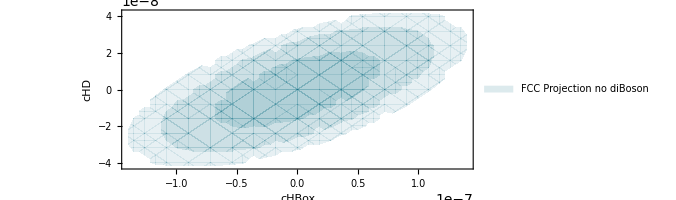

```mathematica
If[CVorFCC==1,FCCRegion=ConfidenceRegionsPlot[cHBox, cHD, χPlot, resultPlot[[1]], resultPlot[[2]],3,0.66*10^(7),0.6*10^(7),ColorData["BlueGreenYellow"][0.3],LegendFCC]]
```

```mathematica
If[CVorFCC==0 && CVSM== 1 (*To properly compare we need same central values*),ActualRegion=ConfidenceRegionsPlot[cHmu,cHb,χPlot, resultPlot[[1]], resultPlot[[2]],3,300,300,ColorData["BlueGreenYellow"][0.8],LegendCV]]
```

### cHq3 and cHL3 Plots code

```mathematica
AspectRatioValue=1/(2.1);
Ploty=1.*10^-7;
Plotx=1/AspectRatioValue*Ploty; (*Multiplying by the inverse of aspect ratio we ensure the samescale in both axes*) (*THIS IS NECESSARY IN ORDER TO GET CONCLUSSION FROM CORRELATION PLOTS*)
PlotSizey=Array[#&,5,{-Ploty,Ploty}];
PlotSizex=Array[#&,3,{-Plotx,Plotx}];
cHq3cHL33rd33=Show[{FCCRegion,ActualRegion} ,ImageSize->Large,AspectRatio->AspectRatioValue,PlotRange-> {{-Plotx,Plotx},{-Ploty,Ploty}}, FrameTicks->{{PlotSizey,None},{PlotSizex,None}}];
```

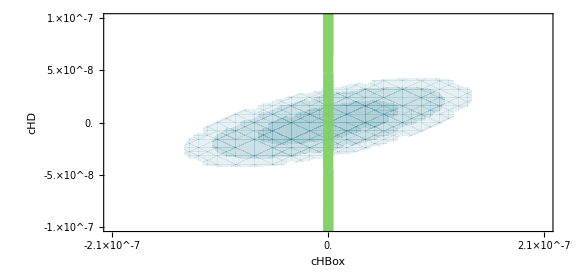

```mathematica
GraphicsGrid[{{cHq3cHL3Univ,cHq3cHL31111 ,cHq3cHL33rd11},{SpanFromAbove,cHq3cHL31122,cHq3cHL33rd22},{SpanFromAbove,cHq3cHL31133,cHq3cHL33rd33}},ImageSize->Full,AspectRatio->1/(2.1)]
```

### Flat direction Plots code

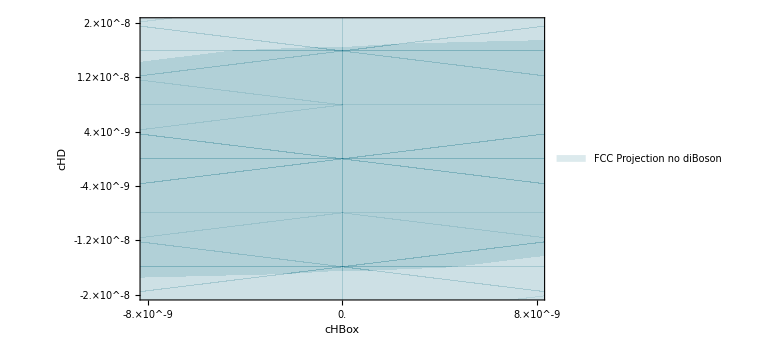

```mathematica
Plotx=8.*10^-9;
Ploty=2.*10^-8;
PlotSizey=Array[#&,6,{-Ploty,Ploty}];
PlotSizex=Array[#&,3,{-Plotx,Plotx}];
FlatDirHiggs=Show[{FCCRegion} ,ImageSize->Large,PlotRange-> {{-Plotx,Plotx},{-Ploty,Ploty}},AspectRatio-> 1/GoldenRatio, FrameTicks->{{PlotSizey,None},{PlotSizex,None}}];
GraphicsGrid[{{FlatDirBroken,FlatDirHiggs},{SpanFromAbove,FlatDirDiBoson}},ImageSize->Full,AspectRatio->1/GoldenRatio]
```

### FCC plots

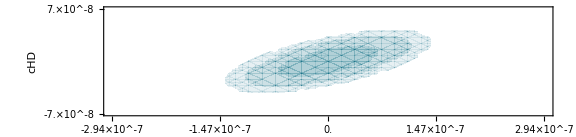

```mathematica
AspectRatioValue=1/(2*2.1);
Ploty=7.*10^-8;
Plotx=1/AspectRatioValue*Ploty; (*Multiplying by the inverse of aspect ratio we ensure the samescale in both axes*) (*THIS IS NECESSARY IN ORDER TO GET CONCLUSSION FROM CORRELATION PLOTS*)
PlotSizey=Array[#&,2,{-Ploty,Ploty}];
PlotSizex=Array[#&,5,{-Plotx,Plotx}];
Prev=Show[FCCRegion ,ImageSize->Large,AspectRatio->AspectRatioValue,PlotRange-> {{-Plotx,Plotx},{-Ploty,Ploty}}, FrameTicks->{{PlotSizey,None},{PlotSizex,None}}]
```

```mathematica
GraphicsGrid[{{Prev},{New}},ImageSize->Full,AspectRatio->1/4]
```

-Graphics-

### cHucHb plot

```mathematica
AspectRatioValue=0.6;
Ploty=4.*10^-7;
Plotx=1/AspectRatioValue*Ploty; (*Multiplying by the inverse of aspect ratio we ensure the samescale in both axes*) (*THIS IS NECESSARY IN ORDER TO GET CONCLUSSION FROM CORRELATION PLOTS*)
PlotSizey=Array[#&,2,{-Ploty,Ploty}];
PlotSizex=Array[#&,5,{-Plotx,Plotx}];
cHucHbgeneral=Show[{FCCRegion,ActualRegion}  ,ImageSize->Large,AspectRatio->AspectRatioValue,PlotRange-> {{-Plotx,Plotx},{-Ploty,Ploty}}, FrameTicks->{{PlotSizey,None},{PlotSizex,None}}];
```

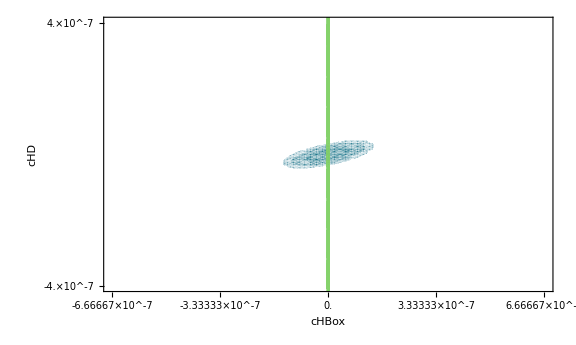

```mathematica
GraphicsGrid[{{cHucHbUniv,cHucHbgeneral}},ImageSize->Full,AspectRatio->AspectRatioValue]
```

### cHmucHb Plot

```mathematica
AspectRatioValue=1/(2.1);
Plotx=-2.*10^-8; 
Ploty=AspectRatioValue*Plotx;(*Multiplying by the aspect ratio we ensure the samescale in both axes*) (*THIS IS NECESSARY IN ORDER TO GET CONCLUSSION FROM CORRELATION PLOTS*)
PlotSizey=Array[#&,5,{-Ploty,Ploty}];
PlotSizex=Array[#&,2,{-Plotx,Plotx}];
cHmucHbFCCWithDiBoson=Show[FCCRegion ,ImageSize->Large,AspectRatio->AspectRatioValue,PlotRange-> {{-Plotx,Plotx},{-Ploty,Ploty}}, FrameTicks->{{PlotSizey,None},{PlotSizex,None}}];
```

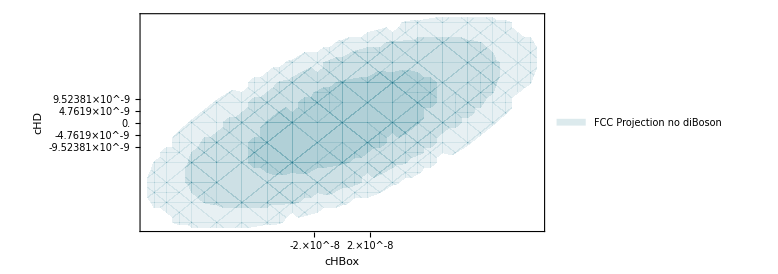

```mathematica
GraphicsGrid[{{cHmucHbCurrent,cHmucHbFCC,cHmucHbFCCWithDiBoson}},ImageSize->Full,AspectRatio->AspectRatioValue]
```

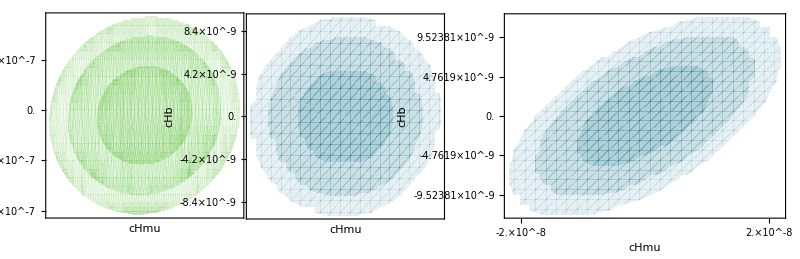

-Graphics-

## 1σ reach EW sector

We are saving the 1σ reach for current and future data in order to plot both and visualy see the improvement.

```mathematica
Labels1sigmaEW={gZeeL,gZeeR,gZmumuL,gZmumuR,gZtautauL,gZtautauR,gWeveL,gWmuvmuL,gWtauvtauL,gZccL,gZccR,gZddL,gZddR,gZbbL,gZbbR};
```

```mathematica
Array1σreach={};
For[i=1,i≤ Length[Labels1sigmaEW],i++,AppendTo[Array1σreach,OneSigmaReach[-I*Labels1sigmaEW[[i]]/.rulegZ1gZ2 /.rule12FermFam /.rule3rdfam/.ruleCouplings /.ruleInputs,TableForLatexWithNames,U]]]
```

```mathematica
Labels1sigmaString={Subscript[δg,"Z,L"]^(ee),Subscript[δg,"Z,R"]^ee,Subscript[δg,"Z,L"]^μμ,Subscript[δg,"Z,R"]^μμ,Subscript[δg,"Z,L"]^ττ,Subscript[δg,"Z,R"]^ττ,Subscript[δg,"W"]^Subscript[eν, e],Subscript[δg,"W"]^Subscript[μν, μ],Subscript[δg,"W"]^Subscript[τν, τ],Subscript[δg,"Z,L"]^"uu/cc",Subscript[δg,"Z,R"]^"uu/cc",Subscript[δg,"Z,L"]^"dd/ss",Subscript[δg,"Z,R"]^"dd/ss",Subscript[δg,"Z,L"]^bb,Subscript[δg,"Z,R"]^bb };
```

```mathematica
If[CVorFCC==0 ,Array1σreachCV=Array1σreach]; (*IMPORTANT TO TAKE INTO ACCOUNT IF CVSM IS 0 OR 1*)
If[CVorFCC==1 && FCCWithZPole== 1 ,Array1σreachFCCZPole=Array1σreach] ;
```

```mathematica
Array1σreachFCCZPole
```

{0.00808988,0.00810745,0.00847194,0.00851965,0.0112941,0.0126086,0.0113964,0.0152592,0.0184262,0.0762631,0.0797355,0.0687804,0.996943,0.0173414,0.128022}

We need to decompose this 2 list in n list of 2 in order to make the plot

```mathematica
PlotList={};
For[i=1,i≤ Length[Labels1sigmaEW],i++,AppendTo[PlotList,{Array1σreachFCCZPole[[i]],Array1σreachCV[[i]]}]]
```

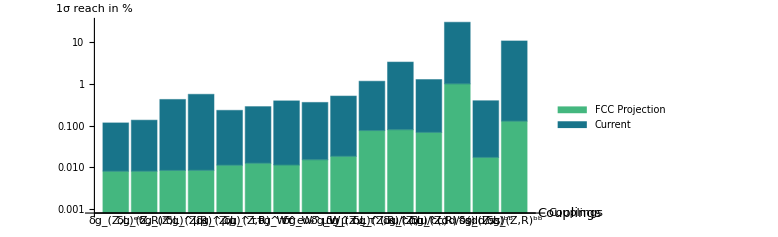

```mathematica
BarChart[PlotList,ChartLayout->"Stacked",ChartLabels->{Labels1sigmaString,None},ScalingFunctions->"Log10", AxesLabel->{Style["Couplings",Black,13],Style["1σ reach in %",Black,15]},AspectRatio->1/(1.5GoldenRatio),ChartStyle->{ColorData["BlueGreenYellow"][0.6],ColorData["BlueGreenYellow"][0.3]},ImageSize->Large,ChartLegends-> Placed[{{Style["FCC Projection",Bold,15],Style["Current",Bold,15]}},{Center,Top}],LegendAppearance->"Column",LabelStyle->{Bold,Black,13}, TicksStyle->Black]
```

## 1σ reach Higgs Sector

```mathematica
CurrentHiggsCoup={5.64847,2.32232,0,4.5461,2.20495,1.96865,1.96318,11.1151,1.90249};
```

```mathematica
HiggsCoup=Re[gHffL] //ComplexExpand ;(*Imaginary part does not interfere with SM*)
Labels1sigmaHiggs={HiggsCoup  /.cfHre -> cmuHre /.ruleMuonMass,HiggsCoup /.cfHre -> ctauHre /.ruleTauMass,HiggsCoup /.cfHre -> ccHre /.ruleCharmMass,HiggsCoup /.cfHre -> cbHre /.ruleBottomMass,(*Deffinitions*)SMEFTExpand1[√SignalStrenght[ΓHZZTeo]],SMEFTExpand1[√SignalStrenght[ΓHWqqTeo]],SMEFTExpand1[√SignalStrenght[ΓHGaGaTeo]],SMEFTExpand1[√SignalStrenght[ΓHZGaTeo]],SMEFTExpand1[√SignalStrenght[ΓHggTeo]]} ;
Labels1sigmaHiggsString={Subscript[δg,"H"]^μμ,Subscript[δg,"H"]^ττ,Subscript[δg,"H"]^cc,Subscript[δg,"H"]^bb,Subscript[δg,"H"]^ZZ, Subscript[δg,"H"]^WW,Subscript[δg,"H"]^γγ,Subscript[δg,"H"]^Zγ,Subscript[δg,"H"]^gg};
```

```mathematica
Array1σreachHiggs={};
For[i=1,i≤ Length[Labels1sigmaHiggsString],i++,AppendTo[Array1σreachHiggs,OneSigmaReach[Labels1sigmaHiggs[[i]]/.rule12FermFam /.rule3rdfam/.rulegZ1gZ2 /.ruleCouplings /.ruleInputs,TableForLatexWithNames,U]]]
```

```mathematica
If[FCCWithZPole== 0&& HLLHC== 0, Array1σreachHiggsNoZPole=Array1σreachHiggs];
If[FCCWithZPole== 1&& HLLHC== 0,Array1σreachHiggsZPole=Array1σreachHiggs];
If[FCCWithZPole== 1 && HLLHC== 1, Array1σreachHiggsFCCAndHLLHC=Array1σreachHiggs];
If[FCCWithZPole== 0 && HLLHC== 1, Array1σreachHiggsFCCNoZPoleAndHLLHC=Array1σreachHiggs];
```

```mathematica
Grid[{Prepend[Labels1sigmaHiggsString,""],Prepend[CurrentHiggsCoup,"Current LHC"],Prepend[Array1σreachHiggsNoZPole, "FCC no Z pole"],Prepend[Array1σreachHiggsZPole,"FCC with Z pole"],Prepend[Array1σreachHiggsFCCAndHLLHC,"FCC+HL-LHC"]}]
```

| δg_H^μμ | δg_H^ττ | δg_H^cc | δg_H^bb | δg_H^ZZ | δg_H^WW | δg_H^γγ | δg_H^Zγ | δg_H^gg
Current LHC | 5.64847 | 2.32232 | 0 | 4.5461 | 2.20495 | 1.96865 | 1.96318 | 11.1151 | 1.90249
FCC no Z pole | 7.32734 | 0.851975 | 1.16465 | 0.787928 | 0.717268 | 0.690553 | 3.58786 | 6.77223 | 1.08458
FCC with Z pole | 7.3014 | 0.58845 | 0.988402 | 0.491167 | 0.29448 | 0.31783 | 3.53457 | 6.74374 | 0.892664
FCC+HL-LHC | 4.27477 | 0.536084 | 0.965207 | 0.445531 | 0.255476 | 0.270814 | 1.05276 | 5.67744 | 0.828308

```mathematica
Array1σreachHiggsZPole/Array1σreachHiggsNoZPole
```

{0.996459,0.690689,0.848669,0.623365,0.410558,0.460255,0.985147,0.995793,0.82305}

```mathematica
PlotList={};
For[i=1,i≤ Length[Array1σreachHiggs],i++,AppendTo[PlotList,{CurrentHiggsCoup[[i]],Array1σreachHiggsNoZPole[[i]],Array1σreachHiggsZPole[[i]],Array1σreachHiggsFCCAndHLLHC[[i]]}]]
```

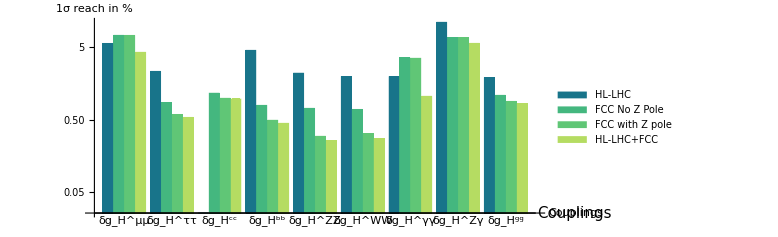

```mathematica
If[CVorFCC==1,BarChart[PlotList,ChartLabels->{Labels1sigmaHiggsString,None},ScalingFunctions->"Log10", AxesLabel->{Style["Couplings",Black,15],Style["1σ reach in %",Black,15]},AspectRatio->1/(1.5GoldenRatio),ChartStyle->{ColorData["BlueGreenYellow"][0.3],ColorData["BlueGreenYellow"][0.6],ColorData["BlueGreenYellow"][0.7],ColorData["BlueGreenYellow"][0.9]},ImageSize->Large,ChartLegends-> Placed[{{Style["HL-LHC",Bold,15],Style["FCC No Z Pole",Bold,15],Style["FCC with Z pole",Bold,15],Style["HL-LHC+FCC",Bold,15]}},{Center,Top}],LegendAppearance->"Column",BarSpacing->{Small,Medium},LabelStyle->{Bold,Black,13}]]
```

## Current fit status

```mathematica
Array1σreach={};
Couplings={cHb,cHd,cHu,cHe,cHmu,cHtau,cHL111,cHL122,cHL133,cHL311,cHL322,cHL333,cHq111,cHq311,cHq3rd,cLLeuue};
For[i=1,i≤ Length[Couplings],i++,AppendTo[Array1σreach,
Around[Couplings[[i]]/.MinimiceResult[[2]],CouplingPrecision[Couplings[[i]],TableForLatexWithNames,U] ]]]
```

```mathematica
WilsonCoefCurrentString={};
For[i=1,i≤ Length[Couplings],i++, AppendTo[WilsonCoefCurrentString, Rotate[Subscript[C,StringDrop[TextString[Couplings[[i]]/.cDownHre-> cdHre /.cUpHre-> cuHre /.cLLeuue-> cll1221],1]] ,Pi/2] ]]
```

```mathematica
WilsonCoefCurrentString= {Subscript[C, "Hd33"],Subscript[C, "Hd11"],Subscript[C, "Hu11"],Subscript[C, "He11"],Subscript[C, "He22"],Subscript[C, "He33"],Subsuperscript[C,"Hl11",Style["(1)",Tiny]],Subsuperscript[C,"Hl22",Style["(1)",Tiny]],Subsuperscript[C,"Hl33",Style["(1)",Tiny]],Subsuperscript[C,"Hl11",Style["(3)",Tiny]],Subsuperscript[C,"Hl22",Style["(3)",Tiny]],Subsuperscript[C,"Hl33",Style["(3)",Tiny]],Subsuperscript[C,"Hq11",Style["(1)",Tiny]],Subsuperscript[C,"Hq11",Style["(3)",Tiny]],Subscript[C, "Hq3rd"],Subscript[C, "ll1221"]};
```

```mathematica
If[CVorFCC==0 && HLLHC== 0&& CVSM== 0,Array1σreachCurrent=Array1σreach*10^6];
For[i=1,i≤ Length[Array1σreachCurrent],i++,Array1σreachCurrent[[i]]=Labeled[Array1σreach[[i]]*10^6,Style[WilsonCoefCurrentString[[i]],Bold,13],Left,Background->Transparent]]
```

```mathematica
ListPlot[Array1σreachCurrent,AxesLabel->{Style["Wilson
Coefficients",Black,15],Style["c/_(Λ^2) TeV^-2",Black,15]},AspectRatio->1/(1.5GoldenRatio),PlotRange->{Automatic,{-1.2,2.3}},PlotMarkers-> Style[•,ColorData["BlueGreenYellow"][0.6],10],PlotStyle->ColorData["BlueGreenYellow"][0.4],TicksStyle->{Directive[FontOpacity->0,FontSize->0],Automatic},Ticks->{None, Automatic},IntervalMarkers->"Fences",IntervalMarkersStyle-><|"FenceWidth"->.3,"FenceStyle"->Directive[ColorData["BlueGreenYellow"][0.6],CapForm["Butt"],Thick],"WhiskerStyle"->Directive[CapForm["Butt"],Opacity[.5],AbsoluteThickness[25],ColorData["BlueGreenYellow"][0.7]]|>,TicksStyle->Bold]
```

ListPlot::lpn: Array1σreachCurrent is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[Array1σreachCurrent,AxesLabel→{Wilson
Coefficients,c/_(Λ^2) TeV^-2},AspectRatio→0.412023,PlotRange→{Automatic,{-1.2,2.3}},PlotMarkers→•,PlotStyle→RGBColor[0.1288222, 0.5597884000000001, 0.5402974],TicksStyle→{Directive[FontOpacity→0,FontSize→0],Automatic},Ticks→{None,Automatic},IntervalMarkers→Fences,IntervalMarkersStyle→<|FenceWidth→0.3,FenceStyle→Directive[RGBColor[0.2679184, 0.718234, 0.496156],CapForm[Butt],Thickness[Large]],WhiskerStyle→Directive[CapForm[Butt],Opacity[0.5],AbsoluteThickness[25],RGBColor[0.37800259999999997, 0.7777646, 0.4612972]]|>,TicksStyle→Bold]

## DiBoson data Global Fit impact

Now we analyze the impact that considering diBoson data has on the rest of the global fit parammeters.

```mathematica
HiggsCoup=Re[gHffL] //ComplexExpand; (*Imaginary part does not interfere with SM*)
```

```mathematica
LabelsDiBosonImpactEW={gZeeL,gZeeR,gZmumuL,gZmumuR,gZtautauL,gZtautauR,gWeveL,gWmuvmuL,gWtauvtauL,gZccL,gZccR,gZddL,gZddR,gZbbL,gZbbR}/.rulegZ1gZ2 /.ruleCouplings/.ruleInputs //SMEFTExpand1;
LabelsDiBosonImpactHiggs={HiggsCoup /.cfHre -> cmuHre /.ruleMuonMass,HiggsCoup /.cfHre -> ctauHre /.ruleTauMass,HiggsCoup /.cfHre -> ccHre /.ruleCharmMass,HiggsCoup /.cfHre -> cbHre /.ruleBottomMass,SMEFTExpand1[√SignalStrenght[ΓHZZTeo]],SMEFTExpand1[√SignalStrenght[ΓHWqqTeo]],SMEFTExpand1[√SignalStrenght[ΓHGaGaTeo]],SMEFTExpand1[√SignalStrenght[ΓHZGaTeo]],SMEFTExpand1[√SignalStrenght[ΓHggTeo]]}/.ruleCouplings/.ruleInputs //SMEFTExpand1;(*Precision for ZZh and WWh are taked into accound with the contribution of both couplings *)
```

```mathematica
DiBosonImpact={};
For[i=1,i≤ Length[LabelsDiBosonImpactEW],i++,AppendTo[DiBosonImpact,CouplingPrecision[-I*LabelsDiBosonImpactEW[[i]] /.rule12FermFam /.rule3rdfam,TableForLatexWithNames,U]]]
For[i=1,i≤ Length[LabelsDiBosonImpactHiggs],i++,AppendTo[DiBosonImpact,CouplingPrecision[LabelsDiBosonImpactHiggs[[i]],TableForLatexWithNames,U]]]
```

```mathematica
LabelsDiBosonImpactString={Subsuperscript[δg,"Z,L",ee],Subsuperscript[δg,"Z,R",ee],Subsuperscript[δg,"Z,L",μμ],Subsuperscript[δg,"Z,R",μμ],Subsuperscript[δg,"Z,L",ττ],Subsuperscript[δg,"Z,R",ττ],Subsuperscript[δg,"W",Subscript[eν, e]],Subsuperscript[δg,"W",Subscript[μν, μ]],Subsuperscript[δg,"W",Subscript[τν, τ]],Subsuperscript[δg,"Z,L","uu/cc"],Subsuperscript[δg,"Z,R","uu/cc"],Subsuperscript[δg,"Z,L","dd/ss"],Subsuperscript[δg,"Z,R","dd/ss"],Subsuperscript[δg,"Z,L",bb],Subsuperscript[δg,"Z,R",bb],Subsuperscript[δg,"H",μμ],Subsuperscript[δg,"H",ττ],Subsuperscript[δg,"H",cc],Subsuperscript[δg,"H",bb],Subscript[δg,"H"]^ZZ, Subscript[δg,"H"]^WW,Subscript[δg,"H"]^γγ,Subscript[δg,"H"]^Zγ,Subscript[δg,"H"]^gg};
```

```mathematica
If[FCCWithDiBoson==0 && CVorFCC== 1,ArrayNoDiBoson=DiBosonImpact]; 
If[FCCWithDiBoson==1 && CVorFCC== 1,ArrayDiBoson=DiBosonImpact];
If[ValueQ[ArrayNoDiBoson]== True && ValueQ[ArrayDiBoson]== True, ArrayDiBosonImpact=100(1 -ArrayDiBoson/ArrayNoDiBoson)//Simplify];
```

Power::infy: Infinite expression 1/0. encountered.

Now we make a circular plot to visualice the result in each sector. We divide the circunferes in the number of sectors needed, and for each one we assing a value corresponding with a coupling precision improvement, then we plot it.

```mathematica
LabelSize=14;
```

```mathematica
(*Defining the vectors to the polar plot*)
DiBosonPlotData={};
ArrayAngles={};
For[i=1,i≤ Length[ArrayDiBosonImpact],i++, AppendTo[DiBosonPlotData,{Pi/2+((i-4)*2*Pi)/Length[ArrayDiBosonImpact],ArrayDiBosonImpact[[i]]}]; AppendTo[ArrayAngles,Pi/2+((i-4)*2*Pi)/Length[ArrayDiBosonImpact]]];

(*Labeling Axes*)
TicksLabeled={};
For[i=1,i≤ Length[ArrayDiBosonImpact],i++, AppendTo[TicksLabeled,{Pi/2+((i-4)*2*Pi)/Length[LabelsDiBosonImpactString],Style[LabelsDiBosonImpactString[[i]],LabelSize]}]]
PercentageLabels={{25,Style["25%",LabelSize]},{50,Style["50%",LabelSize]},{75,Style["75%",LabelSize]}};
```

```mathematica
(*Countours sectors for the Coupling Labels*)
InnerDisk=Disk[{0,0},100];
DiskEWSector=Disk[{0,0},125,{ArrayAngles[[14]]+(3Pi)/Length[LabelsDiBosonImpactString],ArrayAngles[[1]]-Pi/Length[LabelsDiBosonImpactString]}];
DiskHiggsSector=Disk[{0,0},125,{ArrayAngles[[14]]+(3Pi)/Length[LabelsDiBosonImpactString],ArrayAngles[[Length[ArrayAngles]]]+(1.Pi)/Length[LabelsDiBosonImpactString]}];
(*Gradient to optimally visualize percentage sectors*)
PercentSectors={};
For[i=0,i≤ 4,i++, AppendTo[PercentSectors,{Opacity[0.3-0.02*i,ColorData["BlueGreenYellow"][0.4]],Disk[{0,0},0+25*i]}]];
AppendTo[PercentSectors,{Opacity[0.4-0.06*i,ColorData["BlueGreenYellow"][0.4]],Disk[{0,0},Log10[2*10^3.7]]}];

(*Making the plot*)
DiBosonPlot=ListPolarPlot[DiBosonPlotData,PlotStyle-> ColorData["BlueGreenYellow"][0.3],PolarAxes->True,PolarTicks-> {TicksLabeled,PercentageLabels},  PolarGridLines->{ArrayAngles,{25,50,75,100}},Joined-> True,Mesh->Full, PlotRangeClipping->False, ImageSize->Large,ImagePadding->{{50,50},{35,35}},Prolog->{{Opacity[0.6,ColorData["BlueGreenYellow"][0.6]],DiskEWSector},{Opacity[0.6,ColorData["BlueGreenYellow"][0.2]],DiskHiggsSector},{White,InnerDisk},{Opacity[0.5,LightGray],InnerDisk},PercentSectors,{Thick,Circle[{0,0},100]} } ]
```

-Graphics-

An usefull function in order to fill the interpolation lines

```mathematica
Style[DiBosonPlot/.l_Line:>{l,Opacity[.3],FilledCurve[l]},AutoStyleOptions->{"HighlightFormattingErrors"->False}]
```

-Graphics-

## Z-pole run in FCC Global Fit impact

Now we analyze the impact thata new Z-pole run on FCC has on the rest of the global fit parammeters.

```mathematica
LabelsZpoleImpactDiBoson={λZ,δκγ,δg1Z};
LabelsZpoleImpactHiggs={HiggsCoup /.cfHre -> cmuHre /.ruleMuonMass,HiggsCoup /.cfHre -> ctauHre /.ruleTauMass,HiggsCoup /.cfHre -> ccHre /.ruleCharmMass,HiggsCoup /.cfHre -> cbHre /.ruleBottomMass,SMEFTExpand1[√SignalStrenght[ΓHZZTeo]],SMEFTExpand1[√SignalStrenght[ΓHWqqTeo]],SMEFTExpand1[√SignalStrenght[ΓHGaGaTeo]],SMEFTExpand1[√SignalStrenght[ΓHZGaTeo]],SMEFTExpand1[√SignalStrenght[ΓHggTeo]]};(*Precision for ZZh and WWh are taked into accound with the contribution of both couplings *)
```

```mathematica
ZpoleImpact={};
For[i=1,i≤ Length[LabelsZpoleImpactDiBoson],i++,AppendTo[ZpoleImpact,CouplingPrecision[LabelsZpoleImpactDiBoson[[i]]/.rulegZ1gZ2 /.rule12FermFam /.rule3rdfam/.ruleCouplings /.ruleInputs,TableForLatexWithNames,U]]]
For[i=1,i≤ Length[LabelsZpoleImpactHiggs],i++,AppendTo[ZpoleImpact,CouplingPrecision[LabelsZpoleImpactHiggs[[i]] /.ruleCouplings /.ruleInputs,TableForLatexWithNames,U]]]
```

```mathematica
LabelsZpoleImpactString={Subscript[λ,"Z"],Subscript[δk,γ],Subscript[δg,"1,Z"],Subsuperscript[δg,"H",μμ],Subsuperscript[δg,"H",ττ],Subsuperscript[δg,"H",cc],Subsuperscript[δg,"H",bb],Subscript[δg,"H"]^ZZ, Subscript[δg,"H"]^WW,Subscript[δg,"H"]^γγ,Subscript[δg,"H"]^Zγ,Subscript[δg,"H"]^gg};
```

```mathematica
If[FCCWithZPole==0 && CVorFCC== 1,ArrayNoZpole=ZpoleImpact]; 
If[FCCWithZPole==1 && CVorFCC== 1,ArrayZpole=ZpoleImpact];
If[ValueQ[ArrayNoZpole]== True && ValueQ[ArrayZpole]== True, ArrayZpoleImpact= Log10[100(1-ArrayZpole/ArrayNoZpole )]//Simplify];
```

Now we make a circular plot to visualice the result in each sector. We divide the circunferes in the number of sectors needed, and for each one we assing a value corresponding with a coupling precision improvement, then we plot it.

```mathematica
LabelSize=14;
```

```mathematica
(*Defining the vectors to the polar plot*)
ZpoleImpactData={};
ArrayAngles={};
For[i=1,i≤ Length[ArrayZpoleImpact],i++, AppendTo[ZpoleImpactData,{Pi/2+((i)*2*Pi)/Length[ArrayZpoleImpact],ArrayZpoleImpact[[i]]}]; AppendTo[ArrayAngles,Pi/2+((i)*2*Pi)/Length[ArrayZpoleImpact]]];

(*Labeling Axes*)
TicksLabeled={};
For[i=1,i≤ Length[ArrayZpoleImpact],i++, AppendTo[TicksLabeled,{Pi/2+((i)*2*Pi)/Length[LabelsZpoleImpactString],Style[LabelsZpoleImpactString[[i]],LabelSize]}]]
PercentageLabels={{Log10[5],Style["5%",LabelSize]},{Log10[10],Style["10%",LabelSize]},{Log10[20],Style["20%",LabelSize]},{Log10[40],Style["40%",LabelSize]},{Log10[80],Style["80%",LabelSize]}};
```

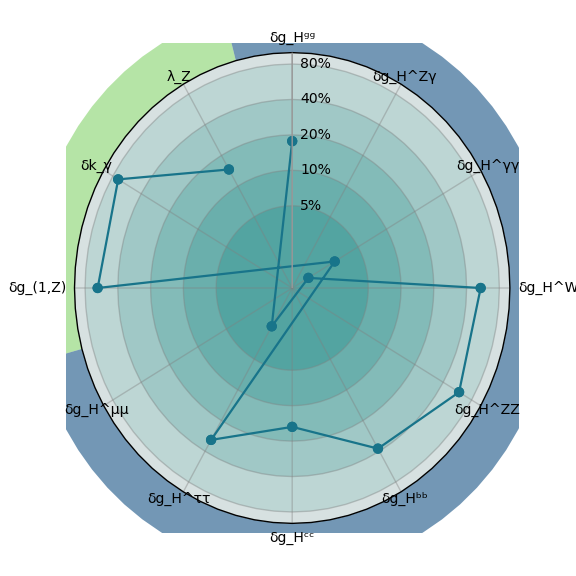

```mathematica
(*Countours sectors for the Coupling Labels*)
InnerDisk=Disk[{0,0},2];
DiskEWSector=Disk[{0,0},2.4,{ArrayAngles[[1]]-Pi/Length[LabelsZpoleImpactString],ArrayAngles[[3]]+Pi/Length[LabelsZpoleImpactString]}];
DiskHiggsSector=Disk[{0,0},2.4,{ArrayAngles[[3]]+Pi/Length[LabelsZpoleImpactString],ArrayAngles[[Length[ArrayAngles]]]+Pi/Length[LabelsZpoleImpactString]}];
(*Gradient to optimally visualize percentage sectors*)
PercentSectors={};
For[i=0,i<5,i++, AppendTo[PercentSectors,{Opacity[0.3-0.04*i,ColorData["BlueGreenYellow"][0.4]],Disk[{0,0},Log10[5]+i*Log10[2]]}]]
AppendTo[PercentSectors,{Opacity[0.3-0.04*5,ColorData["BlueGreenYellow"][0.4]],Disk[{0,0},Log10[100]]}];
(*Making the plot*)
ZpolePlot=ListPolarPlot[ZpoleImpactData,PlotStyle-> ColorData["BlueGreenYellow"][0.3],PolarAxes->True,PolarTicks-> {TicksLabeled,PercentageLabels},  PolarGridLines->{ArrayAngles,{Log10[5],Log10[10],Log10[20],Log10[40],Log10[80]}},Joined-> True,Mesh->Full, PlotRangeClipping->False, ImageSize->Large,Prolog->{{Opacity[0.6,ColorData["BlueGreenYellow"][0.8]],DiskEWSector},{Opacity[0.6,ColorData["BlueGreenYellow"][0.2]],DiskHiggsSector},{White,InnerDisk},{Opacity[0.5,LightGray],InnerDisk},PercentSectors},ImagePadding->{{50,50},{25,25}} ]
```

```mathematica
Style[ZpolePlot/.l_Line:>{l,Opacity[.3],FilledCurve[l]},AutoStyleOptions->{"HighlightFormattingErrors"->False}];
```

-Graphics-

## Limits on New physics Scale

```mathematica
HLLHCLabels={{cW, cHG, cHW, cHB, cHWB, cHD, cHBox, cHL111, cHL122, cHL133, cHL311, cHL322, cHL333, cHe, cHmu, cHtau, cHq111, cHq133, cHq311, cHu, cHd, cHb, cmuHre, ctauHre, ctHre, cbHre, cLLeuue}};
HLLHCLabels=HLLHCLabels[[1]]/.ruleSaveLeptNonUniv;
HLLHCNPUncert=10^6*{6.7723*10^-8,1.0947*10^-9,8.0119*10^-8,2.4651*10^-8,8.7815*10^-8,1.7757*10^-7,3.1585*10^-7,1.1623*10^-7,1.1412*10^-7,1.3789*10^-7,1.1254*10^-7,1.0517*10^-7,1.3949*10^-7,8.9364*10^-8,9.793*10^-8,9.1162*10^-8,8.4192*10^-8,6.9761*10^-8,1.9459*10^-8,1.5853*10^-7,4.891*10^-7,2.7279*10^-7,5.3255*10^-10,2.9411*10^-9,3.8851*10^-7,1.2451*10^-8,1.324*10^-7};
```

```mathematica
rule2sigmaUncertUnivTeVHLLHC={};
For[i=1,i≤ Length[HLLHCLabels],i++, AppendTo[rule2sigmaUncertUnivTeVHLLHC, HLLHCLabels[[i]]-> 1/(√(2HLLHCNPUncert[[i]]))]]
rule2sigmaUncertUnivTeV={};
For[i=1,i≤ Length[FitParametersUniv],i++, AppendTo[rule2sigmaUncertUnivTeV, FitParametersUniv[[i]]-> 1/(√(2UncertUniv[[i]]))]]
```

```mathematica
WilsonCoefUnivOrdered={cHB,cHBox,cHD,cHG,cHW,cHWB,cW,0,cDownHre,cUpHre,cHd,cHu,cHq1,cHq3,0,cmuHre,ctauHre,cLL,cHe,cHL1,cHL3};
```

We have 7 bosonic coeficients, 6 quarks and 5 for leptons I will divide them in different colors.

```mathematica
ColorsNewPhysics={};
For[i=1,i≤ 7,i++,AppendTo[ColorsNewPhysics,ColorData["BlueGreenYellow"][0.3]] ]
For[i=1,i≤ 6,i++,AppendTo[ColorsNewPhysics,ColorData["BlueGreenYellow"][0.5]] ]
For[i=1,i≤ 5,i++,AppendTo[ColorsNewPhysics,ColorData["BlueGreenYellow"][0.8]] ]
LabelsNewPhy={};
AppendTo[LabelsNewPhy,Style["Bosonic",Bold,15]];
For[i=1,i≤ 6,i++,AppendTo[LabelsNewPhy,None ]]
AppendTo[LabelsNewPhy,Style["Quarks",Bold,15]];
For[i=1,i≤ 5,i++,AppendTo[LabelsNewPhy,None ]]
AppendTo[LabelsNewPhy,Style["Leptons",Bold,15]];
```

```mathematica
WilsonCoefUnivString={};
For[i=1,i≤ Length[WilsonCoefUnivOrdered],i++, AppendTo[WilsonCoefUnivString, Rotate[Subscript[C,StringDrop[TextString[WilsonCoefUnivOrdered[[i]]/.cDownHre-> cdHre /.cUpHre-> cuHre /.cmuHre-> ceH22re/.ctauHre-> ceH33re],1]] ,Pi/2] ]]
```

```mathematica
WilsonCoefUnivString={Subscript[C, "HB"],Subscript[C, "HBox"],Subscript[C, "HD"],Subscript[C, "HG"],Subscript[C, "HW"],Subscript[C, "HWB"],Subscript[C, "W"],"",Re[Subscript[C, "dH"]],Re[Subscript[C, "uH"]],Subscript[C, "Hd"],Subscript[C, "Hu"],Subsuperscript[C,"Hq",Style["(1)",Tiny]],Subsuperscript[C,"Hq",Style["(3)",Tiny]],"",Re[Subscript[C, "eH22"]],Re[Subscript[C, "eH33"]],Subscript[C, "ll"],Subscript[C, "He"],Subsuperscript[C,"Hl",Style["(1)",Tiny]],Subsuperscript[C,"Hl",Style["(3)",Tiny]]};
```

```mathematica
If[HLLHC== 0,NewPhysicScale=WilsonCoefUnivOrdered /.rule2sigmaUncertUnivTeV;NewPhysicScaleIndepent=WilsonCoefUnivOrdered/.TwoSigmaNPScaleIndiv];
If[HLLHC== 1, NewPhysicScaleFCCLHC=WilsonCoefUnivOrdered /.rule2sigmaUncertUnivTeV];
NewPhysicScaleHLLHC=WilsonCoefUnivOrdered/.rule2sigmaUncertUnivTeVHLLHC;
PlotListNewPhysics={};
For[i=1,i≤ Length[WilsonCoefUnivOrdered],i++,AppendTo[PlotListNewPhysics,{NewPhysicScaleHLLHC[[i]],NewPhysicScale[[i]],NewPhysicScaleFCCLHC[[i]]}]]
PlotListNewPhysicsIndependent={};
For[i=1,i≤ Length[WilsonCoefUnivOrdered],i++,AppendTo[PlotListNewPhysicsIndependent,{NewPhysicScaleHLLHC[[i]],NewPhysicScaleIndepent[[i]],NewPhysicScaleFCCLHC[[i]]}]]
```

```mathematica
NPScalePlot=BarChart[PlotListNewPhysics,ChartLabels->{WilsonCoefUnivString,None},ScalingFunctions->"Log10", AxesLabel->{Style["Wilson 
Coeficients",Black,15],Style["Λ/√_c TeV",Black,15]},AspectRatio->1/GoldenRatio,ChartStyle->{ColorData["BlueGreenYellow"][0.3],ColorData["BlueGreenYellow"][0.5],ColorData["BlueGreenYellow"][0.9]},ImageSize->Large,ChartLegends-> Placed[{Style["HL-LHC reach",Black,15],Style["FCC reach",Black,15],Style["FCC+HL-LHC reach",Black,15]},{Center,Top}],LegendAppearance-> "column",BarSpacing->{Tiny,Medium},LabelStyle->{Black,15}];
NPScalePlotIndependent=BarChart[PlotListNewPhysicsIndependent,ChartLabels->{WilsonCoefUnivString,None},ScalingFunctions->"Log10", AxesLabel->{Style["Wilson 
Coeficients",Black,15],Style["Λ/√_c TeV",Black,15]},AspectRatio->1/GoldenRatio,ChartStyle->{ColorData["BlueGreenYellow"][0.3],Opacity[0.3,ColorData["BlueGreenYellow"][0.5]],ColorData["BlueGreenYellow"][0.9]},ImageSize->Large,ChartLegends-> Placed[{None,Style["FCC individual Fit reach",Black,15],None},{Center,Top}],LegendAppearance-> "column",BarSpacing->{Tiny,Medium},LabelStyle->{Black,15}];
```

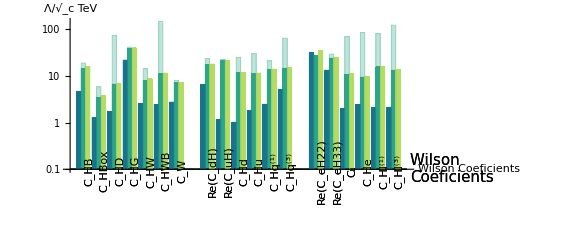

```mathematica
Show[{NPScalePlot,NPScalePlotIndependent},AspectRatio->1/(1.5GoldenRatio)]
```